# Notebook for : Inhomogeneous Cosmology - Gravitational Radiation In Bianchi Backgrounds by Adams et al

Geoff Cope
University of Utah
															𐐏𐐭𐑌𐐲𐑂𐐲𐑉𐑅𐐮𐐻𐐨 𐐲𐑂 𐐏𐐭𐐻𐐫
January 29, 2021

```mathematica
(*  
Metrics to calculate: 1, 23,26, and redo tetrad
*)
```

## Hyperlink To Documentation

```mathematica
Hyperlink["GeneralRelativityTensors Documentation and Download",
"https://github.com/BlackHolePerturbationToolkit"]
```

[GeneralRelativityTensors Documentation and Download](https://github.com/BlackHolePerturbationToolkit)

## Hyperlink To Paper and Related

```mathematica
Hyperlink["Inhomogeneous Cosmology - Gravitational Radiation In Bianchi Backgrounds by Adams et al",
"http://adsabs.harvard.edu/pdf/1982ApJ...253....1A"]
```

[Inhomogeneous Cosmology - Gravitational Radiation In Bianchi Backgrounds by Adams et al](http://adsabs.harvard.edu/pdf/1982ApJ...253....1A)

```mathematica
Hyperlink["Mathematica For Physicists Book By Zimmerman",
"https://library.wolfram.com/infocenter/Books/4539/"]
```

[Mathematica For Physicists Book By Zimmerman](https://library.wolfram.com/infocenter/Books/4539/)

```mathematica
Hyperlink["Zimmerman Homepage",
"https://pages.uoregon.edu/rlz/"]
```

[Zimmerman Homepage](https://pages.uoregon.edu/rlz/)

## Utilities and Package Load

```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 6769 Kb

{Utilities`CleanSlate`,GeneralRelativityTensors`,VariationalMethods`,GeneralRelativityTensors`CommonTensors`,GeneralRelativityTensors`TensorDerivatives`,GeneralRelativityTensors`TensorManipulation`,GeneralRelativityTensors`TensorDefinitions`,GeneralRelativityTensors`Utils`,DocumentationSearch`,ResourceLocator`,NaturalLanguageProcessingLoader`,System`,Global`}

```mathematica
<<GeneralRelativityTensors`
```

## Line Element and Metric

```mathematica
Clear[lineToMetric]
lineToMetric[lineelement_ , differentials_]:= 
Table[If[i==j ,Coefficient[lineelement, differentials[[i]] differentials[[j]]],
(1/2)*Coefficient[lineelement, differentials[[i]] differentials[[j]]]],
{i,1,Length[differentials]},{j,1,Length[differentials]}]  ;
```

```mathematica
Clear[metricToLine]
metricToLine[metric_, differentials_]:= 
Sum[metric[[i,j]] differentials[[i]] differentials[[j]] , {i,1,Length[differentials]},{j,1,Length[differentials]}]
```

## Line Element and Metric 1: Szekeres Plane Gravitational Wave Traveling Along z Axis

```mathematica
Clear[eq1]
eq1 = 
 Exp[2 a] (dz^2-dt^2)+ Exp[2b] (Exp[2ψ] dx^2+ Exp[-2ψ] dy^2)
```

(-dt^2+dz^2) ⅇ^(2 a)+ⅇ^(2 b) (dy^2 ⅇ^(-2 ψ)+dx^2 ⅇ^(2 ψ))

```mathematica
lineToMetric[ eq1 , {dt,dx,dy,dz}] // MatrixForm // pdConv
```

(-ⅇ^(2 a) | 0 | 0 | 0
0 | ⅇ^(2 b+2 ψ) | 0 | 0
0 | 0 | ⅇ^(2 b-2 ψ) | 0
0 | 0 | 0 | ⅇ^(2 a))

```mathematica
Clear[eq1pt1a]
eq1pt1a = {
a-> a[t,z],
b-> b[t,z],
ψ-> ψ[t,z]
} ;
eq1pt1a  // TableForm
```

a→a[t,z]
b→b[t,z]
ψ→ψ[t,z]

```mathematica
Clear[metric1]
metric1 = 
lineToMetric[ eq1 , {dt,dx,dy,dz}] /. eq1pt1a ;
metric1 // MatrixForm // pdConv
```

(-ⅇ^(2 a(t,z)) | 0 | 0 | 0
0 | ⅇ^(2 b(t,z)+2 ψ(t,z)) | 0 | 0
0 | 0 | ⅇ^(2 b(t,z)-2 ψ(t,z)) | 0
0 | 0 | 0 | ⅇ^(2 a(t,z)))

```mathematica
Clear[inverse1]
inverse1 = 
Inverse[ metric1 ]  ;
inverse1 // MatrixForm // pdConv
```

(-ⅇ^(-2 a(t,z)) | 0 | 0 | 0
0 | ⅇ^(-2 b(t,z)-2 ψ(t,z)) | 0 | 0
0 | 0 | ⅇ^(2 ψ(t,z)-2 b(t,z)) | 0
0 | 0 | 0 | ⅇ^(-2 a(t,z)))

```mathematica
metric1 . inverse1 // Expand // MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
inverse1 . metric1  // Expand // MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

## Calculation of Tensors Associated With Metric 1 Szekeres Plane Gravitational Wave

```mathematica
(* $CacheTensorValues=True; *)
```

```mathematica
Clear[input1] 
input1[equationNumber_,equation_,metricName_,displayName_,variables_,indices_]:= Module[{},
Clear[tensorList1];
tensorList1 = {
"g"<>equationNumber,
"christoffel"<>equationNumber , 
"riemann"<>equationNumber  ,
"ricci"<>equationNumber ,
"ricciscalar"<>equationNumber,
"kretschmannscalar"<>equationNumber  ,
"einstein"<>equationNumber  , 
"weyl"<>equationNumber  ,
"cotton"<>equationNumber  
};
tensorList1[[1]] = 
ToMetric[{ metricName, displayName } , variables, equation, indices ] ;
tensorList1[[2]]  = 
ChristoffelSymbol[ tensorList1[[1]] , ActWith-> Simplify] ;
tensorList1[[3]] = 
RiemannTensor[ tensorList1[[1]] , ActWithNested-> Simplify ];
tensorList1[[4]] = 
RicciTensor[ tensorList1[[1]] , ActWith-> Simplify ] ;
tensorList1[[5]] = 
RicciScalar[ tensorList1[[1]] , ActWith-> Simplify ] ;
(* tensorList1[[6]] = 
KretschmannScalar[ tensorList1[[1]] , ActWith-> Simplify] ; *) 
tensorList1[[7]] = 
EinsteinTensor[ tensorList1[[1]] , ActWith-> Simplify] ;  
tensorList1[[8]] = 
WeylTensor[ tensorList1[[1]] , ActWith-> Simplify ] ;
(* tensorList1[[9]] = 
CottonTensor[ tensorList1[[1]] , ActWith-> Simplify ] ; *) 
];
```

```mathematica
(* Last timing took 2.06 for all tensors except Kretschmann and Cotton *) 
input1[ "metric1", metric1, "Szekeres","g^pw",{t,x,y,z}, "Greek"] // Timing
```

{2.0639,Null}

```mathematica
tensorList1
```

{(g^pw)_αβ^,Γ_βγ^α,R_αβγδ^,R_βγ^,R,kretschmannscalarmetric1,G_αβ^,C_αβγδ^,cottonmetric1}

```mathematica
tensorList1[[1]] 
TensorName[tensorList1[[1]]] 
TensorValues[tensorList1[[1]]] // MatrixForm // pdConv
```

(g^pw)_αβ^

Szekeres

(-ⅇ^(2 a(t,z)) | 0 | 0 | 0
0 | ⅇ^(2 b(t,z)+2 ψ(t,z)) | 0 | 0
0 | 0 | ⅇ^(2 b(t,z)-2 ψ(t,z)) | 0
0 | 0 | 0 | ⅇ^(2 a(t,z)))

```mathematica
tensorList1[[2]] 
TensorName[tensorList1[[2]]] 
TensorValues[tensorList1[[2]]] // MatrixForm // pdConv
```

Γ_βγ^α

ChristoffelSymbolSzekeres

(((∂a(t,z))/(∂t)
0
0
(∂a(t,z))/(∂z)) | (0
ⅇ^(2 (-a(t,z)+b(t,z)+ψ(t,z))) ((∂b(t,z))/(∂t)+(∂ψ(t,z))/(∂t))
0
0) | (0
0
ⅇ^(-2 (a(t,z)-b(t,z)+ψ(t,z))) ((∂b(t,z))/(∂t)-(∂ψ(t,z))/(∂t))
0) | ((∂a(t,z))/(∂z)
0
0
(∂a(t,z))/(∂t))
(0
(∂b(t,z))/(∂t)+(∂ψ(t,z))/(∂t)
0
0) | ((∂b(t,z))/(∂t)+(∂ψ(t,z))/(∂t)
0
0
(∂b(t,z))/(∂z)+(∂ψ(t,z))/(∂z)) | (0
0
0
0) | (0
(∂b(t,z))/(∂z)+(∂ψ(t,z))/(∂z)
0
0)
(0
0
(∂b(t,z))/(∂t)-(∂ψ(t,z))/(∂t)
0) | (0
0
0
0) | ((∂b(t,z))/(∂t)-(∂ψ(t,z))/(∂t)
0
0
(∂b(t,z))/(∂z)-(∂ψ(t,z))/(∂z)) | (0
0
(∂b(t,z))/(∂z)-(∂ψ(t,z))/(∂z)
0)
((∂a(t,z))/(∂z)
0
0
(∂a(t,z))/(∂t)) | (0
-ⅇ^(2 (-a(t,z)+b(t,z)+ψ(t,z))) ((∂b(t,z))/(∂z)+(∂ψ(t,z))/(∂z))
0
0) | (0
0
ⅇ^(-2 (a(t,z)-b(t,z)+ψ(t,z))) ((∂ψ(t,z))/(∂z)-(∂b(t,z))/(∂z))
0) | ((∂a(t,z))/(∂t)
0
0
(∂a(t,z))/(∂z)))

```mathematica
tensorList1[[3]] 
TensorName[tensorList1[[3]]] 
TensorValues[tensorList1[[3]]] // MatrixForm // pdConv
```

R_αβγδ^

RiemannTensorSzekeres

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | ⅇ^(2 (b(t,z)+ψ(t,z))) ((∂a(t,z))/(∂t) ((∂b(t,z))/(∂t)+(∂ψ(t,z))/(∂t))+(∂a(t,z))/(∂z) ((∂b(t,z))/(∂z)+(∂ψ(t,z))/(∂z))-(∂^2 b(t,z))/(∂t^2)-2 (∂b(t,z))/(∂t) (∂ψ(t,z))/(∂t)-((∂b(t,z))/(∂t))^2-(∂^2 ψ(t,z))/(∂t^2)-((∂ψ(t,z))/(∂t))^2) | 0 | 0
-ⅇ^(2 (b(t,z)+ψ(t,z))) ((∂a(t,z))/(∂t) ((∂b(t,z))/(∂t)+(∂ψ(t,z))/(∂t))+(∂a(t,z))/(∂z) ((∂b(t,z))/(∂z)+(∂ψ(t,z))/(∂z))-(∂^2 b(t,z))/(∂t^2)-2 (∂b(t,z))/(∂t) (∂ψ(t,z))/(∂t)-((∂b(t,z))/(∂t))^2-(∂^2 ψ(t,z))/(∂t^2)-((∂ψ(t,z))/(∂t))^2) | 0 | 0 | -ⅇ^(2 (b(t,z)+ψ(t,z))) (-(∂^2 b(t,z))/(∂t ∂z)-(∂^2 ψ(t,z))/(∂t ∂z)+(∂b(t,z))/(∂z) ((∂a(t,z))/(∂t)-(∂b(t,z))/(∂t)-(∂ψ(t,z))/(∂t))+(∂ψ(t,z))/(∂z) ((∂a(t,z))/(∂t)-(∂b(t,z))/(∂t)-(∂ψ(t,z))/(∂t))+(∂a(t,z))/(∂z) (∂b(t,z))/(∂t)+(∂a(t,z))/(∂z) (∂ψ(t,z))/(∂t))
0 | 0 | 0 | 0
0 | ⅇ^(2 (b(t,z)+ψ(t,z))) (-(∂^2 b(t,z))/(∂t ∂z)-(∂^2 ψ(t,z))/(∂t ∂z)+(∂b(t,z))/(∂z) ((∂a(t,z))/(∂t)-(∂b(t,z))/(∂t)-(∂ψ(t,z))/(∂t))+(∂ψ(t,z))/(∂z) ((∂a(t,z))/(∂t)-(∂b(t,z))/(∂t)-(∂ψ(t,z))/(∂t))+(∂a(t,z))/(∂z) (∂b(t,z))/(∂t)+(∂a(t,z))/(∂z) (∂ψ(t,z))/(∂t)) | 0 | 0) | (0 | 0 | ⅇ^(2 b(t,z)-2 ψ(t,z)) ((∂a(t,z))/(∂t) ((∂b(t,z))/(∂t)-(∂ψ(t,z))/(∂t))+(∂a(t,z))/(∂z) ((∂b(t,z))/(∂z)-(∂ψ(t,z))/(∂z))-(∂^2 b(t,z))/(∂t^2)+2 (∂b(t,z))/(∂t) (∂ψ(t,z))/(∂t)-((∂b(t,z))/(∂t))^2+(∂^2 ψ(t,z))/(∂t^2)-((∂ψ(t,z))/(∂t))^2) | 0
0 | 0 | 0 | 0
-ⅇ^(2 b(t,z)-2 ψ(t,z)) ((∂a(t,z))/(∂t) ((∂b(t,z))/(∂t)-(∂ψ(t,z))/(∂t))+(∂a(t,z))/(∂z) ((∂b(t,z))/(∂z)-(∂ψ(t,z))/(∂z))-(∂^2 b(t,z))/(∂t^2)+2 (∂b(t,z))/(∂t) (∂ψ(t,z))/(∂t)-((∂b(t,z))/(∂t))^2+(∂^2 ψ(t,z))/(∂t^2)-((∂ψ(t,z))/(∂t))^2) | 0 | 0 | ⅇ^(2 b(t,z)-2 ψ(t,z)) ((∂^2 b(t,z))/(∂t ∂z)-(∂^2 ψ(t,z))/(∂t ∂z)-(∂b(t,z))/(∂z) ((∂a(t,z))/(∂t)-(∂b(t,z))/(∂t)+(∂ψ(t,z))/(∂t))+(∂ψ(t,z))/(∂z) ((∂a(t,z))/(∂t)-(∂b(t,z))/(∂t)+(∂ψ(t,z))/(∂t))-(∂a(t,z))/(∂z) (∂b(t,z))/(∂t)+(∂a(t,z))/(∂z) (∂ψ(t,z))/(∂t))
0 | 0 | -ⅇ^(2 b(t,z)-2 ψ(t,z)) ((∂^2 b(t,z))/(∂t ∂z)-(∂^2 ψ(t,z))/(∂t ∂z)-(∂b(t,z))/(∂z) ((∂a(t,z))/(∂t)-(∂b(t,z))/(∂t)+(∂ψ(t,z))/(∂t))+(∂ψ(t,z))/(∂z) ((∂a(t,z))/(∂t)-(∂b(t,z))/(∂t)+(∂ψ(t,z))/(∂t))-(∂a(t,z))/(∂z) (∂b(t,z))/(∂t)+(∂a(t,z))/(∂z) (∂ψ(t,z))/(∂t)) | 0) | (0 | 0 | 0 | ⅇ^(2 a(t,z)) ((∂^2 a(t,z))/(∂z^2)-(∂^2 a(t,z))/(∂t^2))
0 | 0 | 0 | 0
0 | 0 | 0 | 0
-ⅇ^(2 a(t,z)) ((∂^2 a(t,z))/(∂z^2)-(∂^2 a(t,z))/(∂t^2)) | 0 | 0 | 0)
(0 | -ⅇ^(2 (b(t,z)+ψ(t,z))) ((∂a(t,z))/(∂t) ((∂b(t,z))/(∂t)+(∂ψ(t,z))/(∂t))+(∂a(t,z))/(∂z) ((∂b(t,z))/(∂z)+(∂ψ(t,z))/(∂z))-(∂^2 b(t,z))/(∂t^2)-2 (∂b(t,z))/(∂t) (∂ψ(t,z))/(∂t)-((∂b(t,z))/(∂t))^2-(∂^2 ψ(t,z))/(∂t^2)-((∂ψ(t,z))/(∂t))^2) | 0 | 0
ⅇ^(2 (b(t,z)+ψ(t,z))) ((∂a(t,z))/(∂t) ((∂b(t,z))/(∂t)+(∂ψ(t,z))/(∂t))+(∂a(t,z))/(∂z) ((∂b(t,z))/(∂z)+(∂ψ(t,z))/(∂z))-(∂^2 b(t,z))/(∂t^2)-2 (∂b(t,z))/(∂t) (∂ψ(t,z))/(∂t)-((∂b(t,z))/(∂t))^2-(∂^2 ψ(t,z))/(∂t^2)-((∂ψ(t,z))/(∂t))^2) | 0 | 0 | ⅇ^(2 (b(t,z)+ψ(t,z))) (-(∂^2 b(t,z))/(∂t ∂z)-(∂^2 ψ(t,z))/(∂t ∂z)+(∂b(t,z))/(∂z) ((∂a(t,z))/(∂t)-(∂b(t,z))/(∂t)-(∂ψ(t,z))/(∂t))+(∂ψ(t,z))/(∂z) ((∂a(t,z))/(∂t)-(∂b(t,z))/(∂t)-(∂ψ(t,z))/(∂t))+(∂a(t,z))/(∂z) (∂b(t,z))/(∂t)+(∂a(t,z))/(∂z) (∂ψ(t,z))/(∂t))
0 | 0 | 0 | 0
0 | -ⅇ^(2 (b(t,z)+ψ(t,z))) (-(∂^2 b(t,z))/(∂t ∂z)-(∂^2 ψ(t,z))/(∂t ∂z)+(∂b(t,z))/(∂z) ((∂a(t,z))/(∂t)-(∂b(t,z))/(∂t)-(∂ψ(t,z))/(∂t))+(∂ψ(t,z))/(∂z) ((∂a(t,z))/(∂t)-(∂b(t,z))/(∂t)-(∂ψ(t,z))/(∂t))+(∂a(t,z))/(∂z) (∂b(t,z))/(∂t)+(∂a(t,z))/(∂z) (∂ψ(t,z))/(∂t)) | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | ⅇ^(4 b(t,z)-2 a(t,z)) (((∂b(t,z))/(∂t))^2-((∂b(t,z))/(∂z))^2-((∂ψ(t,z))/(∂t))^2+((∂ψ(t,z))/(∂z))^2) | 0
0 | -ⅇ^(4 b(t,z)-2 a(t,z)) (((∂b(t,z))/(∂t))^2-((∂b(t,z))/(∂z))^2-((∂ψ(t,z))/(∂t))^2+((∂ψ(t,z))/(∂z))^2) | 0 | 0
0 | 0 | 0 | 0) | (0 | -ⅇ^(2 (b(t,z)+ψ(t,z))) (-(∂^2 b(t,z))/(∂t ∂z)-(∂^2 ψ(t,z))/(∂t ∂z)+(∂b(t,z))/(∂z) ((∂a(t,z))/(∂t)-(∂b(t,z))/(∂t)-(∂ψ(t,z))/(∂t))+(∂ψ(t,z))/(∂z) ((∂a(t,z))/(∂t)-(∂b(t,z))/(∂t)-(∂ψ(t,z))/(∂t))+(∂a(t,z))/(∂z) (∂b(t,z))/(∂t)+(∂a(t,z))/(∂z) (∂ψ(t,z))/(∂t)) | 0 | 0
ⅇ^(2 (b(t,z)+ψ(t,z))) (-(∂^2 b(t,z))/(∂t ∂z)-(∂^2 ψ(t,z))/(∂t ∂z)+(∂b(t,z))/(∂z) ((∂a(t,z))/(∂t)-(∂b(t,z))/(∂t)-(∂ψ(t,z))/(∂t))+(∂ψ(t,z))/(∂z) ((∂a(t,z))/(∂t)-(∂b(t,z))/(∂t)-(∂ψ(t,z))/(∂t))+(∂a(t,z))/(∂z) (∂b(t,z))/(∂t)+(∂a(t,z))/(∂z) (∂ψ(t,z))/(∂t)) | 0 | 0 | ⅇ^(2 (b(t,z)+ψ(t,z))) ((∂a(t,z))/(∂z) ((∂b(t,z))/(∂z)+(∂ψ(t,z))/(∂z))+(∂a(t,z))/(∂t) (∂b(t,z))/(∂t)+(∂a(t,z))/(∂t) (∂ψ(t,z))/(∂t)-(∂^2 b(t,z))/(∂z^2)-2 (∂b(t,z))/(∂z) (∂ψ(t,z))/(∂z)-((∂b(t,z))/(∂z))^2-(∂^2 ψ(t,z))/(∂z^2)-((∂ψ(t,z))/(∂z))^2)
0 | 0 | 0 | 0
0 | -ⅇ^(2 (b(t,z)+ψ(t,z))) ((∂a(t,z))/(∂z) ((∂b(t,z))/(∂z)+(∂ψ(t,z))/(∂z))+(∂a(t,z))/(∂t) (∂b(t,z))/(∂t)+(∂a(t,z))/(∂t) (∂ψ(t,z))/(∂t)-(∂^2 b(t,z))/(∂z^2)-2 (∂b(t,z))/(∂z) (∂ψ(t,z))/(∂z)-((∂b(t,z))/(∂z))^2-(∂^2 ψ(t,z))/(∂z^2)-((∂ψ(t,z))/(∂z))^2) | 0 | 0)
(0 | 0 | -ⅇ^(2 b(t,z)-2 ψ(t,z)) ((∂a(t,z))/(∂t) ((∂b(t,z))/(∂t)-(∂ψ(t,z))/(∂t))+(∂a(t,z))/(∂z) ((∂b(t,z))/(∂z)-(∂ψ(t,z))/(∂z))-(∂^2 b(t,z))/(∂t^2)+2 (∂b(t,z))/(∂t) (∂ψ(t,z))/(∂t)-((∂b(t,z))/(∂t))^2+(∂^2 ψ(t,z))/(∂t^2)-((∂ψ(t,z))/(∂t))^2) | 0
0 | 0 | 0 | 0
ⅇ^(2 b(t,z)-2 ψ(t,z)) ((∂a(t,z))/(∂t) ((∂b(t,z))/(∂t)-(∂ψ(t,z))/(∂t))+(∂a(t,z))/(∂z) ((∂b(t,z))/(∂z)-(∂ψ(t,z))/(∂z))-(∂^2 b(t,z))/(∂t^2)+2 (∂b(t,z))/(∂t) (∂ψ(t,z))/(∂t)-((∂b(t,z))/(∂t))^2+(∂^2 ψ(t,z))/(∂t^2)-((∂ψ(t,z))/(∂t))^2) | 0 | 0 | -ⅇ^(2 b(t,z)-2 ψ(t,z)) ((∂^2 b(t,z))/(∂t ∂z)-(∂^2 ψ(t,z))/(∂t ∂z)-(∂b(t,z))/(∂z) ((∂a(t,z))/(∂t)-(∂b(t,z))/(∂t)+(∂ψ(t,z))/(∂t))+(∂ψ(t,z))/(∂z) ((∂a(t,z))/(∂t)-(∂b(t,z))/(∂t)+(∂ψ(t,z))/(∂t))-(∂a(t,z))/(∂z) (∂b(t,z))/(∂t)+(∂a(t,z))/(∂z) (∂ψ(t,z))/(∂t))
0 | 0 | ⅇ^(2 b(t,z)-2 ψ(t,z)) ((∂^2 b(t,z))/(∂t ∂z)-(∂^2 ψ(t,z))/(∂t ∂z)-(∂b(t,z))/(∂z) ((∂a(t,z))/(∂t)-(∂b(t,z))/(∂t)+(∂ψ(t,z))/(∂t))+(∂ψ(t,z))/(∂z) ((∂a(t,z))/(∂t)-(∂b(t,z))/(∂t)+(∂ψ(t,z))/(∂t))-(∂a(t,z))/(∂z) (∂b(t,z))/(∂t)+(∂a(t,z))/(∂z) (∂ψ(t,z))/(∂t)) | 0) | (0 | 0 | 0 | 0
0 | 0 | -ⅇ^(4 b(t,z)-2 a(t,z)) (((∂b(t,z))/(∂t))^2-((∂b(t,z))/(∂z))^2-((∂ψ(t,z))/(∂t))^2+((∂ψ(t,z))/(∂z))^2) | 0
0 | ⅇ^(4 b(t,z)-2 a(t,z)) (((∂b(t,z))/(∂t))^2-((∂b(t,z))/(∂z))^2-((∂ψ(t,z))/(∂t))^2+((∂ψ(t,z))/(∂z))^2) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | ⅇ^(2 b(t,z)-2 ψ(t,z)) ((∂^2 b(t,z))/(∂t ∂z)-(∂^2 ψ(t,z))/(∂t ∂z)-(∂b(t,z))/(∂z) ((∂a(t,z))/(∂t)-(∂b(t,z))/(∂t)+(∂ψ(t,z))/(∂t))+(∂ψ(t,z))/(∂z) ((∂a(t,z))/(∂t)-(∂b(t,z))/(∂t)+(∂ψ(t,z))/(∂t))-(∂a(t,z))/(∂z) (∂b(t,z))/(∂t)+(∂a(t,z))/(∂z) (∂ψ(t,z))/(∂t)) | 0
0 | 0 | 0 | 0
-ⅇ^(2 b(t,z)-2 ψ(t,z)) ((∂^2 b(t,z))/(∂t ∂z)-(∂^2 ψ(t,z))/(∂t ∂z)-(∂b(t,z))/(∂z) ((∂a(t,z))/(∂t)-(∂b(t,z))/(∂t)+(∂ψ(t,z))/(∂t))+(∂ψ(t,z))/(∂z) ((∂a(t,z))/(∂t)-(∂b(t,z))/(∂t)+(∂ψ(t,z))/(∂t))-(∂a(t,z))/(∂z) (∂b(t,z))/(∂t)+(∂a(t,z))/(∂z) (∂ψ(t,z))/(∂t)) | 0 | 0 | -ⅇ^(2 b(t,z)-2 ψ(t,z)) ((∂a(t,z))/(∂z) ((∂ψ(t,z))/(∂z)-(∂b(t,z))/(∂z))-(∂a(t,z))/(∂t) (∂b(t,z))/(∂t)+(∂a(t,z))/(∂t) (∂ψ(t,z))/(∂t)+(∂^2 b(t,z))/(∂z^2)-2 (∂b(t,z))/(∂z) (∂ψ(t,z))/(∂z)+((∂b(t,z))/(∂z))^2-(∂^2 ψ(t,z))/(∂z^2)+((∂ψ(t,z))/(∂z))^2)
0 | 0 | ⅇ^(2 b(t,z)-2 ψ(t,z)) ((∂a(t,z))/(∂z) ((∂ψ(t,z))/(∂z)-(∂b(t,z))/(∂z))-(∂a(t,z))/(∂t) (∂b(t,z))/(∂t)+(∂a(t,z))/(∂t) (∂ψ(t,z))/(∂t)+(∂^2 b(t,z))/(∂z^2)-2 (∂b(t,z))/(∂z) (∂ψ(t,z))/(∂z)+((∂b(t,z))/(∂z))^2-(∂^2 ψ(t,z))/(∂z^2)+((∂ψ(t,z))/(∂z))^2) | 0)
(0 | 0 | 0 | -ⅇ^(2 a(t,z)) ((∂^2 a(t,z))/(∂z^2)-(∂^2 a(t,z))/(∂t^2))
0 | 0 | 0 | 0
0 | 0 | 0 | 0
ⅇ^(2 a(t,z)) ((∂^2 a(t,z))/(∂z^2)-(∂^2 a(t,z))/(∂t^2)) | 0 | 0 | 0) | (0 | ⅇ^(2 (b(t,z)+ψ(t,z))) (-(∂^2 b(t,z))/(∂t ∂z)-(∂^2 ψ(t,z))/(∂t ∂z)+(∂b(t,z))/(∂z) ((∂a(t,z))/(∂t)-(∂b(t,z))/(∂t)-(∂ψ(t,z))/(∂t))+(∂ψ(t,z))/(∂z) ((∂a(t,z))/(∂t)-(∂b(t,z))/(∂t)-(∂ψ(t,z))/(∂t))+(∂a(t,z))/(∂z) (∂b(t,z))/(∂t)+(∂a(t,z))/(∂z) (∂ψ(t,z))/(∂t)) | 0 | 0
-ⅇ^(2 (b(t,z)+ψ(t,z))) (-(∂^2 b(t,z))/(∂t ∂z)-(∂^2 ψ(t,z))/(∂t ∂z)+(∂b(t,z))/(∂z) ((∂a(t,z))/(∂t)-(∂b(t,z))/(∂t)-(∂ψ(t,z))/(∂t))+(∂ψ(t,z))/(∂z) ((∂a(t,z))/(∂t)-(∂b(t,z))/(∂t)-(∂ψ(t,z))/(∂t))+(∂a(t,z))/(∂z) (∂b(t,z))/(∂t)+(∂a(t,z))/(∂z) (∂ψ(t,z))/(∂t)) | 0 | 0 | -ⅇ^(2 (b(t,z)+ψ(t,z))) ((∂a(t,z))/(∂z) ((∂b(t,z))/(∂z)+(∂ψ(t,z))/(∂z))+(∂a(t,z))/(∂t) (∂b(t,z))/(∂t)+(∂a(t,z))/(∂t) (∂ψ(t,z))/(∂t)-(∂^2 b(t,z))/(∂z^2)-2 (∂b(t,z))/(∂z) (∂ψ(t,z))/(∂z)-((∂b(t,z))/(∂z))^2-(∂^2 ψ(t,z))/(∂z^2)-((∂ψ(t,z))/(∂z))^2)
0 | 0 | 0 | 0
0 | ⅇ^(2 (b(t,z)+ψ(t,z))) ((∂a(t,z))/(∂z) ((∂b(t,z))/(∂z)+(∂ψ(t,z))/(∂z))+(∂a(t,z))/(∂t) (∂b(t,z))/(∂t)+(∂a(t,z))/(∂t) (∂ψ(t,z))/(∂t)-(∂^2 b(t,z))/(∂z^2)-2 (∂b(t,z))/(∂z) (∂ψ(t,z))/(∂z)-((∂b(t,z))/(∂z))^2-(∂^2 ψ(t,z))/(∂z^2)-((∂ψ(t,z))/(∂z))^2) | 0 | 0) | (0 | 0 | -ⅇ^(2 b(t,z)-2 ψ(t,z)) ((∂^2 b(t,z))/(∂t ∂z)-(∂^2 ψ(t,z))/(∂t ∂z)-(∂b(t,z))/(∂z) ((∂a(t,z))/(∂t)-(∂b(t,z))/(∂t)+(∂ψ(t,z))/(∂t))+(∂ψ(t,z))/(∂z) ((∂a(t,z))/(∂t)-(∂b(t,z))/(∂t)+(∂ψ(t,z))/(∂t))-(∂a(t,z))/(∂z) (∂b(t,z))/(∂t)+(∂a(t,z))/(∂z) (∂ψ(t,z))/(∂t)) | 0
0 | 0 | 0 | 0
ⅇ^(2 b(t,z)-2 ψ(t,z)) ((∂^2 b(t,z))/(∂t ∂z)-(∂^2 ψ(t,z))/(∂t ∂z)-(∂b(t,z))/(∂z) ((∂a(t,z))/(∂t)-(∂b(t,z))/(∂t)+(∂ψ(t,z))/(∂t))+(∂ψ(t,z))/(∂z) ((∂a(t,z))/(∂t)-(∂b(t,z))/(∂t)+(∂ψ(t,z))/(∂t))-(∂a(t,z))/(∂z) (∂b(t,z))/(∂t)+(∂a(t,z))/(∂z) (∂ψ(t,z))/(∂t)) | 0 | 0 | ⅇ^(2 b(t,z)-2 ψ(t,z)) ((∂a(t,z))/(∂z) ((∂ψ(t,z))/(∂z)-(∂b(t,z))/(∂z))-(∂a(t,z))/(∂t) (∂b(t,z))/(∂t)+(∂a(t,z))/(∂t) (∂ψ(t,z))/(∂t)+(∂^2 b(t,z))/(∂z^2)-2 (∂b(t,z))/(∂z) (∂ψ(t,z))/(∂z)+((∂b(t,z))/(∂z))^2-(∂^2 ψ(t,z))/(∂z^2)+((∂ψ(t,z))/(∂z))^2)
0 | 0 | -ⅇ^(2 b(t,z)-2 ψ(t,z)) ((∂a(t,z))/(∂z) ((∂ψ(t,z))/(∂z)-(∂b(t,z))/(∂z))-(∂a(t,z))/(∂t) (∂b(t,z))/(∂t)+(∂a(t,z))/(∂t) (∂ψ(t,z))/(∂t)+(∂^2 b(t,z))/(∂z^2)-2 (∂b(t,z))/(∂z) (∂ψ(t,z))/(∂z)+((∂b(t,z))/(∂z))^2-(∂^2 ψ(t,z))/(∂z^2)+((∂ψ(t,z))/(∂z))^2) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
tensorList1[[4]] 
TensorName[tensorList1[[4]]] 
TensorValues[tensorList1[[4]]] // MatrixForm // pdConv
```

R_βγ^

RicciTensorSzekeres

(2 (∂a(t,z))/(∂t) (∂b(t,z))/(∂t)+2 (∂a(t,z))/(∂z) (∂b(t,z))/(∂z)-(∂^2 a(t,z))/(∂t^2)+(∂^2 a(t,z))/(∂z^2)-2 (∂^2 b(t,z))/(∂t^2)-2 ((∂b(t,z))/(∂t))^2-2 ((∂ψ(t,z))/(∂t))^2 | 0 | 0 | 2 (-(∂^2 b(t,z))/(∂t ∂z)+(∂a(t,z))/(∂z) (∂b(t,z))/(∂t)+(∂b(t,z))/(∂z) ((∂a(t,z))/(∂t)-(∂b(t,z))/(∂t))-(∂ψ(t,z))/(∂t) (∂ψ(t,z))/(∂z))
0 | ⅇ^(2 (-a(t,z)+b(t,z)+ψ(t,z))) ((∂^2 b(t,z))/(∂t^2)-(∂^2 b(t,z))/(∂z^2)+2 (∂b(t,z))/(∂t) (∂ψ(t,z))/(∂t)-2 (∂b(t,z))/(∂z) (∂ψ(t,z))/(∂z)+2 ((∂b(t,z))/(∂t))^2-2 ((∂b(t,z))/(∂z))^2+(∂^2 ψ(t,z))/(∂t^2)-(∂^2 ψ(t,z))/(∂z^2)) | 0 | 0
0 | 0 | ⅇ^(-2 (a(t,z)-b(t,z)+ψ(t,z))) ((∂^2 b(t,z))/(∂t^2)-(∂^2 b(t,z))/(∂z^2)-2 (∂b(t,z))/(∂t) (∂ψ(t,z))/(∂t)+2 (∂b(t,z))/(∂z) (∂ψ(t,z))/(∂z)+2 ((∂b(t,z))/(∂t))^2-2 ((∂b(t,z))/(∂z))^2-(∂^2 ψ(t,z))/(∂t^2)+(∂^2 ψ(t,z))/(∂z^2)) | 0
2 (-(∂^2 b(t,z))/(∂t ∂z)+(∂a(t,z))/(∂z) (∂b(t,z))/(∂t)+(∂b(t,z))/(∂z) ((∂a(t,z))/(∂t)-(∂b(t,z))/(∂t))-(∂ψ(t,z))/(∂t) (∂ψ(t,z))/(∂z)) | 0 | 0 | 2 (∂a(t,z))/(∂z) (∂b(t,z))/(∂z)+2 (∂a(t,z))/(∂t) (∂b(t,z))/(∂t)+(∂^2 a(t,z))/(∂t^2)-(∂^2 a(t,z))/(∂z^2)-2 (∂^2 b(t,z))/(∂z^2)-2 ((∂b(t,z))/(∂z))^2-2 ((∂ψ(t,z))/(∂z))^2)

```mathematica
tensorList1[[5]] 
TensorName[tensorList1[[5]]] 
TensorValues[tensorList1[[5]]] // MatrixForm // pdConv
```

R

RicciScalarSzekeres

-2 ⅇ^(-2 a(t,z)) (-(∂^2 a(t,z))/(∂t^2)+(∂^2 a(t,z))/(∂z^2)-2 (∂^2 b(t,z))/(∂t^2)+2 (∂^2 b(t,z))/(∂z^2)-3 ((∂b(t,z))/(∂t))^2+3 ((∂b(t,z))/(∂z))^2-((∂ψ(t,z))/(∂t))^2+((∂ψ(t,z))/(∂z))^2)

```mathematica
(*
tensorList1[[6]] 
TensorName[tensorList1[[6]]] 
TensorValues[tensorList1[[6]]] // MatrixForm // pdConv
*)
```

```mathematica
tensorList1[[7]] 
TensorName[tensorList1[[7]]] 
TensorValues[tensorList1[[7]]] // MatrixForm // pdConv
```

G_αβ^

EinsteinTensorSzekeres

(2 (∂a(t,z))/(∂t) (∂b(t,z))/(∂t)+2 (∂a(t,z))/(∂z) (∂b(t,z))/(∂z)-2 (∂^2 b(t,z))/(∂z^2)+((∂b(t,z))/(∂t))^2-3 ((∂b(t,z))/(∂z))^2-((∂ψ(t,z))/(∂t))^2-((∂ψ(t,z))/(∂z))^2 | 0 | 0 | 2 (-(∂^2 b(t,z))/(∂t ∂z)+(∂a(t,z))/(∂z) (∂b(t,z))/(∂t)+(∂b(t,z))/(∂z) ((∂a(t,z))/(∂t)-(∂b(t,z))/(∂t))-(∂ψ(t,z))/(∂t) (∂ψ(t,z))/(∂z))
0 | ⅇ^(2 (-a(t,z)+b(t,z)+ψ(t,z))) (-(∂^2 a(t,z))/(∂t^2)+(∂^2 a(t,z))/(∂z^2)-(∂^2 b(t,z))/(∂t^2)+(∂^2 b(t,z))/(∂z^2)+2 (∂b(t,z))/(∂t) (∂ψ(t,z))/(∂t)-2 (∂b(t,z))/(∂z) (∂ψ(t,z))/(∂z)-((∂b(t,z))/(∂t))^2+((∂b(t,z))/(∂z))^2+(∂^2 ψ(t,z))/(∂t^2)-(∂^2 ψ(t,z))/(∂z^2)-((∂ψ(t,z))/(∂t))^2+((∂ψ(t,z))/(∂z))^2) | 0 | 0
0 | 0 | ⅇ^(-2 (a(t,z)-b(t,z)+ψ(t,z))) (-(∂^2 a(t,z))/(∂t^2)+(∂^2 a(t,z))/(∂z^2)-(∂^2 b(t,z))/(∂t^2)+(∂^2 b(t,z))/(∂z^2)-2 (∂b(t,z))/(∂t) (∂ψ(t,z))/(∂t)+2 (∂b(t,z))/(∂z) (∂ψ(t,z))/(∂z)-((∂b(t,z))/(∂t))^2+((∂b(t,z))/(∂z))^2-(∂^2 ψ(t,z))/(∂t^2)+(∂^2 ψ(t,z))/(∂z^2)-((∂ψ(t,z))/(∂t))^2+((∂ψ(t,z))/(∂z))^2) | 0
2 (-(∂^2 b(t,z))/(∂t ∂z)+(∂a(t,z))/(∂z) (∂b(t,z))/(∂t)+(∂b(t,z))/(∂z) ((∂a(t,z))/(∂t)-(∂b(t,z))/(∂t))-(∂ψ(t,z))/(∂t) (∂ψ(t,z))/(∂z)) | 0 | 0 | 2 (∂a(t,z))/(∂t) (∂b(t,z))/(∂t)+2 (∂a(t,z))/(∂z) (∂b(t,z))/(∂z)-2 (∂^2 b(t,z))/(∂t^2)-3 ((∂b(t,z))/(∂t))^2+((∂b(t,z))/(∂z))^2-((∂ψ(t,z))/(∂t))^2-((∂ψ(t,z))/(∂z))^2)

```mathematica
tensorList1[[8]] 
TensorName[tensorList1[[8]]] 
TensorValues[tensorList1[[8]]] // MatrixForm // pdConv
```

C_αβγδ^

WeylTensorSzekeres

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 1/6 ⅇ^(2 (b(t,z)+ψ(t,z))) ((∂^2 a(t,z))/(∂t^2)-(∂^2 a(t,z))/(∂z^2)+6 (∂a(t,z))/(∂t) (∂ψ(t,z))/(∂t)+6 (∂a(t,z))/(∂z) (∂ψ(t,z))/(∂z)-(∂^2 b(t,z))/(∂t^2)+(∂^2 b(t,z))/(∂z^2)-6 (∂b(t,z))/(∂t) (∂ψ(t,z))/(∂t)-6 (∂b(t,z))/(∂z) (∂ψ(t,z))/(∂z)-3 (∂^2 ψ(t,z))/(∂t^2)-3 (∂^2 ψ(t,z))/(∂z^2)-2 ((∂ψ(t,z))/(∂t))^2+2 ((∂ψ(t,z))/(∂z))^2) | 0 | 0
1/6 ⅇ^(2 (b(t,z)+ψ(t,z))) (-(∂^2 a(t,z))/(∂t^2)+(∂^2 a(t,z))/(∂z^2)-6 (∂a(t,z))/(∂t) (∂ψ(t,z))/(∂t)-6 (∂a(t,z))/(∂z) (∂ψ(t,z))/(∂z)+(∂^2 b(t,z))/(∂t^2)-(∂^2 b(t,z))/(∂z^2)+6 (∂b(t,z))/(∂t) (∂ψ(t,z))/(∂t)+6 (∂b(t,z))/(∂z) (∂ψ(t,z))/(∂z)+3 (∂^2 ψ(t,z))/(∂t^2)+3 (∂^2 ψ(t,z))/(∂z^2)+2 ((∂ψ(t,z))/(∂t))^2-2 ((∂ψ(t,z))/(∂z))^2) | 0 | 0 | ⅇ^(2 (b(t,z)+ψ(t,z))) ((∂^2 ψ(t,z))/(∂t ∂z)+(∂ψ(t,z))/(∂z) ((∂b(t,z))/(∂t)-(∂a(t,z))/(∂t))-(∂a(t,z))/(∂z) (∂ψ(t,z))/(∂t)+(∂b(t,z))/(∂z) (∂ψ(t,z))/(∂t))
0 | 0 | 0 | 0
0 | ⅇ^(2 (b(t,z)+ψ(t,z))) (-(∂^2 ψ(t,z))/(∂t ∂z)+(∂ψ(t,z))/(∂z) ((∂a(t,z))/(∂t)-(∂b(t,z))/(∂t))+(∂a(t,z))/(∂z) (∂ψ(t,z))/(∂t)-(∂b(t,z))/(∂z) (∂ψ(t,z))/(∂t)) | 0 | 0) | (0 | 0 | 1/6 ⅇ^(2 b(t,z)-2 ψ(t,z)) ((∂^2 a(t,z))/(∂t^2)-(∂^2 a(t,z))/(∂z^2)-6 (∂a(t,z))/(∂t) (∂ψ(t,z))/(∂t)-6 (∂a(t,z))/(∂z) (∂ψ(t,z))/(∂z)-(∂^2 b(t,z))/(∂t^2)+(∂^2 b(t,z))/(∂z^2)+6 (∂b(t,z))/(∂t) (∂ψ(t,z))/(∂t)+6 (∂b(t,z))/(∂z) (∂ψ(t,z))/(∂z)+3 (∂^2 ψ(t,z))/(∂t^2)+3 (∂^2 ψ(t,z))/(∂z^2)-2 ((∂ψ(t,z))/(∂t))^2+2 ((∂ψ(t,z))/(∂z))^2) | 0
0 | 0 | 0 | 0
1/6 ⅇ^(2 b(t,z)-2 ψ(t,z)) (-(∂^2 a(t,z))/(∂t^2)+(∂^2 a(t,z))/(∂z^2)+6 (∂a(t,z))/(∂t) (∂ψ(t,z))/(∂t)+6 (∂a(t,z))/(∂z) (∂ψ(t,z))/(∂z)+(∂^2 b(t,z))/(∂t^2)-(∂^2 b(t,z))/(∂z^2)-6 (∂b(t,z))/(∂t) (∂ψ(t,z))/(∂t)-6 (∂b(t,z))/(∂z) (∂ψ(t,z))/(∂z)-3 (∂^2 ψ(t,z))/(∂t^2)-3 (∂^2 ψ(t,z))/(∂z^2)+2 ((∂ψ(t,z))/(∂t))^2-2 ((∂ψ(t,z))/(∂z))^2) | 0 | 0 | ⅇ^(2 b(t,z)-2 ψ(t,z)) (-(∂^2 ψ(t,z))/(∂t ∂z)+(∂ψ(t,z))/(∂z) ((∂a(t,z))/(∂t)-(∂b(t,z))/(∂t))+(∂a(t,z))/(∂z) (∂ψ(t,z))/(∂t)-(∂b(t,z))/(∂z) (∂ψ(t,z))/(∂t))
0 | 0 | ⅇ^(2 b(t,z)-2 ψ(t,z)) ((∂^2 ψ(t,z))/(∂t ∂z)+(∂ψ(t,z))/(∂z) ((∂b(t,z))/(∂t)-(∂a(t,z))/(∂t))-(∂a(t,z))/(∂z) (∂ψ(t,z))/(∂t)+(∂b(t,z))/(∂z) (∂ψ(t,z))/(∂t)) | 0) | (0 | 0 | 0 | 1/3 ⅇ^(2 a(t,z)) (-(∂^2 a(t,z))/(∂t^2)+(∂^2 a(t,z))/(∂z^2)+(∂^2 b(t,z))/(∂t^2)-(∂^2 b(t,z))/(∂z^2)+2 ((∂ψ(t,z))/(∂t))^2-2 ((∂ψ(t,z))/(∂z))^2)
0 | 0 | 0 | 0
0 | 0 | 0 | 0
1/3 ⅇ^(2 a(t,z)) ((∂^2 a(t,z))/(∂t^2)-(∂^2 a(t,z))/(∂z^2)-(∂^2 b(t,z))/(∂t^2)+(∂^2 b(t,z))/(∂z^2)-2 ((∂ψ(t,z))/(∂t))^2+2 ((∂ψ(t,z))/(∂z))^2) | 0 | 0 | 0)
(0 | 1/6 ⅇ^(2 (b(t,z)+ψ(t,z))) (-(∂^2 a(t,z))/(∂t^2)+(∂^2 a(t,z))/(∂z^2)-6 (∂a(t,z))/(∂t) (∂ψ(t,z))/(∂t)-6 (∂a(t,z))/(∂z) (∂ψ(t,z))/(∂z)+(∂^2 b(t,z))/(∂t^2)-(∂^2 b(t,z))/(∂z^2)+6 (∂b(t,z))/(∂t) (∂ψ(t,z))/(∂t)+6 (∂b(t,z))/(∂z) (∂ψ(t,z))/(∂z)+3 (∂^2 ψ(t,z))/(∂t^2)+3 (∂^2 ψ(t,z))/(∂z^2)+2 ((∂ψ(t,z))/(∂t))^2-2 ((∂ψ(t,z))/(∂z))^2) | 0 | 0
1/6 ⅇ^(2 (b(t,z)+ψ(t,z))) ((∂^2 a(t,z))/(∂t^2)-(∂^2 a(t,z))/(∂z^2)+6 (∂a(t,z))/(∂t) (∂ψ(t,z))/(∂t)+6 (∂a(t,z))/(∂z) (∂ψ(t,z))/(∂z)-(∂^2 b(t,z))/(∂t^2)+(∂^2 b(t,z))/(∂z^2)-6 (∂b(t,z))/(∂t) (∂ψ(t,z))/(∂t)-6 (∂b(t,z))/(∂z) (∂ψ(t,z))/(∂z)-3 (∂^2 ψ(t,z))/(∂t^2)-3 (∂^2 ψ(t,z))/(∂z^2)-2 ((∂ψ(t,z))/(∂t))^2+2 ((∂ψ(t,z))/(∂z))^2) | 0 | 0 | ⅇ^(2 (b(t,z)+ψ(t,z))) (-(∂^2 ψ(t,z))/(∂t ∂z)+(∂ψ(t,z))/(∂z) ((∂a(t,z))/(∂t)-(∂b(t,z))/(∂t))+(∂a(t,z))/(∂z) (∂ψ(t,z))/(∂t)-(∂b(t,z))/(∂z) (∂ψ(t,z))/(∂t))
0 | 0 | 0 | 0
0 | ⅇ^(2 (b(t,z)+ψ(t,z))) ((∂^2 ψ(t,z))/(∂t ∂z)+(∂ψ(t,z))/(∂z) ((∂b(t,z))/(∂t)-(∂a(t,z))/(∂t))-(∂a(t,z))/(∂z) (∂ψ(t,z))/(∂t)+(∂b(t,z))/(∂z) (∂ψ(t,z))/(∂t)) | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 1/3 ⅇ^(4 b(t,z)-2 a(t,z)) ((∂^2 a(t,z))/(∂t^2)-(∂^2 a(t,z))/(∂z^2)-(∂^2 b(t,z))/(∂t^2)+(∂^2 b(t,z))/(∂z^2)-2 ((∂ψ(t,z))/(∂t))^2+2 ((∂ψ(t,z))/(∂z))^2) | 0
0 | 1/3 ⅇ^(4 b(t,z)-2 a(t,z)) (-(∂^2 a(t,z))/(∂t^2)+(∂^2 a(t,z))/(∂z^2)+(∂^2 b(t,z))/(∂t^2)-(∂^2 b(t,z))/(∂z^2)+2 ((∂ψ(t,z))/(∂t))^2-2 ((∂ψ(t,z))/(∂z))^2) | 0 | 0
0 | 0 | 0 | 0) | (0 | ⅇ^(2 (b(t,z)+ψ(t,z))) ((∂^2 ψ(t,z))/(∂t ∂z)+(∂ψ(t,z))/(∂z) ((∂b(t,z))/(∂t)-(∂a(t,z))/(∂t))-(∂a(t,z))/(∂z) (∂ψ(t,z))/(∂t)+(∂b(t,z))/(∂z) (∂ψ(t,z))/(∂t)) | 0 | 0
ⅇ^(2 (b(t,z)+ψ(t,z))) (-(∂^2 ψ(t,z))/(∂t ∂z)+(∂ψ(t,z))/(∂z) ((∂a(t,z))/(∂t)-(∂b(t,z))/(∂t))+(∂a(t,z))/(∂z) (∂ψ(t,z))/(∂t)-(∂b(t,z))/(∂z) (∂ψ(t,z))/(∂t)) | 0 | 0 | 1/6 ⅇ^(2 (b(t,z)+ψ(t,z))) (-(∂^2 a(t,z))/(∂t^2)+(∂^2 a(t,z))/(∂z^2)+6 (∂a(t,z))/(∂t) (∂ψ(t,z))/(∂t)+6 (∂a(t,z))/(∂z) (∂ψ(t,z))/(∂z)+(∂^2 b(t,z))/(∂t^2)-(∂^2 b(t,z))/(∂z^2)-6 (∂b(t,z))/(∂t) (∂ψ(t,z))/(∂t)-6 (∂b(t,z))/(∂z) (∂ψ(t,z))/(∂z)-3 (∂^2 ψ(t,z))/(∂t^2)-3 (∂^2 ψ(t,z))/(∂z^2)+2 ((∂ψ(t,z))/(∂t))^2-2 ((∂ψ(t,z))/(∂z))^2)
0 | 0 | 0 | 0
0 | 1/6 ⅇ^(2 (b(t,z)+ψ(t,z))) ((∂^2 a(t,z))/(∂t^2)-(∂^2 a(t,z))/(∂z^2)-6 (∂a(t,z))/(∂t) (∂ψ(t,z))/(∂t)-6 (∂a(t,z))/(∂z) (∂ψ(t,z))/(∂z)-(∂^2 b(t,z))/(∂t^2)+(∂^2 b(t,z))/(∂z^2)+6 (∂b(t,z))/(∂t) (∂ψ(t,z))/(∂t)+6 (∂b(t,z))/(∂z) (∂ψ(t,z))/(∂z)+3 (∂^2 ψ(t,z))/(∂t^2)+3 (∂^2 ψ(t,z))/(∂z^2)-2 ((∂ψ(t,z))/(∂t))^2+2 ((∂ψ(t,z))/(∂z))^2) | 0 | 0)
(0 | 0 | 1/6 ⅇ^(2 b(t,z)-2 ψ(t,z)) (-(∂^2 a(t,z))/(∂t^2)+(∂^2 a(t,z))/(∂z^2)+6 (∂a(t,z))/(∂t) (∂ψ(t,z))/(∂t)+6 (∂a(t,z))/(∂z) (∂ψ(t,z))/(∂z)+(∂^2 b(t,z))/(∂t^2)-(∂^2 b(t,z))/(∂z^2)-6 (∂b(t,z))/(∂t) (∂ψ(t,z))/(∂t)-6 (∂b(t,z))/(∂z) (∂ψ(t,z))/(∂z)-3 (∂^2 ψ(t,z))/(∂t^2)-3 (∂^2 ψ(t,z))/(∂z^2)+2 ((∂ψ(t,z))/(∂t))^2-2 ((∂ψ(t,z))/(∂z))^2) | 0
0 | 0 | 0 | 0
1/6 ⅇ^(2 b(t,z)-2 ψ(t,z)) ((∂^2 a(t,z))/(∂t^2)-(∂^2 a(t,z))/(∂z^2)-6 (∂a(t,z))/(∂t) (∂ψ(t,z))/(∂t)-6 (∂a(t,z))/(∂z) (∂ψ(t,z))/(∂z)-(∂^2 b(t,z))/(∂t^2)+(∂^2 b(t,z))/(∂z^2)+6 (∂b(t,z))/(∂t) (∂ψ(t,z))/(∂t)+6 (∂b(t,z))/(∂z) (∂ψ(t,z))/(∂z)+3 (∂^2 ψ(t,z))/(∂t^2)+3 (∂^2 ψ(t,z))/(∂z^2)-2 ((∂ψ(t,z))/(∂t))^2+2 ((∂ψ(t,z))/(∂z))^2) | 0 | 0 | ⅇ^(2 b(t,z)-2 ψ(t,z)) ((∂^2 ψ(t,z))/(∂t ∂z)+(∂ψ(t,z))/(∂z) ((∂b(t,z))/(∂t)-(∂a(t,z))/(∂t))-(∂a(t,z))/(∂z) (∂ψ(t,z))/(∂t)+(∂b(t,z))/(∂z) (∂ψ(t,z))/(∂t))
0 | 0 | ⅇ^(2 b(t,z)-2 ψ(t,z)) (-(∂^2 ψ(t,z))/(∂t ∂z)+(∂ψ(t,z))/(∂z) ((∂a(t,z))/(∂t)-(∂b(t,z))/(∂t))+(∂a(t,z))/(∂z) (∂ψ(t,z))/(∂t)-(∂b(t,z))/(∂z) (∂ψ(t,z))/(∂t)) | 0) | (0 | 0 | 0 | 0
0 | 0 | 1/3 ⅇ^(4 b(t,z)-2 a(t,z)) (-(∂^2 a(t,z))/(∂t^2)+(∂^2 a(t,z))/(∂z^2)+(∂^2 b(t,z))/(∂t^2)-(∂^2 b(t,z))/(∂z^2)+2 ((∂ψ(t,z))/(∂t))^2-2 ((∂ψ(t,z))/(∂z))^2) | 0
0 | 1/3 ⅇ^(4 b(t,z)-2 a(t,z)) ((∂^2 a(t,z))/(∂t^2)-(∂^2 a(t,z))/(∂z^2)-(∂^2 b(t,z))/(∂t^2)+(∂^2 b(t,z))/(∂z^2)-2 ((∂ψ(t,z))/(∂t))^2+2 ((∂ψ(t,z))/(∂z))^2) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | ⅇ^(2 b(t,z)-2 ψ(t,z)) (-(∂^2 ψ(t,z))/(∂t ∂z)+(∂ψ(t,z))/(∂z) ((∂a(t,z))/(∂t)-(∂b(t,z))/(∂t))+(∂a(t,z))/(∂z) (∂ψ(t,z))/(∂t)-(∂b(t,z))/(∂z) (∂ψ(t,z))/(∂t)) | 0
0 | 0 | 0 | 0
ⅇ^(2 b(t,z)-2 ψ(t,z)) ((∂^2 ψ(t,z))/(∂t ∂z)+(∂ψ(t,z))/(∂z) ((∂b(t,z))/(∂t)-(∂a(t,z))/(∂t))-(∂a(t,z))/(∂z) (∂ψ(t,z))/(∂t)+(∂b(t,z))/(∂z) (∂ψ(t,z))/(∂t)) | 0 | 0 | 1/6 ⅇ^(2 b(t,z)-2 ψ(t,z)) (-(∂^2 a(t,z))/(∂t^2)+(∂^2 a(t,z))/(∂z^2)-6 (∂a(t,z))/(∂t) (∂ψ(t,z))/(∂t)-6 (∂a(t,z))/(∂z) (∂ψ(t,z))/(∂z)+(∂^2 b(t,z))/(∂t^2)-(∂^2 b(t,z))/(∂z^2)+6 (∂b(t,z))/(∂t) (∂ψ(t,z))/(∂t)+6 (∂b(t,z))/(∂z) (∂ψ(t,z))/(∂z)+3 (∂^2 ψ(t,z))/(∂t^2)+3 (∂^2 ψ(t,z))/(∂z^2)+2 ((∂ψ(t,z))/(∂t))^2-2 ((∂ψ(t,z))/(∂z))^2)
0 | 0 | 1/6 ⅇ^(2 b(t,z)-2 ψ(t,z)) ((∂^2 a(t,z))/(∂t^2)-(∂^2 a(t,z))/(∂z^2)+6 (∂a(t,z))/(∂t) (∂ψ(t,z))/(∂t)+6 (∂a(t,z))/(∂z) (∂ψ(t,z))/(∂z)-(∂^2 b(t,z))/(∂t^2)+(∂^2 b(t,z))/(∂z^2)-6 (∂b(t,z))/(∂t) (∂ψ(t,z))/(∂t)-6 (∂b(t,z))/(∂z) (∂ψ(t,z))/(∂z)-3 (∂^2 ψ(t,z))/(∂t^2)-3 (∂^2 ψ(t,z))/(∂z^2)-2 ((∂ψ(t,z))/(∂t))^2+2 ((∂ψ(t,z))/(∂z))^2) | 0)
(0 | 0 | 0 | 1/3 ⅇ^(2 a(t,z)) ((∂^2 a(t,z))/(∂t^2)-(∂^2 a(t,z))/(∂z^2)-(∂^2 b(t,z))/(∂t^2)+(∂^2 b(t,z))/(∂z^2)-2 ((∂ψ(t,z))/(∂t))^2+2 ((∂ψ(t,z))/(∂z))^2)
0 | 0 | 0 | 0
0 | 0 | 0 | 0
1/3 ⅇ^(2 a(t,z)) (-(∂^2 a(t,z))/(∂t^2)+(∂^2 a(t,z))/(∂z^2)+(∂^2 b(t,z))/(∂t^2)-(∂^2 b(t,z))/(∂z^2)+2 ((∂ψ(t,z))/(∂t))^2-2 ((∂ψ(t,z))/(∂z))^2) | 0 | 0 | 0) | (0 | ⅇ^(2 (b(t,z)+ψ(t,z))) (-(∂^2 ψ(t,z))/(∂t ∂z)+(∂ψ(t,z))/(∂z) ((∂a(t,z))/(∂t)-(∂b(t,z))/(∂t))+(∂a(t,z))/(∂z) (∂ψ(t,z))/(∂t)-(∂b(t,z))/(∂z) (∂ψ(t,z))/(∂t)) | 0 | 0
ⅇ^(2 (b(t,z)+ψ(t,z))) ((∂^2 ψ(t,z))/(∂t ∂z)+(∂ψ(t,z))/(∂z) ((∂b(t,z))/(∂t)-(∂a(t,z))/(∂t))-(∂a(t,z))/(∂z) (∂ψ(t,z))/(∂t)+(∂b(t,z))/(∂z) (∂ψ(t,z))/(∂t)) | 0 | 0 | 1/6 ⅇ^(2 (b(t,z)+ψ(t,z))) ((∂^2 a(t,z))/(∂t^2)-(∂^2 a(t,z))/(∂z^2)-6 (∂a(t,z))/(∂t) (∂ψ(t,z))/(∂t)-6 (∂a(t,z))/(∂z) (∂ψ(t,z))/(∂z)-(∂^2 b(t,z))/(∂t^2)+(∂^2 b(t,z))/(∂z^2)+6 (∂b(t,z))/(∂t) (∂ψ(t,z))/(∂t)+6 (∂b(t,z))/(∂z) (∂ψ(t,z))/(∂z)+3 (∂^2 ψ(t,z))/(∂t^2)+3 (∂^2 ψ(t,z))/(∂z^2)-2 ((∂ψ(t,z))/(∂t))^2+2 ((∂ψ(t,z))/(∂z))^2)
0 | 0 | 0 | 0
0 | 1/6 ⅇ^(2 (b(t,z)+ψ(t,z))) (-(∂^2 a(t,z))/(∂t^2)+(∂^2 a(t,z))/(∂z^2)+6 (∂a(t,z))/(∂t) (∂ψ(t,z))/(∂t)+6 (∂a(t,z))/(∂z) (∂ψ(t,z))/(∂z)+(∂^2 b(t,z))/(∂t^2)-(∂^2 b(t,z))/(∂z^2)-6 (∂b(t,z))/(∂t) (∂ψ(t,z))/(∂t)-6 (∂b(t,z))/(∂z) (∂ψ(t,z))/(∂z)-3 (∂^2 ψ(t,z))/(∂t^2)-3 (∂^2 ψ(t,z))/(∂z^2)+2 ((∂ψ(t,z))/(∂t))^2-2 ((∂ψ(t,z))/(∂z))^2) | 0 | 0) | (0 | 0 | ⅇ^(2 b(t,z)-2 ψ(t,z)) ((∂^2 ψ(t,z))/(∂t ∂z)+(∂ψ(t,z))/(∂z) ((∂b(t,z))/(∂t)-(∂a(t,z))/(∂t))-(∂a(t,z))/(∂z) (∂ψ(t,z))/(∂t)+(∂b(t,z))/(∂z) (∂ψ(t,z))/(∂t)) | 0
0 | 0 | 0 | 0
ⅇ^(2 b(t,z)-2 ψ(t,z)) (-(∂^2 ψ(t,z))/(∂t ∂z)+(∂ψ(t,z))/(∂z) ((∂a(t,z))/(∂t)-(∂b(t,z))/(∂t))+(∂a(t,z))/(∂z) (∂ψ(t,z))/(∂t)-(∂b(t,z))/(∂z) (∂ψ(t,z))/(∂t)) | 0 | 0 | 1/6 ⅇ^(2 b(t,z)-2 ψ(t,z)) ((∂^2 a(t,z))/(∂t^2)-(∂^2 a(t,z))/(∂z^2)+6 (∂a(t,z))/(∂t) (∂ψ(t,z))/(∂t)+6 (∂a(t,z))/(∂z) (∂ψ(t,z))/(∂z)-(∂^2 b(t,z))/(∂t^2)+(∂^2 b(t,z))/(∂z^2)-6 (∂b(t,z))/(∂t) (∂ψ(t,z))/(∂t)-6 (∂b(t,z))/(∂z) (∂ψ(t,z))/(∂z)-3 (∂^2 ψ(t,z))/(∂t^2)-3 (∂^2 ψ(t,z))/(∂z^2)-2 ((∂ψ(t,z))/(∂t))^2+2 ((∂ψ(t,z))/(∂z))^2)
0 | 0 | 1/6 ⅇ^(2 b(t,z)-2 ψ(t,z)) (-(∂^2 a(t,z))/(∂t^2)+(∂^2 a(t,z))/(∂z^2)-6 (∂a(t,z))/(∂t) (∂ψ(t,z))/(∂t)-6 (∂a(t,z))/(∂z) (∂ψ(t,z))/(∂z)+(∂^2 b(t,z))/(∂t^2)-(∂^2 b(t,z))/(∂z^2)+6 (∂b(t,z))/(∂t) (∂ψ(t,z))/(∂t)+6 (∂b(t,z))/(∂z) (∂ψ(t,z))/(∂z)+3 (∂^2 ψ(t,z))/(∂t^2)+3 (∂^2 ψ(t,z))/(∂z^2)+2 ((∂ψ(t,z))/(∂t))^2-2 ((∂ψ(t,z))/(∂z))^2) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
(*
tensorList1[[9]] 
TensorName[tensorList1[[9]]] 
TensorValues[tensorList1[[9]]] // MatrixForm // pdConv
*)
```

## Derivation of Vacuum Field Equations For Metric 1 Szekeres Plane Gravitational Wave

```mathematica
Clear[nonzeroRicci] 
nonzeroRicci = 
DeleteDuplicates[Cases[ Flatten[Table[If[ i<= j , TensorValues[tensorList1[[4]]][[i,j]],Nothing] ,{i,1,4},{j,1,4}]] , Except[0]]] ;
nonzeroRicci // TableForm // pdConv
```

2 (∂a(t,z))/(∂t) (∂b(t,z))/(∂t)+2 (∂a(t,z))/(∂z) (∂b(t,z))/(∂z)-(∂^2 a(t,z))/(∂t^2)+(∂^2 a(t,z))/(∂z^2)-2 (∂^2 b(t,z))/(∂t^2)-2 ((∂b(t,z))/(∂t))^2-2 ((∂ψ(t,z))/(∂t))^2
2 (-(∂^2 b(t,z))/(∂t ∂z)+(∂a(t,z))/(∂z) (∂b(t,z))/(∂t)+(∂b(t,z))/(∂z) ((∂a(t,z))/(∂t)-(∂b(t,z))/(∂t))-(∂ψ(t,z))/(∂t) (∂ψ(t,z))/(∂z))
ⅇ^(2 (-a(t,z)+b(t,z)+ψ(t,z))) ((∂^2 b(t,z))/(∂t^2)-(∂^2 b(t,z))/(∂z^2)+2 (∂b(t,z))/(∂t) (∂ψ(t,z))/(∂t)-2 (∂b(t,z))/(∂z) (∂ψ(t,z))/(∂z)+2 ((∂b(t,z))/(∂t))^2-2 ((∂b(t,z))/(∂z))^2+(∂^2 ψ(t,z))/(∂t^2)-(∂^2 ψ(t,z))/(∂z^2))
ⅇ^(-2 (a(t,z)-b(t,z)+ψ(t,z))) ((∂^2 b(t,z))/(∂t^2)-(∂^2 b(t,z))/(∂z^2)-2 (∂b(t,z))/(∂t) (∂ψ(t,z))/(∂t)+2 (∂b(t,z))/(∂z) (∂ψ(t,z))/(∂z)+2 ((∂b(t,z))/(∂t))^2-2 ((∂b(t,z))/(∂z))^2-(∂^2 ψ(t,z))/(∂t^2)+(∂^2 ψ(t,z))/(∂z^2))
2 (∂a(t,z))/(∂z) (∂b(t,z))/(∂z)+2 (∂a(t,z))/(∂t) (∂b(t,z))/(∂t)+(∂^2 a(t,z))/(∂t^2)-(∂^2 a(t,z))/(∂z^2)-2 (∂^2 b(t,z))/(∂z^2)-2 ((∂b(t,z))/(∂z))^2-2 ((∂ψ(t,z))/(∂z))^2

```mathematica
Clear[nonzeroEinstein] 
nonzeroEinstein = 
DeleteDuplicates[Cases[ Flatten[Table[If[ i<= j , TensorValues[tensorList1[[7]]][[i,j]],Nothing] ,{i,1,4},{j,1,4}]] , Except[0]]] ;
nonzeroEinstein // TableForm // pdConv
```

2 (∂a(t,z))/(∂t) (∂b(t,z))/(∂t)+2 (∂a(t,z))/(∂z) (∂b(t,z))/(∂z)-2 (∂^2 b(t,z))/(∂z^2)+((∂b(t,z))/(∂t))^2-3 ((∂b(t,z))/(∂z))^2-((∂ψ(t,z))/(∂t))^2-((∂ψ(t,z))/(∂z))^2
2 (-(∂^2 b(t,z))/(∂t ∂z)+(∂a(t,z))/(∂z) (∂b(t,z))/(∂t)+(∂b(t,z))/(∂z) ((∂a(t,z))/(∂t)-(∂b(t,z))/(∂t))-(∂ψ(t,z))/(∂t) (∂ψ(t,z))/(∂z))
ⅇ^(2 (-a(t,z)+b(t,z)+ψ(t,z))) (-(∂^2 a(t,z))/(∂t^2)+(∂^2 a(t,z))/(∂z^2)-(∂^2 b(t,z))/(∂t^2)+(∂^2 b(t,z))/(∂z^2)+2 (∂b(t,z))/(∂t) (∂ψ(t,z))/(∂t)-2 (∂b(t,z))/(∂z) (∂ψ(t,z))/(∂z)-((∂b(t,z))/(∂t))^2+((∂b(t,z))/(∂z))^2+(∂^2 ψ(t,z))/(∂t^2)-(∂^2 ψ(t,z))/(∂z^2)-((∂ψ(t,z))/(∂t))^2+((∂ψ(t,z))/(∂z))^2)
ⅇ^(-2 (a(t,z)-b(t,z)+ψ(t,z))) (-(∂^2 a(t,z))/(∂t^2)+(∂^2 a(t,z))/(∂z^2)-(∂^2 b(t,z))/(∂t^2)+(∂^2 b(t,z))/(∂z^2)-2 (∂b(t,z))/(∂t) (∂ψ(t,z))/(∂t)+2 (∂b(t,z))/(∂z) (∂ψ(t,z))/(∂z)-((∂b(t,z))/(∂t))^2+((∂b(t,z))/(∂z))^2-(∂^2 ψ(t,z))/(∂t^2)+(∂^2 ψ(t,z))/(∂z^2)-((∂ψ(t,z))/(∂t))^2+((∂ψ(t,z))/(∂z))^2)
2 (∂a(t,z))/(∂t) (∂b(t,z))/(∂t)+2 (∂a(t,z))/(∂z) (∂b(t,z))/(∂z)-2 (∂^2 b(t,z))/(∂t^2)-3 ((∂b(t,z))/(∂t))^2+((∂b(t,z))/(∂z))^2-((∂ψ(t,z))/(∂t))^2-((∂ψ(t,z))/(∂z))^2

```mathematica
Clear[d2bdz2]
d2bdz2 = 
Flatten[Solve[ nonzeroEinstein[[1]] == 0 , Derivative[0,2][b][t,z] ]][[1]]  /. Rule-> Equal // Expand   ;
d2bdz2 // pdConv
```

(∂^2 b(t,z))/(∂z^2)==(∂a(t,z))/(∂t) (∂b(t,z))/(∂t)+(∂a(t,z))/(∂z) (∂b(t,z))/(∂z)+1/2 ((∂b(t,z))/(∂t))^2-3/2 ((∂b(t,z))/(∂z))^2-1/2 ((∂ψ(t,z))/(∂t))^2-1/2 ((∂ψ(t,z))/(∂z))^2

```mathematica
Clear[d2bdtdz]
d2bdtdz = 
Flatten[Solve[ nonzeroRicci[[2]] == 0 , Derivative[1,1][b][t,z] ] ][[1]] /. Rule-> Equal  ;
d2bdtdz // pdConv
```

(∂^2 b(t,z))/(∂t ∂z)==(∂a(t,z))/(∂z) (∂b(t,z))/(∂t)+(∂a(t,z))/(∂t) (∂b(t,z))/(∂z)-(∂b(t,z))/(∂z) (∂b(t,z))/(∂t)-(∂ψ(t,z))/(∂t) (∂ψ(t,z))/(∂z)

```mathematica
Clear[abPsiSolutions]
abPsiSolutions = 
Flatten[Solve[ {nonzeroEinstein[[3]] == 0 ,nonzeroEinstein[[4]] == 0,nonzeroEinstein[[5]] == 0 } , {Derivative[2,0][a][t,z],Derivative[2,0][b][t,z],Derivative[2,0][ψ][t,z]} ] ] /. Rule-> Equal // Expand  ;
abPsiSolutions // TableForm // pdConv
```

(∂^2 a(t,z))/(∂t^2)==-(∂a(t,z))/(∂t) (∂b(t,z))/(∂t)-(∂a(t,z))/(∂z) (∂b(t,z))/(∂z)+(∂^2 a(t,z))/(∂z^2)+(∂^2 b(t,z))/(∂z^2)+1/2 ((∂b(t,z))/(∂t))^2+1/2 ((∂b(t,z))/(∂z))^2-1/2 ((∂ψ(t,z))/(∂t))^2+3/2 ((∂ψ(t,z))/(∂z))^2
(∂^2 b(t,z))/(∂t^2)==(∂a(t,z))/(∂t) (∂b(t,z))/(∂t)+(∂a(t,z))/(∂z) (∂b(t,z))/(∂z)-3/2 ((∂b(t,z))/(∂t))^2+1/2 ((∂b(t,z))/(∂z))^2-1/2 ((∂ψ(t,z))/(∂t))^2-1/2 ((∂ψ(t,z))/(∂z))^2
(∂^2 ψ(t,z))/(∂t^2)==-2 (∂b(t,z))/(∂t) (∂ψ(t,z))/(∂t)+2 (∂b(t,z))/(∂z) (∂ψ(t,z))/(∂z)+(∂^2 ψ(t,z))/(∂z^2)

```mathematica
Clear[d2adt2]
d2adt2 = 
abPsiSolutions[[1]] /. (d2bdz2 /. Equal-> Rule ) ;
d2adt2 // pdConv
```

(∂^2 a(t,z))/(∂t^2)==(∂^2 a(t,z))/(∂z^2)+((∂b(t,z))/(∂t))^2-((∂b(t,z))/(∂z))^2-((∂ψ(t,z))/(∂t))^2+((∂ψ(t,z))/(∂z))^2

```mathematica
Clear[d2bdt2]
d2bdt2 = 
abPsiSolutions[[2]] ;
d2bdt2 // pdConv
```

(∂^2 b(t,z))/(∂t^2)==(∂a(t,z))/(∂t) (∂b(t,z))/(∂t)+(∂a(t,z))/(∂z) (∂b(t,z))/(∂z)-3/2 ((∂b(t,z))/(∂t))^2+1/2 ((∂b(t,z))/(∂z))^2-1/2 ((∂ψ(t,z))/(∂t))^2-1/2 ((∂ψ(t,z))/(∂z))^2

```mathematica
Clear[d2psidt2]
d2psidt2 = 
abPsiSolutions[[3]] ;
d2psidt2 // pdConv
```

(∂^2 ψ(t,z))/(∂t^2)==-2 (∂b(t,z))/(∂t) (∂ψ(t,z))/(∂t)+2 (∂b(t,z))/(∂z) (∂ψ(t,z))/(∂z)+(∂^2 ψ(t,z))/(∂z^2)

```mathematica
Clear[vacuumFieldEquationsMetric1]
vacuumFieldEquationsMetric1 = { 
d2bdtdz  , d2adt2 ,d2bdt2,d2psidt2 
}  ;
vacuumFieldEquationsMetric1 // TableForm // pdConv
```

(∂^2 b(t,z))/(∂t ∂z)==(∂a(t,z))/(∂z) (∂b(t,z))/(∂t)+(∂a(t,z))/(∂t) (∂b(t,z))/(∂z)-(∂b(t,z))/(∂z) (∂b(t,z))/(∂t)-(∂ψ(t,z))/(∂t) (∂ψ(t,z))/(∂z)
(∂^2 a(t,z))/(∂t^2)==(∂^2 a(t,z))/(∂z^2)+((∂b(t,z))/(∂t))^2-((∂b(t,z))/(∂z))^2-((∂ψ(t,z))/(∂t))^2+((∂ψ(t,z))/(∂z))^2
(∂^2 b(t,z))/(∂t^2)==(∂a(t,z))/(∂t) (∂b(t,z))/(∂t)+(∂a(t,z))/(∂z) (∂b(t,z))/(∂z)-3/2 ((∂b(t,z))/(∂t))^2+1/2 ((∂b(t,z))/(∂z))^2-1/2 ((∂ψ(t,z))/(∂t))^2-1/2 ((∂ψ(t,z))/(∂z))^2
(∂^2 ψ(t,z))/(∂t^2)==-2 (∂b(t,z))/(∂t) (∂ψ(t,z))/(∂t)+2 (∂b(t,z))/(∂z) (∂ψ(t,z))/(∂z)+(∂^2 ψ(t,z))/(∂z^2)

## Transformation to Metric 12

```mathematica
Clear[eq7]
eq7 = 
β[z,t] == ({{ψ[z,t], δ[z,t]}, {δ[z,t], -ψ[z,t]}}) ;
eq7 // TraditionalForm
```

β(z,t)==(ψ(z,t) | δ(z,t)
δ(z,t) | -ψ(z,t))

```mathematica
Clear[eq7a]
eq7a = 
eq7 /. Equal-> Rule
```

β[z,t]→{{ψ[z,t],δ[z,t]},{δ[z,t],-ψ[z,t]}}

```mathematica
Clear[eq9]
eq9 = 
ϕ == √(ψ^2+ δ^2)
```

ϕ==√(δ^2+ψ^2)

```mathematica
Clear[eq10]
eq10 = 
Tan[2θ] == δ/ψ
```

Tan[2 θ]==δ/ψ

```mathematica
Clear[eq11]
eq11 = 
Solve[{eq9,eq10},{δ,ψ}][[2]] // FullSimplify  // PowerExpand  ;
eq11 // TableForm
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

δ→ϕ Sin[2 θ]
ψ→ϕ Cos[2 θ]

```mathematica
Clear[eq12]
eq12 = 
Exp[2a] ( dz^2- dt^2)+ Exp[2b] ( ( Cosh[2ϕ] + (ψ/ϕ) Sinh[2ϕ]  ) dσ1^2+ ( Cosh[2ϕ] - (ψ/ϕ) Sinh[2ϕ] dσ1^2 )dσ2^2 + 2(δ/ϕ) Sinh[2ϕ] dσ1 dσ2 )
```

(-dt^2+dz^2) ⅇ^(2 a)+ⅇ^(2 b) ((2 dσ1 dσ2 δ Sinh[2 ϕ])/ϕ+dσ1^2 (Cosh[2 ϕ]+(ψ Sinh[2 ϕ])/ϕ)+dσ2^2 (Cosh[2 ϕ]-(dσ1^2 ψ Sinh[2 ϕ])/ϕ))

```mathematica
lineToMetric[ eq12 , {dt, dσ1 , dσ2 , dz }] // MatrixForm // pdConv
```

(-ⅇ^(2 a) | 0 | 0 | 0
0 | ⅇ^(2 b) Cosh[2 ϕ]+(ⅇ^(2 b) ψ Sinh[2 ϕ])/ϕ-(dσ2^2 ⅇ^(2 b) ψ Sinh[2 ϕ])/ϕ | (ⅇ^(2 b) δ Sinh[2 ϕ])/ϕ | 0
0 | (ⅇ^(2 b) δ Sinh[2 ϕ])/ϕ | ⅇ^(2 b) Cosh[2 ϕ]-(dσ1^2 ⅇ^(2 b) ψ Sinh[2 ϕ])/ϕ | 0
0 | 0 | 0 | ⅇ^(2 a))

```mathematica
Clear[eq12a] (* What about ϕ ? *) 
eq12a = { 
a-> a[z,t],
b-> b[z,t],
ψ-> ψ[z,t],
δ-> δ[z,t]
} ;
eq12a // TableForm
```

a→a[z,t]
b→b[z,t]
ψ→ψ[z,t]
δ→δ[z,t]

```mathematica
Clear[metric12]
metric12 = 
lineToMetric[ eq12 , {dt, dσ1 , dσ2 , dz }]  /. eq12a  ;
metric12 // MatrixForm // pdConv
```

(-ⅇ^(2 a(z,t)) | 0 | 0 | 0
0 | -(dσ2^2 sinh(2 ϕ) ⅇ^(2 b(z,t)) ψ(z,t))/ϕ+(sinh(2 ϕ) ⅇ^(2 b(z,t)) ψ(z,t))/ϕ+cosh(2 ϕ) ⅇ^(2 b(z,t)) | (sinh(2 ϕ) ⅇ^(2 b(z,t)) δ(z,t))/ϕ | 0
0 | (sinh(2 ϕ) ⅇ^(2 b(z,t)) δ(z,t))/ϕ | cosh(2 ϕ) ⅇ^(2 b(z,t))-(dσ1^2 sinh(2 ϕ) ⅇ^(2 b(z,t)) ψ(z,t))/ϕ | 0
0 | 0 | 0 | ⅇ^(2 a(z,t)))

## Submatrices: Regroup These Later

```mathematica
Clear[phiBetaReplace]
phiBetaReplace = {
ϕ-> ϕ[z,t] , 
β-> β[z,t]
} ;
phiBetaReplace  // TableForm
```

ϕ→ϕ[z,t]
β→β[z,t]

```mathematica
β/. phiBetaReplace /. eq7a
```

{{ψ[z,t],δ[z,t]},{δ[z,t],-ψ[z,t]}}

```mathematica
(* Seems like right idea, but needs to be checked *)
```

```mathematica
Clear[eq13a]
eq13a = 
( Cosh[ϕ] IdentityMatrix[2] + (Sinh[ϕ]/ϕ) ( β /.  eq7a)) /. phiBetaReplace ;
eq13a // MatrixForm // pdConv
```

(Cosh[ϕ[z,t]]+(Sinh[ϕ[z,t]] β[z,t])/ϕ[z,t] | (Sinh[ϕ[z,t]] β[z,t])/ϕ[z,t]
(Sinh[ϕ[z,t]] β[z,t])/ϕ[z,t] | Cosh[ϕ[z,t]]+(Sinh[ϕ[z,t]] β[z,t])/ϕ[z,t])

```mathematica
Clear[eq13b]
eq13b = 
( Cosh[ϕ] IdentityMatrix[2] - (Sinh[ϕ]/ϕ) ( β /.  eq7a)) /. phiBetaReplace ;
eq13b // MatrixForm // pdConv
```

(Cosh[ϕ[z,t]]-(Sinh[ϕ[z,t]] β[z,t])/ϕ[z,t] | -(Sinh[ϕ[z,t]] β[z,t])/ϕ[z,t]
-(Sinh[ϕ[z,t]] β[z,t])/ϕ[z,t] | Cosh[ϕ[z,t]]-(Sinh[ϕ[z,t]] β[z,t])/ϕ[z,t])

```mathematica
Clear[eq14]
eq14 = 
D[ eq13a , t ]  . eq13b  // Expand // FullSimplify  ;
eq14  // MatrixForm // pdConv
```

((ϕ(z,t) (∂β(z,t))/(∂t) (ϕ(z,t) sinh(2 ϕ(z,t))-4 β(z,t) sinh^2(ϕ(z,t)))+(∂ϕ(z,t))/(∂t) (2 β(z,t) (ϕ(z,t))^2+4 (β(z,t))^2 sinh^2(ϕ(z,t))-β(z,t) (2 β(z,t)+1) ϕ(z,t) sinh(2 ϕ(z,t))+(ϕ(z,t))^3 sinh(2 ϕ(z,t))))/(2 (ϕ(z,t))^3) | (ϕ(z,t) (∂β(z,t))/(∂t) (ϕ(z,t) sinh(2 ϕ(z,t))-4 β(z,t) sinh^2(ϕ(z,t)))+β(z,t) (∂ϕ(z,t))/(∂t) (4 β(z,t) sinh^2(ϕ(z,t))-(2 β(z,t)+1) ϕ(z,t) sinh(2 ϕ(z,t))+2 (ϕ(z,t))^2))/(2 (ϕ(z,t))^3)
(ϕ(z,t) (∂β(z,t))/(∂t) (ϕ(z,t) sinh(2 ϕ(z,t))-4 β(z,t) sinh^2(ϕ(z,t)))+β(z,t) (∂ϕ(z,t))/(∂t) (4 β(z,t) sinh^2(ϕ(z,t))-(2 β(z,t)+1) ϕ(z,t) sinh(2 ϕ(z,t))+2 (ϕ(z,t))^2))/(2 (ϕ(z,t))^3) | (ϕ(z,t) (∂β(z,t))/(∂t) (ϕ(z,t) sinh(2 ϕ(z,t))-4 β(z,t) sinh^2(ϕ(z,t)))+(∂ϕ(z,t))/(∂t) (2 β(z,t) (ϕ(z,t))^2+4 (β(z,t))^2 sinh^2(ϕ(z,t))-β(z,t) (2 β(z,t)+1) ϕ(z,t) sinh(2 ϕ(z,t))+(ϕ(z,t))^3 sinh(2 ϕ(z,t))))/(2 (ϕ(z,t))^3))

```mathematica
Clear[eq15]
eq15 = 
D[ eq13a , z ]  . eq13b  // Expand // FullSimplify   ;
eq15 //  MatrixForm // pdConv
```

((ϕ(z,t) (∂β(z,t))/(∂z) (ϕ(z,t) sinh(2 ϕ(z,t))-4 β(z,t) sinh^2(ϕ(z,t)))+(∂ϕ(z,t))/(∂z) (2 β(z,t) (ϕ(z,t))^2+4 (β(z,t))^2 sinh^2(ϕ(z,t))-β(z,t) (2 β(z,t)+1) ϕ(z,t) sinh(2 ϕ(z,t))+(ϕ(z,t))^3 sinh(2 ϕ(z,t))))/(2 (ϕ(z,t))^3) | (ϕ(z,t) (∂β(z,t))/(∂z) (ϕ(z,t) sinh(2 ϕ(z,t))-4 β(z,t) sinh^2(ϕ(z,t)))+β(z,t) (∂ϕ(z,t))/(∂z) (4 β(z,t) sinh^2(ϕ(z,t))-(2 β(z,t)+1) ϕ(z,t) sinh(2 ϕ(z,t))+2 (ϕ(z,t))^2))/(2 (ϕ(z,t))^3)
(ϕ(z,t) (∂β(z,t))/(∂z) (ϕ(z,t) sinh(2 ϕ(z,t))-4 β(z,t) sinh^2(ϕ(z,t)))+β(z,t) (∂ϕ(z,t))/(∂z) (4 β(z,t) sinh^2(ϕ(z,t))-(2 β(z,t)+1) ϕ(z,t) sinh(2 ϕ(z,t))+2 (ϕ(z,t))^2))/(2 (ϕ(z,t))^3) | (ϕ(z,t) (∂β(z,t))/(∂z) (ϕ(z,t) sinh(2 ϕ(z,t))-4 β(z,t) sinh^2(ϕ(z,t)))+(∂ϕ(z,t))/(∂z) (2 β(z,t) (ϕ(z,t))^2+4 (β(z,t))^2 sinh^2(ϕ(z,t))-β(z,t) (2 β(z,t)+1) ϕ(z,t) sinh(2 ϕ(z,t))+(ϕ(z,t))^3 sinh(2 ϕ(z,t))))/(2 (ϕ(z,t))^3))

```mathematica
PauliMatrix[3] // MatrixForm
PauliMatrix[1] // MatrixForm
Expand[ⅈ *PauliMatrix[2]] // MatrixForm
```

(1 | 0
0 | -1)

(0 | 1
1 | 0)

(0 | 1
-1 | 0)

```mathematica
Clear[eq16LHS]
eq16LHS = 
eq14 ;
eq16LHS // MatrixForm
```

((ϕ[z,t] (-4 Sinh[ϕ[z,t]]^2 β[z,t]+Sinh[2 ϕ[z,t]] ϕ[z,t]) β^(0,1)[z,t]+(4 Sinh[ϕ[z,t]]^2 β[z,t]^2-Sinh[2 ϕ[z,t]] β[z,t] (1+2 β[z,t]) ϕ[z,t]+2 β[z,t] ϕ[z,t]^2+Sinh[2 ϕ[z,t]] ϕ[z,t]^3) ϕ^(0,1)[z,t])/(2 ϕ[z,t]^3) | (ϕ[z,t] (-4 Sinh[ϕ[z,t]]^2 β[z,t]+Sinh[2 ϕ[z,t]] ϕ[z,t]) β^(0,1)[z,t]+β[z,t] (4 Sinh[ϕ[z,t]]^2 β[z,t]-Sinh[2 ϕ[z,t]] (1+2 β[z,t]) ϕ[z,t]+2 ϕ[z,t]^2) ϕ^(0,1)[z,t])/(2 ϕ[z,t]^3)
(ϕ[z,t] (-4 Sinh[ϕ[z,t]]^2 β[z,t]+Sinh[2 ϕ[z,t]] ϕ[z,t]) β^(0,1)[z,t]+β[z,t] (4 Sinh[ϕ[z,t]]^2 β[z,t]-Sinh[2 ϕ[z,t]] (1+2 β[z,t]) ϕ[z,t]+2 ϕ[z,t]^2) ϕ^(0,1)[z,t])/(2 ϕ[z,t]^3) | (ϕ[z,t] (-4 Sinh[ϕ[z,t]]^2 β[z,t]+Sinh[2 ϕ[z,t]] ϕ[z,t]) β^(0,1)[z,t]+(4 Sinh[ϕ[z,t]]^2 β[z,t]^2-Sinh[2 ϕ[z,t]] β[z,t] (1+2 β[z,t]) ϕ[z,t]+2 β[z,t] ϕ[z,t]^2+Sinh[2 ϕ[z,t]] ϕ[z,t]^3) ϕ^(0,1)[z,t])/(2 ϕ[z,t]^3))

```mathematica
Clear[eq16RHS]
eq16RHS = 
F*PauliMatrix[3]  + G*PauliMatrix[1] +H*Expand[ⅈ *PauliMatrix[2]] ;
eq16RHS  // MatrixForm
```

(F | G+H
G-H | -F)

```mathematica
Flatten[eq16LHS][[1;;3]]
```

{1/(2 ϕ[z,t]^3)(ϕ[z,t] (-4 Sinh[ϕ[z,t]]^2 β[z,t]+Sinh[2 ϕ[z,t]] ϕ[z,t]) β^(0,1)[z,t]+(4 Sinh[ϕ[z,t]]^2 β[z,t]^2-Sinh[2 ϕ[z,t]] β[z,t] (1+2 β[z,t]) ϕ[z,t]+2 β[z,t] ϕ[z,t]^2+Sinh[2 ϕ[z,t]] ϕ[z,t]^3) ϕ^(0,1)[z,t]),1/(2 ϕ[z,t]^3)(ϕ[z,t] (-4 Sinh[ϕ[z,t]]^2 β[z,t]+Sinh[2 ϕ[z,t]] ϕ[z,t]) β^(0,1)[z,t]+β[z,t] (4 Sinh[ϕ[z,t]]^2 β[z,t]-Sinh[2 ϕ[z,t]] (1+2 β[z,t]) ϕ[z,t]+2 ϕ[z,t]^2) ϕ^(0,1)[z,t]),1/(2 ϕ[z,t]^3)(ϕ[z,t] (-4 Sinh[ϕ[z,t]]^2 β[z,t]+Sinh[2 ϕ[z,t]] ϕ[z,t]) β^(0,1)[z,t]+β[z,t] (4 Sinh[ϕ[z,t]]^2 β[z,t]-Sinh[2 ϕ[z,t]] (1+2 β[z,t]) ϕ[z,t]+2 ϕ[z,t]^2) ϕ^(0,1)[z,t])}

```mathematica
Flatten[Solve[Thread[Flatten[eq16RHS][[1;;3]]==Flatten[eq16LHS][[1;;3]]], {F,G,H}]] //  TableForm
```

F→(ϕ[z,t] (-4 Sinh[ϕ[z,t]]^2 β[z,t]+Sinh[2 ϕ[z,t]] ϕ[z,t]) β^(0,1)[z,t]+(4 Sinh[ϕ[z,t]]^2 β[z,t]^2-Sinh[2 ϕ[z,t]] β[z,t] (1+2 β[z,t]) ϕ[z,t]+2 β[z,t] ϕ[z,t]^2+Sinh[2 ϕ[z,t]] ϕ[z,t]^3) ϕ^(0,1)[z,t])/(2 ϕ[z,t]^3)
G→-(4 Sinh[ϕ[z,t]]^2 β[z,t] ϕ[z,t] β^(0,1)[z,t]-Sinh[2 ϕ[z,t]] ϕ[z,t]^2 β^(0,1)[z,t]-4 Sinh[ϕ[z,t]]^2 β[z,t]^2 ϕ^(0,1)[z,t]+Sinh[2 ϕ[z,t]] β[z,t] ϕ[z,t] ϕ^(0,1)[z,t]+2 Sinh[2 ϕ[z,t]] β[z,t]^2 ϕ[z,t] ϕ^(0,1)[z,t]-2 β[z,t] ϕ[z,t]^2 ϕ^(0,1)[z,t])/(2 ϕ[z,t]^3)
H→0

## Line Element and Metric 23: Kahn Penrose

```mathematica
Clear[eq23]
eq23 = 
Exp[2a] ( dz^2- dt^2) + Exp[2b] ( 2 Sinh[2W] dx dy + Exp[2V] Cosh[2W] dx^2+ Exp[-2V] Cosh[2W] dy^2)
```

(-dt^2+dz^2) ⅇ^(2 a)+ⅇ^(2 b) (dy^2 ⅇ^(-2 V) Cosh[2 W]+dx^2 ⅇ^(2 V) Cosh[2 W]+2 dx dy Sinh[2 W])

```mathematica
lineToMetric[ eq23 , {dt,dz,dx,dy}] // MatrixForm // pdConv
```

(-ⅇ^(2 a) | 0 | 0 | 0
0 | ⅇ^(2 a) | 0 | 0
0 | 0 | ⅇ^(2 b+2 V) Cosh[2 W] | ⅇ^(2 b) Sinh[2 W]
0 | 0 | ⅇ^(2 b) Sinh[2 W] | ⅇ^(2 b-2 V) Cosh[2 W])

```mathematica
Clear[eq23a]
eq23a = {
a-> a[t,z],
b-> b[t,z],
V-> V[t,z],
W-> W[t,z]
} ;
eq23a // TableForm
```

a→a[t,z]
b→b[t,z]
V→V[t,z]
W→W[t,z]

```mathematica
Clear[metric23]
metric23 = 
lineToMetric[ eq23 , {dt,dz,dx,dy}]  /. eq23a ;
metric23 // MatrixForm // pdConv
```

(-ⅇ^(2 a(t,z)) | 0 | 0 | 0
0 | ⅇ^(2 a(t,z)) | 0 | 0
0 | 0 | ⅇ^(2 b(t,z)+2 V(t,z)) cosh(2 W(t,z)) | ⅇ^(2 b(t,z)) sinh(2 W(t,z))
0 | 0 | ⅇ^(2 b(t,z)) sinh(2 W(t,z)) | ⅇ^(2 b(t,z)-2 V(t,z)) cosh(2 W(t,z)))

## Calculation of Tensors Associated With Metric 23 Kahn Penrose

```mathematica
(* $CacheTensorValues=True; *)
```

```mathematica
Clear[input2] 
input2[equationNumber_,equation_,metricName_,displayName_,variables_,indices_]:= Module[{},
Clear[tensorList2];
tensorList2 = {
"g"<>equationNumber,
"christoffel"<>equationNumber , 
"riemann"<>equationNumber  ,
"ricci"<>equationNumber ,
"ricciscalar"<>equationNumber,
"kretschmannscalar"<>equationNumber  ,
"einstein"<>equationNumber  , 
"weyl"<>equationNumber  ,
"cotton"<>equationNumber  
};
tensorList2[[1]] = 
ToMetric[{ metricName, displayName } , variables, equation, indices ] ;
tensorList2[[2]]  = 
ChristoffelSymbol[ tensorList2[[1]] , ActWith-> Simplify] ;
tensorList2[[3]] = 
RiemannTensor[ tensorList2[[1]] , ActWithNested-> Simplify ];
tensorList2[[4]] = 
RicciTensor[ tensorList2[[1]] , ActWith-> Simplify ] ;
tensorList2[[5]] = 
RicciScalar[ tensorList2[[1]] , ActWith-> Simplify ] ;
(*  tensorList2[[6]] = 
KretschmannScalar[ tensorList2[[1]] , ActWith-> Simplify] ; *) 
tensorList2[[7]] = 
EinsteinTensor[ tensorList2[[1]] , ActWith-> Simplify] ;  
tensorList2[[8]] = 
WeylTensor[ tensorList2[[1]] , ActWith-> Simplify ] ;
(*  tensorList2[[9]] = 
CottonTensor[ tensorList2[[1]] , ActWith-> Simplify ] ; *)  
];
```

```mathematica
(* Last timing took 55.15 for all tensors *)
input2[ "metric23", metric23, "KahnPenrose","g^kp",{t,z,x,y}, "Greek"] // Timing
```

{55.1437,Null}

```mathematica
tensorList2
```

{(g^kp)_αβ^,Γ_βγ^α,R_αβγδ^,R_βγ^,R,kretschmannscalarmetric23,G_αβ^,C_αβγδ^,cottonmetric23}

```mathematica
tensorList2[[1]] 
TensorName[tensorList2[[1]]] 
TensorValues[tensorList2[[1]]] // MatrixForm // pdConv
```

(g^kp)_αβ^

KahnPenrose

(-ⅇ^(2 a(t,z)) | 0 | 0 | 0
0 | ⅇ^(2 a(t,z)) | 0 | 0
0 | 0 | ⅇ^(2 b(t,z)+2 V(t,z)) cosh(2 W(t,z)) | ⅇ^(2 b(t,z)) sinh(2 W(t,z))
0 | 0 | ⅇ^(2 b(t,z)) sinh(2 W(t,z)) | ⅇ^(2 b(t,z)-2 V(t,z)) cosh(2 W(t,z)))

```mathematica
tensorList2[[2]] 
TensorName[tensorList2[[2]]] 
TensorValues[tensorList2[[2]]] // MatrixForm // pdConv
```

Γ_βγ^α

ChristoffelSymbolKahnPenrose

(((∂a(t,z))/(∂t)
(∂a(t,z))/(∂z)
0
0) | ((∂a(t,z))/(∂z)
(∂a(t,z))/(∂t)
0
0) | (0
0
ⅇ^(2 (-a(t,z)+b(t,z)+V(t,z))) ((∂b(t,z))/(∂t) cosh(2 W(t,z))+(∂V(t,z))/(∂t) cosh(2 W(t,z))+(∂W(t,z))/(∂t) sinh(2 W(t,z)))
ⅇ^(2 b(t,z)-2 a(t,z)) ((∂b(t,z))/(∂t) sinh(2 W(t,z))+(∂W(t,z))/(∂t) cosh(2 W(t,z)))) | (0
0
ⅇ^(2 b(t,z)-2 a(t,z)) ((∂b(t,z))/(∂t) sinh(2 W(t,z))+(∂W(t,z))/(∂t) cosh(2 W(t,z)))
ⅇ^(-2 (a(t,z)-b(t,z)+V(t,z))) ((∂b(t,z))/(∂t) cosh(2 W(t,z))-(∂V(t,z))/(∂t) cosh(2 W(t,z))+(∂W(t,z))/(∂t) sinh(2 W(t,z))))
((∂a(t,z))/(∂z)
(∂a(t,z))/(∂t)
0
0) | ((∂a(t,z))/(∂t)
(∂a(t,z))/(∂z)
0
0) | (0
0
-ⅇ^(2 (-a(t,z)+b(t,z)+V(t,z))) ((∂b(t,z))/(∂z) cosh(2 W(t,z))+(∂V(t,z))/(∂z) cosh(2 W(t,z))+(∂W(t,z))/(∂z) sinh(2 W(t,z)))
-ⅇ^(2 b(t,z)-2 a(t,z)) ((∂b(t,z))/(∂z) sinh(2 W(t,z))+(∂W(t,z))/(∂z) cosh(2 W(t,z)))) | (0
0
-ⅇ^(2 b(t,z)-2 a(t,z)) ((∂b(t,z))/(∂z) sinh(2 W(t,z))+(∂W(t,z))/(∂z) cosh(2 W(t,z)))
ⅇ^(-2 (a(t,z)-b(t,z)+V(t,z))) ((∂b(t,z))/(∂z) (-cosh(2 W(t,z)))+(∂V(t,z))/(∂z) cosh(2 W(t,z))-(∂W(t,z))/(∂z) sinh(2 W(t,z))))
(0
0
(∂b(t,z))/(∂t)+(∂V(t,z))/(∂t) cosh^2(2 W(t,z))
1/2 ⅇ^(-2 V(t,z)) ((∂V(t,z))/(∂t) sinh(4 W(t,z))+2 (∂W(t,z))/(∂t))) | (0
0
(∂b(t,z))/(∂z)+(∂V(t,z))/(∂z) cosh^2(2 W(t,z))
1/2 ⅇ^(-2 V(t,z)) ((∂V(t,z))/(∂z) sinh(4 W(t,z))+2 (∂W(t,z))/(∂z))) | ((∂b(t,z))/(∂t)+(∂V(t,z))/(∂t) cosh^2(2 W(t,z))
(∂b(t,z))/(∂z)+(∂V(t,z))/(∂z) cosh^2(2 W(t,z))
0
0) | (1/2 ⅇ^(-2 V(t,z)) ((∂V(t,z))/(∂t) sinh(4 W(t,z))+2 (∂W(t,z))/(∂t))
1/2 ⅇ^(-2 V(t,z)) ((∂V(t,z))/(∂z) sinh(4 W(t,z))+2 (∂W(t,z))/(∂z))
0
0)
(0
0
-1/2 ⅇ^(2 V(t,z)) ((∂V(t,z))/(∂t) sinh(4 W(t,z))-2 (∂W(t,z))/(∂t))
(∂b(t,z))/(∂t)-(∂V(t,z))/(∂t) cosh^2(2 W(t,z))) | (0
0
-1/2 ⅇ^(2 V(t,z)) ((∂V(t,z))/(∂z) sinh(4 W(t,z))-2 (∂W(t,z))/(∂z))
(∂b(t,z))/(∂z)-(∂V(t,z))/(∂z) cosh^2(2 W(t,z))) | (-1/2 ⅇ^(2 V(t,z)) ((∂V(t,z))/(∂t) sinh(4 W(t,z))-2 (∂W(t,z))/(∂t))
-1/2 ⅇ^(2 V(t,z)) ((∂V(t,z))/(∂z) sinh(4 W(t,z))-2 (∂W(t,z))/(∂z))
0
0) | ((∂b(t,z))/(∂t)-(∂V(t,z))/(∂t) cosh^2(2 W(t,z))
(∂b(t,z))/(∂z)-(∂V(t,z))/(∂z) cosh^2(2 W(t,z))
0
0))

```mathematica
tensorList2[[3]] 
TensorName[tensorList2[[3]]] 
TensorValues[tensorList2[[3]]] // MatrixForm // pdConv
```

R_αβγδ^

RiemannTensorKahnPenrose

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | ⅇ^(2 a(t,z)) ((∂^2 a(t,z))/(∂z^2)-(∂^2 a(t,z))/(∂t^2)) | 0 | 0
-ⅇ^(2 a(t,z)) ((∂^2 a(t,z))/(∂z^2)-(∂^2 a(t,z))/(∂t^2)) | 0 | 0 | 0
0 | 0 | 0 | 1/4 ⅇ^(2 b(t,z)) (-4 sinh(2 W(t,z)) (∂^2 b(t,z))/(∂t ∂z)-4 cosh(2 W(t,z)) (∂^2 W(t,z))/(∂t ∂z)+4 (∂W(t,z))/(∂z) ((∂a(t,z))/(∂t) cosh(2 W(t,z))-(∂b(t,z))/(∂t) cosh(2 W(t,z))-(∂V(t,z))/(∂t) cosh(2 W(t,z))-(∂W(t,z))/(∂t) sinh(2 W(t,z)))+4 (∂a(t,z))/(∂z) (∂b(t,z))/(∂t) sinh(2 W(t,z))+4 (∂b(t,z))/(∂z) ((∂a(t,z))/(∂t) sinh(2 W(t,z))-(∂b(t,z))/(∂t) sinh(2 W(t,z))+(∂W(t,z))/(∂t) (-cosh(2 W(t,z))))+4 (∂a(t,z))/(∂z) (∂W(t,z))/(∂t) cosh(2 W(t,z))+(∂V(t,z))/(∂t) (∂V(t,z))/(∂z) sinh(2 W(t,z))+(∂V(t,z))/(∂t) (∂V(t,z))/(∂z) sinh(6 W(t,z))+4 (∂V(t,z))/(∂z) (∂W(t,z))/(∂t) cosh(2 W(t,z)))-1/4 ⅇ^(2 b(t,z)) (-4 sinh(2 W(t,z)) (∂^2 b(t,z))/(∂t ∂z)-4 cosh(2 W(t,z)) (∂^2 W(t,z))/(∂t ∂z)+4 (∂W(t,z))/(∂z) ((∂a(t,z))/(∂t) cosh(2 W(t,z))-(∂b(t,z))/(∂t) cosh(2 W(t,z))+(∂V(t,z))/(∂t) cosh(2 W(t,z))-(∂W(t,z))/(∂t) sinh(2 W(t,z)))+4 (∂a(t,z))/(∂z) (∂b(t,z))/(∂t) sinh(2 W(t,z))+4 (∂b(t,z))/(∂z) ((∂a(t,z))/(∂t) sinh(2 W(t,z))-(∂b(t,z))/(∂t) sinh(2 W(t,z))+(∂W(t,z))/(∂t) (-cosh(2 W(t,z))))+4 (∂a(t,z))/(∂z) (∂W(t,z))/(∂t) cosh(2 W(t,z))+(∂V(t,z))/(∂t) (∂V(t,z))/(∂z) sinh(2 W(t,z))+(∂V(t,z))/(∂t) (∂V(t,z))/(∂z) sinh(6 W(t,z))-4 (∂V(t,z))/(∂z) (∂W(t,z))/(∂t) cosh(2 W(t,z)))
0 | 0 | 1/4 ⅇ^(2 b(t,z)) (-4 sinh(2 W(t,z)) (∂^2 b(t,z))/(∂t ∂z)-4 cosh(2 W(t,z)) (∂^2 W(t,z))/(∂t ∂z)+4 (∂W(t,z))/(∂z) ((∂a(t,z))/(∂t) cosh(2 W(t,z))-(∂b(t,z))/(∂t) cosh(2 W(t,z))+(∂V(t,z))/(∂t) cosh(2 W(t,z))-(∂W(t,z))/(∂t) sinh(2 W(t,z)))+4 (∂a(t,z))/(∂z) (∂b(t,z))/(∂t) sinh(2 W(t,z))+4 (∂b(t,z))/(∂z) ((∂a(t,z))/(∂t) sinh(2 W(t,z))-(∂b(t,z))/(∂t) sinh(2 W(t,z))+(∂W(t,z))/(∂t) (-cosh(2 W(t,z))))+4 (∂a(t,z))/(∂z) (∂W(t,z))/(∂t) cosh(2 W(t,z))+(∂V(t,z))/(∂t) (∂V(t,z))/(∂z) sinh(2 W(t,z))+(∂V(t,z))/(∂t) (∂V(t,z))/(∂z) sinh(6 W(t,z))-4 (∂V(t,z))/(∂z) (∂W(t,z))/(∂t) cosh(2 W(t,z)))-1/4 ⅇ^(2 b(t,z)) (-4 sinh(2 W(t,z)) (∂^2 b(t,z))/(∂t ∂z)-4 cosh(2 W(t,z)) (∂^2 W(t,z))/(∂t ∂z)+4 (∂W(t,z))/(∂z) ((∂a(t,z))/(∂t) cosh(2 W(t,z))-(∂b(t,z))/(∂t) cosh(2 W(t,z))-(∂V(t,z))/(∂t) cosh(2 W(t,z))-(∂W(t,z))/(∂t) sinh(2 W(t,z)))+4 (∂a(t,z))/(∂z) (∂b(t,z))/(∂t) sinh(2 W(t,z))+4 (∂b(t,z))/(∂z) ((∂a(t,z))/(∂t) sinh(2 W(t,z))-(∂b(t,z))/(∂t) sinh(2 W(t,z))+(∂W(t,z))/(∂t) (-cosh(2 W(t,z))))+4 (∂a(t,z))/(∂z) (∂W(t,z))/(∂t) cosh(2 W(t,z))+(∂V(t,z))/(∂t) (∂V(t,z))/(∂z) sinh(2 W(t,z))+(∂V(t,z))/(∂t) (∂V(t,z))/(∂z) sinh(6 W(t,z))+4 (∂V(t,z))/(∂z) (∂W(t,z))/(∂t) cosh(2 W(t,z))) | 0) | (0 | 0 | 1/4 ⅇ^(2 (b(t,z)+V(t,z))) (4 (∂a(t,z))/(∂t) ((∂b(t,z))/(∂t) cosh(2 W(t,z))+(∂V(t,z))/(∂t) cosh(2 W(t,z))+(∂W(t,z))/(∂t) sinh(2 W(t,z)))+4 (∂a(t,z))/(∂z) ((∂b(t,z))/(∂z) cosh(2 W(t,z))+(∂V(t,z))/(∂z) cosh(2 W(t,z))+(∂W(t,z))/(∂z) sinh(2 W(t,z)))-4 (∂^2 b(t,z))/(∂t^2) cosh(2 W(t,z))-8 (∂b(t,z))/(∂t) (∂V(t,z))/(∂t) cosh(2 W(t,z))-8 (∂b(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))-4 ((∂b(t,z))/(∂t))^2 cosh(2 W(t,z))-4 (∂^2 V(t,z))/(∂t^2) cosh(2 W(t,z))-4 (∂^2 W(t,z))/(∂t^2) sinh(2 W(t,z))-16 (∂V(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))-5 ((∂V(t,z))/(∂t))^2 cosh(2 W(t,z))+((∂V(t,z))/(∂t))^2 cosh(6 W(t,z))-4 ((∂W(t,z))/(∂t))^2 cosh(2 W(t,z))) | 1/4 ⅇ^(2 b(t,z)) (4 (∂a(t,z))/(∂t) ((∂b(t,z))/(∂t) sinh(2 W(t,z))+(∂W(t,z))/(∂t) cosh(2 W(t,z)))+4 (∂a(t,z))/(∂z) ((∂b(t,z))/(∂z) sinh(2 W(t,z))+(∂W(t,z))/(∂z) cosh(2 W(t,z)))-4 (∂^2 b(t,z))/(∂t^2) sinh(2 W(t,z))-4 ((∂b(t,z))/(∂t))^2 sinh(2 W(t,z))-8 (∂b(t,z))/(∂t) (∂W(t,z))/(∂t) cosh(2 W(t,z))-4 (∂^2 W(t,z))/(∂t^2) cosh(2 W(t,z))+((∂V(t,z))/(∂t))^2 sinh(2 W(t,z))+((∂V(t,z))/(∂t))^2 sinh(6 W(t,z))-4 ((∂W(t,z))/(∂t))^2 sinh(2 W(t,z)))
0 | 0 | 1/4 ⅇ^(2 (b(t,z)+V(t,z))) (-4 cosh(2 W(t,z)) (∂^2 b(t,z))/(∂t ∂z)-4 cosh(2 W(t,z)) (∂^2 V(t,z))/(∂t ∂z)-4 sinh(2 W(t,z)) (∂^2 W(t,z))/(∂t ∂z)+4 (∂W(t,z))/(∂z) ((∂a(t,z))/(∂t) sinh(2 W(t,z))-(∂b(t,z))/(∂t) sinh(2 W(t,z))-2 (∂V(t,z))/(∂t) sinh(2 W(t,z))+(∂W(t,z))/(∂t) (-cosh(2 W(t,z))))+(∂V(t,z))/(∂z) (4 (∂a(t,z))/(∂t) cosh(2 W(t,z))-4 (∂b(t,z))/(∂t) cosh(2 W(t,z))-5 (∂V(t,z))/(∂t) cosh(2 W(t,z))+(∂V(t,z))/(∂t) cosh(6 W(t,z))-8 (∂W(t,z))/(∂t) sinh(2 W(t,z)))+4 (∂b(t,z))/(∂z) ((∂a(t,z))/(∂t) cosh(2 W(t,z))-(∂b(t,z))/(∂t) cosh(2 W(t,z))-(∂V(t,z))/(∂t) cosh(2 W(t,z))-(∂W(t,z))/(∂t) sinh(2 W(t,z)))+4 (∂a(t,z))/(∂z) ((∂b(t,z))/(∂t) cosh(2 W(t,z))+(∂V(t,z))/(∂t) cosh(2 W(t,z))+(∂W(t,z))/(∂t) sinh(2 W(t,z)))) | 1/4 ⅇ^(2 b(t,z)) (-4 sinh(2 W(t,z)) (∂^2 b(t,z))/(∂t ∂z)-4 cosh(2 W(t,z)) (∂^2 W(t,z))/(∂t ∂z)+4 (∂W(t,z))/(∂z) ((∂a(t,z))/(∂t) cosh(2 W(t,z))-(∂b(t,z))/(∂t) cosh(2 W(t,z))-(∂V(t,z))/(∂t) cosh(2 W(t,z))-(∂W(t,z))/(∂t) sinh(2 W(t,z)))+4 (∂a(t,z))/(∂z) (∂b(t,z))/(∂t) sinh(2 W(t,z))+4 (∂b(t,z))/(∂z) ((∂a(t,z))/(∂t) sinh(2 W(t,z))-(∂b(t,z))/(∂t) sinh(2 W(t,z))+(∂W(t,z))/(∂t) (-cosh(2 W(t,z))))+4 (∂a(t,z))/(∂z) (∂W(t,z))/(∂t) cosh(2 W(t,z))+(∂V(t,z))/(∂t) (∂V(t,z))/(∂z) sinh(2 W(t,z))+(∂V(t,z))/(∂t) (∂V(t,z))/(∂z) sinh(6 W(t,z))+4 (∂V(t,z))/(∂z) (∂W(t,z))/(∂t) cosh(2 W(t,z)))
-1/4 ⅇ^(2 (b(t,z)+V(t,z))) (4 (∂a(t,z))/(∂t) ((∂b(t,z))/(∂t) cosh(2 W(t,z))+(∂V(t,z))/(∂t) cosh(2 W(t,z))+(∂W(t,z))/(∂t) sinh(2 W(t,z)))+4 (∂a(t,z))/(∂z) ((∂b(t,z))/(∂z) cosh(2 W(t,z))+(∂V(t,z))/(∂z) cosh(2 W(t,z))+(∂W(t,z))/(∂z) sinh(2 W(t,z)))-4 (∂^2 b(t,z))/(∂t^2) cosh(2 W(t,z))-8 (∂b(t,z))/(∂t) (∂V(t,z))/(∂t) cosh(2 W(t,z))-8 (∂b(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))-4 ((∂b(t,z))/(∂t))^2 cosh(2 W(t,z))-4 (∂^2 V(t,z))/(∂t^2) cosh(2 W(t,z))-4 (∂^2 W(t,z))/(∂t^2) sinh(2 W(t,z))-16 (∂V(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))-5 ((∂V(t,z))/(∂t))^2 cosh(2 W(t,z))+((∂V(t,z))/(∂t))^2 cosh(6 W(t,z))-4 ((∂W(t,z))/(∂t))^2 cosh(2 W(t,z))) | -1/4 ⅇ^(2 (b(t,z)+V(t,z))) (-4 cosh(2 W(t,z)) (∂^2 b(t,z))/(∂t ∂z)-4 cosh(2 W(t,z)) (∂^2 V(t,z))/(∂t ∂z)-4 sinh(2 W(t,z)) (∂^2 W(t,z))/(∂t ∂z)+4 (∂W(t,z))/(∂z) ((∂a(t,z))/(∂t) sinh(2 W(t,z))-(∂b(t,z))/(∂t) sinh(2 W(t,z))-2 (∂V(t,z))/(∂t) sinh(2 W(t,z))+(∂W(t,z))/(∂t) (-cosh(2 W(t,z))))+(∂V(t,z))/(∂z) (4 (∂a(t,z))/(∂t) cosh(2 W(t,z))-4 (∂b(t,z))/(∂t) cosh(2 W(t,z))-5 (∂V(t,z))/(∂t) cosh(2 W(t,z))+(∂V(t,z))/(∂t) cosh(6 W(t,z))-8 (∂W(t,z))/(∂t) sinh(2 W(t,z)))+4 (∂b(t,z))/(∂z) ((∂a(t,z))/(∂t) cosh(2 W(t,z))-(∂b(t,z))/(∂t) cosh(2 W(t,z))-(∂V(t,z))/(∂t) cosh(2 W(t,z))-(∂W(t,z))/(∂t) sinh(2 W(t,z)))+4 (∂a(t,z))/(∂z) ((∂b(t,z))/(∂t) cosh(2 W(t,z))+(∂V(t,z))/(∂t) cosh(2 W(t,z))+(∂W(t,z))/(∂t) sinh(2 W(t,z)))) | 0 | 0
-1/4 ⅇ^(2 b(t,z)) (4 (∂a(t,z))/(∂t) ((∂b(t,z))/(∂t) sinh(2 W(t,z))+(∂W(t,z))/(∂t) cosh(2 W(t,z)))+4 (∂a(t,z))/(∂z) ((∂b(t,z))/(∂z) sinh(2 W(t,z))+(∂W(t,z))/(∂z) cosh(2 W(t,z)))-4 (∂^2 b(t,z))/(∂t^2) sinh(2 W(t,z))-4 ((∂b(t,z))/(∂t))^2 sinh(2 W(t,z))-8 (∂b(t,z))/(∂t) (∂W(t,z))/(∂t) cosh(2 W(t,z))-4 (∂^2 W(t,z))/(∂t^2) cosh(2 W(t,z))+((∂V(t,z))/(∂t))^2 sinh(2 W(t,z))+((∂V(t,z))/(∂t))^2 sinh(6 W(t,z))-4 ((∂W(t,z))/(∂t))^2 sinh(2 W(t,z))) | -1/4 ⅇ^(2 b(t,z)) (-4 sinh(2 W(t,z)) (∂^2 b(t,z))/(∂t ∂z)-4 cosh(2 W(t,z)) (∂^2 W(t,z))/(∂t ∂z)+4 (∂W(t,z))/(∂z) ((∂a(t,z))/(∂t) cosh(2 W(t,z))-(∂b(t,z))/(∂t) cosh(2 W(t,z))-(∂V(t,z))/(∂t) cosh(2 W(t,z))-(∂W(t,z))/(∂t) sinh(2 W(t,z)))+4 (∂a(t,z))/(∂z) (∂b(t,z))/(∂t) sinh(2 W(t,z))+4 (∂b(t,z))/(∂z) ((∂a(t,z))/(∂t) sinh(2 W(t,z))-(∂b(t,z))/(∂t) sinh(2 W(t,z))+(∂W(t,z))/(∂t) (-cosh(2 W(t,z))))+4 (∂a(t,z))/(∂z) (∂W(t,z))/(∂t) cosh(2 W(t,z))+(∂V(t,z))/(∂t) (∂V(t,z))/(∂z) sinh(2 W(t,z))+(∂V(t,z))/(∂t) (∂V(t,z))/(∂z) sinh(6 W(t,z))+4 (∂V(t,z))/(∂z) (∂W(t,z))/(∂t) cosh(2 W(t,z))) | 0 | 0) | (0 | 0 | 1/4 ⅇ^(2 b(t,z)) (4 (∂a(t,z))/(∂t) ((∂b(t,z))/(∂t) sinh(2 W(t,z))+(∂W(t,z))/(∂t) cosh(2 W(t,z)))+4 (∂a(t,z))/(∂z) ((∂b(t,z))/(∂z) sinh(2 W(t,z))+(∂W(t,z))/(∂z) cosh(2 W(t,z)))-4 (∂^2 b(t,z))/(∂t^2) sinh(2 W(t,z))-4 ((∂b(t,z))/(∂t))^2 sinh(2 W(t,z))-8 (∂b(t,z))/(∂t) (∂W(t,z))/(∂t) cosh(2 W(t,z))-4 (∂^2 W(t,z))/(∂t^2) cosh(2 W(t,z))+((∂V(t,z))/(∂t))^2 sinh(2 W(t,z))+((∂V(t,z))/(∂t))^2 sinh(6 W(t,z))-4 ((∂W(t,z))/(∂t))^2 sinh(2 W(t,z))) | 1/4 ⅇ^(2 b(t,z)-2 V(t,z)) (4 (∂a(t,z))/(∂t) ((∂b(t,z))/(∂t) cosh(2 W(t,z))-(∂V(t,z))/(∂t) cosh(2 W(t,z))+(∂W(t,z))/(∂t) sinh(2 W(t,z)))+4 (∂a(t,z))/(∂z) ((∂b(t,z))/(∂z) cosh(2 W(t,z))-(∂V(t,z))/(∂z) cosh(2 W(t,z))+(∂W(t,z))/(∂z) sinh(2 W(t,z)))-4 (∂^2 b(t,z))/(∂t^2) cosh(2 W(t,z))+8 (∂b(t,z))/(∂t) (∂V(t,z))/(∂t) cosh(2 W(t,z))-8 (∂b(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))-4 ((∂b(t,z))/(∂t))^2 cosh(2 W(t,z))+4 (∂^2 V(t,z))/(∂t^2) cosh(2 W(t,z))-4 (∂^2 W(t,z))/(∂t^2) sinh(2 W(t,z))+16 (∂V(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))-5 ((∂V(t,z))/(∂t))^2 cosh(2 W(t,z))+((∂V(t,z))/(∂t))^2 cosh(6 W(t,z))-4 ((∂W(t,z))/(∂t))^2 cosh(2 W(t,z)))
0 | 0 | 1/4 ⅇ^(2 b(t,z)) (-4 sinh(2 W(t,z)) (∂^2 b(t,z))/(∂t ∂z)-4 cosh(2 W(t,z)) (∂^2 W(t,z))/(∂t ∂z)+4 (∂W(t,z))/(∂z) ((∂a(t,z))/(∂t) cosh(2 W(t,z))-(∂b(t,z))/(∂t) cosh(2 W(t,z))+(∂V(t,z))/(∂t) cosh(2 W(t,z))-(∂W(t,z))/(∂t) sinh(2 W(t,z)))+4 (∂a(t,z))/(∂z) (∂b(t,z))/(∂t) sinh(2 W(t,z))+4 (∂b(t,z))/(∂z) ((∂a(t,z))/(∂t) sinh(2 W(t,z))-(∂b(t,z))/(∂t) sinh(2 W(t,z))+(∂W(t,z))/(∂t) (-cosh(2 W(t,z))))+4 (∂a(t,z))/(∂z) (∂W(t,z))/(∂t) cosh(2 W(t,z))+(∂V(t,z))/(∂t) (∂V(t,z))/(∂z) sinh(2 W(t,z))+(∂V(t,z))/(∂t) (∂V(t,z))/(∂z) sinh(6 W(t,z))-4 (∂V(t,z))/(∂z) (∂W(t,z))/(∂t) cosh(2 W(t,z))) | 1/4 ⅇ^(2 b(t,z)-2 V(t,z)) (4 (-cosh(2 W(t,z)) (∂^2 b(t,z))/(∂t ∂z)+cosh(2 W(t,z)) (∂^2 V(t,z))/(∂t ∂z)-sinh(2 W(t,z)) (∂^2 W(t,z))/(∂t ∂z)+(∂W(t,z))/(∂z) ((∂a(t,z))/(∂t) sinh(2 W(t,z))-(∂b(t,z))/(∂t) sinh(2 W(t,z))+2 (∂V(t,z))/(∂t) sinh(2 W(t,z))+(∂W(t,z))/(∂t) (-cosh(2 W(t,z))))+(∂a(t,z))/(∂z) ((∂b(t,z))/(∂t) cosh(2 W(t,z))-(∂V(t,z))/(∂t) cosh(2 W(t,z))+(∂W(t,z))/(∂t) sinh(2 W(t,z))))+4 (∂b(t,z))/(∂z) ((∂a(t,z))/(∂t) cosh(2 W(t,z))-(∂b(t,z))/(∂t) cosh(2 W(t,z))+(∂V(t,z))/(∂t) cosh(2 W(t,z))-(∂W(t,z))/(∂t) sinh(2 W(t,z)))+(∂V(t,z))/(∂z) (-4 (∂a(t,z))/(∂t) cosh(2 W(t,z))+4 (∂b(t,z))/(∂t) cosh(2 W(t,z))-5 (∂V(t,z))/(∂t) cosh(2 W(t,z))+(∂V(t,z))/(∂t) cosh(6 W(t,z))+8 (∂W(t,z))/(∂t) sinh(2 W(t,z))))
-1/4 ⅇ^(2 b(t,z)) (4 (∂a(t,z))/(∂t) ((∂b(t,z))/(∂t) sinh(2 W(t,z))+(∂W(t,z))/(∂t) cosh(2 W(t,z)))+4 (∂a(t,z))/(∂z) ((∂b(t,z))/(∂z) sinh(2 W(t,z))+(∂W(t,z))/(∂z) cosh(2 W(t,z)))-4 (∂^2 b(t,z))/(∂t^2) sinh(2 W(t,z))-4 ((∂b(t,z))/(∂t))^2 sinh(2 W(t,z))-8 (∂b(t,z))/(∂t) (∂W(t,z))/(∂t) cosh(2 W(t,z))-4 (∂^2 W(t,z))/(∂t^2) cosh(2 W(t,z))+((∂V(t,z))/(∂t))^2 sinh(2 W(t,z))+((∂V(t,z))/(∂t))^2 sinh(6 W(t,z))-4 ((∂W(t,z))/(∂t))^2 sinh(2 W(t,z))) | -1/4 ⅇ^(2 b(t,z)) (-4 sinh(2 W(t,z)) (∂^2 b(t,z))/(∂t ∂z)-4 cosh(2 W(t,z)) (∂^2 W(t,z))/(∂t ∂z)+4 (∂W(t,z))/(∂z) ((∂a(t,z))/(∂t) cosh(2 W(t,z))-(∂b(t,z))/(∂t) cosh(2 W(t,z))+(∂V(t,z))/(∂t) cosh(2 W(t,z))-(∂W(t,z))/(∂t) sinh(2 W(t,z)))+4 (∂a(t,z))/(∂z) (∂b(t,z))/(∂t) sinh(2 W(t,z))+4 (∂b(t,z))/(∂z) ((∂a(t,z))/(∂t) sinh(2 W(t,z))-(∂b(t,z))/(∂t) sinh(2 W(t,z))+(∂W(t,z))/(∂t) (-cosh(2 W(t,z))))+4 (∂a(t,z))/(∂z) (∂W(t,z))/(∂t) cosh(2 W(t,z))+(∂V(t,z))/(∂t) (∂V(t,z))/(∂z) sinh(2 W(t,z))+(∂V(t,z))/(∂t) (∂V(t,z))/(∂z) sinh(6 W(t,z))-4 (∂V(t,z))/(∂z) (∂W(t,z))/(∂t) cosh(2 W(t,z))) | 0 | 0
-1/4 ⅇ^(2 b(t,z)-2 V(t,z)) (4 (∂a(t,z))/(∂t) ((∂b(t,z))/(∂t) cosh(2 W(t,z))-(∂V(t,z))/(∂t) cosh(2 W(t,z))+(∂W(t,z))/(∂t) sinh(2 W(t,z)))+4 (∂a(t,z))/(∂z) ((∂b(t,z))/(∂z) cosh(2 W(t,z))-(∂V(t,z))/(∂z) cosh(2 W(t,z))+(∂W(t,z))/(∂z) sinh(2 W(t,z)))-4 (∂^2 b(t,z))/(∂t^2) cosh(2 W(t,z))+8 (∂b(t,z))/(∂t) (∂V(t,z))/(∂t) cosh(2 W(t,z))-8 (∂b(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))-4 ((∂b(t,z))/(∂t))^2 cosh(2 W(t,z))+4 (∂^2 V(t,z))/(∂t^2) cosh(2 W(t,z))-4 (∂^2 W(t,z))/(∂t^2) sinh(2 W(t,z))+16 (∂V(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))-5 ((∂V(t,z))/(∂t))^2 cosh(2 W(t,z))+((∂V(t,z))/(∂t))^2 cosh(6 W(t,z))-4 ((∂W(t,z))/(∂t))^2 cosh(2 W(t,z))) | -1/4 ⅇ^(2 b(t,z)-2 V(t,z)) (4 (-cosh(2 W(t,z)) (∂^2 b(t,z))/(∂t ∂z)+cosh(2 W(t,z)) (∂^2 V(t,z))/(∂t ∂z)-sinh(2 W(t,z)) (∂^2 W(t,z))/(∂t ∂z)+(∂W(t,z))/(∂z) ((∂a(t,z))/(∂t) sinh(2 W(t,z))-(∂b(t,z))/(∂t) sinh(2 W(t,z))+2 (∂V(t,z))/(∂t) sinh(2 W(t,z))+(∂W(t,z))/(∂t) (-cosh(2 W(t,z))))+(∂a(t,z))/(∂z) ((∂b(t,z))/(∂t) cosh(2 W(t,z))-(∂V(t,z))/(∂t) cosh(2 W(t,z))+(∂W(t,z))/(∂t) sinh(2 W(t,z))))+4 (∂b(t,z))/(∂z) ((∂a(t,z))/(∂t) cosh(2 W(t,z))-(∂b(t,z))/(∂t) cosh(2 W(t,z))+(∂V(t,z))/(∂t) cosh(2 W(t,z))-(∂W(t,z))/(∂t) sinh(2 W(t,z)))+(∂V(t,z))/(∂z) (-4 (∂a(t,z))/(∂t) cosh(2 W(t,z))+4 (∂b(t,z))/(∂t) cosh(2 W(t,z))-5 (∂V(t,z))/(∂t) cosh(2 W(t,z))+(∂V(t,z))/(∂t) cosh(6 W(t,z))+8 (∂W(t,z))/(∂t) sinh(2 W(t,z)))) | 0 | 0)
(0 | -ⅇ^(2 a(t,z)) ((∂^2 a(t,z))/(∂z^2)-(∂^2 a(t,z))/(∂t^2)) | 0 | 0
ⅇ^(2 a(t,z)) ((∂^2 a(t,z))/(∂z^2)-(∂^2 a(t,z))/(∂t^2)) | 0 | 0 | 0
0 | 0 | 0 | 1/4 ⅇ^(2 b(t,z)) (-4 sinh(2 W(t,z)) (∂^2 b(t,z))/(∂t ∂z)-4 cosh(2 W(t,z)) (∂^2 W(t,z))/(∂t ∂z)+4 (∂W(t,z))/(∂z) ((∂a(t,z))/(∂t) cosh(2 W(t,z))-(∂b(t,z))/(∂t) cosh(2 W(t,z))+(∂V(t,z))/(∂t) cosh(2 W(t,z))-(∂W(t,z))/(∂t) sinh(2 W(t,z)))+4 (∂a(t,z))/(∂z) (∂b(t,z))/(∂t) sinh(2 W(t,z))+4 (∂b(t,z))/(∂z) ((∂a(t,z))/(∂t) sinh(2 W(t,z))-(∂b(t,z))/(∂t) sinh(2 W(t,z))+(∂W(t,z))/(∂t) (-cosh(2 W(t,z))))+4 (∂a(t,z))/(∂z) (∂W(t,z))/(∂t) cosh(2 W(t,z))+(∂V(t,z))/(∂t) (∂V(t,z))/(∂z) sinh(2 W(t,z))+(∂V(t,z))/(∂t) (∂V(t,z))/(∂z) sinh(6 W(t,z))-4 (∂V(t,z))/(∂z) (∂W(t,z))/(∂t) cosh(2 W(t,z)))-1/4 ⅇ^(2 b(t,z)) (-4 sinh(2 W(t,z)) (∂^2 b(t,z))/(∂t ∂z)-4 cosh(2 W(t,z)) (∂^2 W(t,z))/(∂t ∂z)+4 (∂W(t,z))/(∂z) ((∂a(t,z))/(∂t) cosh(2 W(t,z))-(∂b(t,z))/(∂t) cosh(2 W(t,z))-(∂V(t,z))/(∂t) cosh(2 W(t,z))-(∂W(t,z))/(∂t) sinh(2 W(t,z)))+4 (∂a(t,z))/(∂z) (∂b(t,z))/(∂t) sinh(2 W(t,z))+4 (∂b(t,z))/(∂z) ((∂a(t,z))/(∂t) sinh(2 W(t,z))-(∂b(t,z))/(∂t) sinh(2 W(t,z))+(∂W(t,z))/(∂t) (-cosh(2 W(t,z))))+4 (∂a(t,z))/(∂z) (∂W(t,z))/(∂t) cosh(2 W(t,z))+(∂V(t,z))/(∂t) (∂V(t,z))/(∂z) sinh(2 W(t,z))+(∂V(t,z))/(∂t) (∂V(t,z))/(∂z) sinh(6 W(t,z))+4 (∂V(t,z))/(∂z) (∂W(t,z))/(∂t) cosh(2 W(t,z)))
0 | 0 | 1/4 ⅇ^(2 b(t,z)) (-4 sinh(2 W(t,z)) (∂^2 b(t,z))/(∂t ∂z)-4 cosh(2 W(t,z)) (∂^2 W(t,z))/(∂t ∂z)+4 (∂W(t,z))/(∂z) ((∂a(t,z))/(∂t) cosh(2 W(t,z))-(∂b(t,z))/(∂t) cosh(2 W(t,z))-(∂V(t,z))/(∂t) cosh(2 W(t,z))-(∂W(t,z))/(∂t) sinh(2 W(t,z)))+4 (∂a(t,z))/(∂z) (∂b(t,z))/(∂t) sinh(2 W(t,z))+4 (∂b(t,z))/(∂z) ((∂a(t,z))/(∂t) sinh(2 W(t,z))-(∂b(t,z))/(∂t) sinh(2 W(t,z))+(∂W(t,z))/(∂t) (-cosh(2 W(t,z))))+4 (∂a(t,z))/(∂z) (∂W(t,z))/(∂t) cosh(2 W(t,z))+(∂V(t,z))/(∂t) (∂V(t,z))/(∂z) sinh(2 W(t,z))+(∂V(t,z))/(∂t) (∂V(t,z))/(∂z) sinh(6 W(t,z))+4 (∂V(t,z))/(∂z) (∂W(t,z))/(∂t) cosh(2 W(t,z)))-1/4 ⅇ^(2 b(t,z)) (-4 sinh(2 W(t,z)) (∂^2 b(t,z))/(∂t ∂z)-4 cosh(2 W(t,z)) (∂^2 W(t,z))/(∂t ∂z)+4 (∂W(t,z))/(∂z) ((∂a(t,z))/(∂t) cosh(2 W(t,z))-(∂b(t,z))/(∂t) cosh(2 W(t,z))+(∂V(t,z))/(∂t) cosh(2 W(t,z))-(∂W(t,z))/(∂t) sinh(2 W(t,z)))+4 (∂a(t,z))/(∂z) (∂b(t,z))/(∂t) sinh(2 W(t,z))+4 (∂b(t,z))/(∂z) ((∂a(t,z))/(∂t) sinh(2 W(t,z))-(∂b(t,z))/(∂t) sinh(2 W(t,z))+(∂W(t,z))/(∂t) (-cosh(2 W(t,z))))+4 (∂a(t,z))/(∂z) (∂W(t,z))/(∂t) cosh(2 W(t,z))+(∂V(t,z))/(∂t) (∂V(t,z))/(∂z) sinh(2 W(t,z))+(∂V(t,z))/(∂t) (∂V(t,z))/(∂z) sinh(6 W(t,z))-4 (∂V(t,z))/(∂z) (∂W(t,z))/(∂t) cosh(2 W(t,z))) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 1/4 ⅇ^(2 (b(t,z)+V(t,z))) (-4 cosh(2 W(t,z)) (∂^2 b(t,z))/(∂t ∂z)-4 cosh(2 W(t,z)) (∂^2 V(t,z))/(∂t ∂z)-4 sinh(2 W(t,z)) (∂^2 W(t,z))/(∂t ∂z)+4 (∂W(t,z))/(∂z) ((∂a(t,z))/(∂t) sinh(2 W(t,z))-(∂b(t,z))/(∂t) sinh(2 W(t,z))-2 (∂V(t,z))/(∂t) sinh(2 W(t,z))+(∂W(t,z))/(∂t) (-cosh(2 W(t,z))))+(∂V(t,z))/(∂z) (4 (∂a(t,z))/(∂t) cosh(2 W(t,z))-4 (∂b(t,z))/(∂t) cosh(2 W(t,z))-5 (∂V(t,z))/(∂t) cosh(2 W(t,z))+(∂V(t,z))/(∂t) cosh(6 W(t,z))-8 (∂W(t,z))/(∂t) sinh(2 W(t,z)))+4 (∂b(t,z))/(∂z) ((∂a(t,z))/(∂t) cosh(2 W(t,z))-(∂b(t,z))/(∂t) cosh(2 W(t,z))-(∂V(t,z))/(∂t) cosh(2 W(t,z))-(∂W(t,z))/(∂t) sinh(2 W(t,z)))+4 (∂a(t,z))/(∂z) ((∂b(t,z))/(∂t) cosh(2 W(t,z))+(∂V(t,z))/(∂t) cosh(2 W(t,z))+(∂W(t,z))/(∂t) sinh(2 W(t,z)))) | 1/4 ⅇ^(2 b(t,z)) (-4 sinh(2 W(t,z)) (∂^2 b(t,z))/(∂t ∂z)-4 cosh(2 W(t,z)) (∂^2 W(t,z))/(∂t ∂z)+4 (∂W(t,z))/(∂z) ((∂a(t,z))/(∂t) cosh(2 W(t,z))-(∂b(t,z))/(∂t) cosh(2 W(t,z))+(∂V(t,z))/(∂t) cosh(2 W(t,z))-(∂W(t,z))/(∂t) sinh(2 W(t,z)))+4 (∂a(t,z))/(∂z) (∂b(t,z))/(∂t) sinh(2 W(t,z))+4 (∂b(t,z))/(∂z) ((∂a(t,z))/(∂t) sinh(2 W(t,z))-(∂b(t,z))/(∂t) sinh(2 W(t,z))+(∂W(t,z))/(∂t) (-cosh(2 W(t,z))))+4 (∂a(t,z))/(∂z) (∂W(t,z))/(∂t) cosh(2 W(t,z))+(∂V(t,z))/(∂t) (∂V(t,z))/(∂z) sinh(2 W(t,z))+(∂V(t,z))/(∂t) (∂V(t,z))/(∂z) sinh(6 W(t,z))-4 (∂V(t,z))/(∂z) (∂W(t,z))/(∂t) cosh(2 W(t,z)))
0 | 0 | 1/4 ⅇ^(2 (b(t,z)+V(t,z))) (4 (∂a(t,z))/(∂z) ((∂b(t,z))/(∂z) cosh(2 W(t,z))+(∂V(t,z))/(∂z) cosh(2 W(t,z))+(∂W(t,z))/(∂z) sinh(2 W(t,z)))+4 (∂a(t,z))/(∂t) (∂b(t,z))/(∂t) cosh(2 W(t,z))+4 (∂a(t,z))/(∂t) (∂V(t,z))/(∂t) cosh(2 W(t,z))+4 (∂a(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))-8 (∂b(t,z))/(∂z) ((∂V(t,z))/(∂z) cosh(2 W(t,z))+(∂W(t,z))/(∂z) sinh(2 W(t,z)))-4 (∂^2 b(t,z))/(∂z^2) cosh(2 W(t,z))-4 ((∂b(t,z))/(∂z))^2 cosh(2 W(t,z))-4 (∂^2 V(t,z))/(∂z^2) cosh(2 W(t,z))-16 (∂V(t,z))/(∂z) (∂W(t,z))/(∂z) sinh(2 W(t,z))-5 ((∂V(t,z))/(∂z))^2 cosh(2 W(t,z))+((∂V(t,z))/(∂z))^2 cosh(6 W(t,z))-4 (∂^2 W(t,z))/(∂z^2) sinh(2 W(t,z))-4 ((∂W(t,z))/(∂z))^2 cosh(2 W(t,z))) | 1/4 ⅇ^(2 b(t,z)) (4 (∂a(t,z))/(∂t) (∂b(t,z))/(∂t) sinh(2 W(t,z))+4 (∂a(t,z))/(∂z) ((∂b(t,z))/(∂z) sinh(2 W(t,z))+(∂W(t,z))/(∂z) cosh(2 W(t,z)))+4 (∂a(t,z))/(∂t) (∂W(t,z))/(∂t) cosh(2 W(t,z))-4 (∂^2 b(t,z))/(∂z^2) sinh(2 W(t,z))-4 ((∂b(t,z))/(∂z))^2 sinh(2 W(t,z))-8 (∂b(t,z))/(∂z) (∂W(t,z))/(∂z) cosh(2 W(t,z))+((∂V(t,z))/(∂z))^2 sinh(2 W(t,z))+((∂V(t,z))/(∂z))^2 sinh(6 W(t,z))-4 (∂^2 W(t,z))/(∂z^2) cosh(2 W(t,z))-4 ((∂W(t,z))/(∂z))^2 sinh(2 W(t,z)))
-1/4 ⅇ^(2 (b(t,z)+V(t,z))) (-4 cosh(2 W(t,z)) (∂^2 b(t,z))/(∂t ∂z)-4 cosh(2 W(t,z)) (∂^2 V(t,z))/(∂t ∂z)-4 sinh(2 W(t,z)) (∂^2 W(t,z))/(∂t ∂z)+4 (∂W(t,z))/(∂z) ((∂a(t,z))/(∂t) sinh(2 W(t,z))-(∂b(t,z))/(∂t) sinh(2 W(t,z))-2 (∂V(t,z))/(∂t) sinh(2 W(t,z))+(∂W(t,z))/(∂t) (-cosh(2 W(t,z))))+(∂V(t,z))/(∂z) (4 (∂a(t,z))/(∂t) cosh(2 W(t,z))-4 (∂b(t,z))/(∂t) cosh(2 W(t,z))-5 (∂V(t,z))/(∂t) cosh(2 W(t,z))+(∂V(t,z))/(∂t) cosh(6 W(t,z))-8 (∂W(t,z))/(∂t) sinh(2 W(t,z)))+4 (∂b(t,z))/(∂z) ((∂a(t,z))/(∂t) cosh(2 W(t,z))-(∂b(t,z))/(∂t) cosh(2 W(t,z))-(∂V(t,z))/(∂t) cosh(2 W(t,z))-(∂W(t,z))/(∂t) sinh(2 W(t,z)))+4 (∂a(t,z))/(∂z) ((∂b(t,z))/(∂t) cosh(2 W(t,z))+(∂V(t,z))/(∂t) cosh(2 W(t,z))+(∂W(t,z))/(∂t) sinh(2 W(t,z)))) | -1/4 ⅇ^(2 (b(t,z)+V(t,z))) (4 (∂a(t,z))/(∂z) ((∂b(t,z))/(∂z) cosh(2 W(t,z))+(∂V(t,z))/(∂z) cosh(2 W(t,z))+(∂W(t,z))/(∂z) sinh(2 W(t,z)))+4 (∂a(t,z))/(∂t) (∂b(t,z))/(∂t) cosh(2 W(t,z))+4 (∂a(t,z))/(∂t) (∂V(t,z))/(∂t) cosh(2 W(t,z))+4 (∂a(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))-8 (∂b(t,z))/(∂z) ((∂V(t,z))/(∂z) cosh(2 W(t,z))+(∂W(t,z))/(∂z) sinh(2 W(t,z)))-4 (∂^2 b(t,z))/(∂z^2) cosh(2 W(t,z))-4 ((∂b(t,z))/(∂z))^2 cosh(2 W(t,z))-4 (∂^2 V(t,z))/(∂z^2) cosh(2 W(t,z))-16 (∂V(t,z))/(∂z) (∂W(t,z))/(∂z) sinh(2 W(t,z))-5 ((∂V(t,z))/(∂z))^2 cosh(2 W(t,z))+((∂V(t,z))/(∂z))^2 cosh(6 W(t,z))-4 (∂^2 W(t,z))/(∂z^2) sinh(2 W(t,z))-4 ((∂W(t,z))/(∂z))^2 cosh(2 W(t,z))) | 0 | 0
-1/4 ⅇ^(2 b(t,z)) (-4 sinh(2 W(t,z)) (∂^2 b(t,z))/(∂t ∂z)-4 cosh(2 W(t,z)) (∂^2 W(t,z))/(∂t ∂z)+4 (∂W(t,z))/(∂z) ((∂a(t,z))/(∂t) cosh(2 W(t,z))-(∂b(t,z))/(∂t) cosh(2 W(t,z))+(∂V(t,z))/(∂t) cosh(2 W(t,z))-(∂W(t,z))/(∂t) sinh(2 W(t,z)))+4 (∂a(t,z))/(∂z) (∂b(t,z))/(∂t) sinh(2 W(t,z))+4 (∂b(t,z))/(∂z) ((∂a(t,z))/(∂t) sinh(2 W(t,z))-(∂b(t,z))/(∂t) sinh(2 W(t,z))+(∂W(t,z))/(∂t) (-cosh(2 W(t,z))))+4 (∂a(t,z))/(∂z) (∂W(t,z))/(∂t) cosh(2 W(t,z))+(∂V(t,z))/(∂t) (∂V(t,z))/(∂z) sinh(2 W(t,z))+(∂V(t,z))/(∂t) (∂V(t,z))/(∂z) sinh(6 W(t,z))-4 (∂V(t,z))/(∂z) (∂W(t,z))/(∂t) cosh(2 W(t,z))) | -1/4 ⅇ^(2 b(t,z)) (4 (∂a(t,z))/(∂t) (∂b(t,z))/(∂t) sinh(2 W(t,z))+4 (∂a(t,z))/(∂z) ((∂b(t,z))/(∂z) sinh(2 W(t,z))+(∂W(t,z))/(∂z) cosh(2 W(t,z)))+4 (∂a(t,z))/(∂t) (∂W(t,z))/(∂t) cosh(2 W(t,z))-4 (∂^2 b(t,z))/(∂z^2) sinh(2 W(t,z))-4 ((∂b(t,z))/(∂z))^2 sinh(2 W(t,z))-8 (∂b(t,z))/(∂z) (∂W(t,z))/(∂z) cosh(2 W(t,z))+((∂V(t,z))/(∂z))^2 sinh(2 W(t,z))+((∂V(t,z))/(∂z))^2 sinh(6 W(t,z))-4 (∂^2 W(t,z))/(∂z^2) cosh(2 W(t,z))-4 ((∂W(t,z))/(∂z))^2 sinh(2 W(t,z))) | 0 | 0) | (0 | 0 | 1/4 ⅇ^(2 b(t,z)) (-4 sinh(2 W(t,z)) (∂^2 b(t,z))/(∂t ∂z)-4 cosh(2 W(t,z)) (∂^2 W(t,z))/(∂t ∂z)+4 (∂W(t,z))/(∂z) ((∂a(t,z))/(∂t) cosh(2 W(t,z))-(∂b(t,z))/(∂t) cosh(2 W(t,z))-(∂V(t,z))/(∂t) cosh(2 W(t,z))-(∂W(t,z))/(∂t) sinh(2 W(t,z)))+4 (∂a(t,z))/(∂z) (∂b(t,z))/(∂t) sinh(2 W(t,z))+4 (∂b(t,z))/(∂z) ((∂a(t,z))/(∂t) sinh(2 W(t,z))-(∂b(t,z))/(∂t) sinh(2 W(t,z))+(∂W(t,z))/(∂t) (-cosh(2 W(t,z))))+4 (∂a(t,z))/(∂z) (∂W(t,z))/(∂t) cosh(2 W(t,z))+(∂V(t,z))/(∂t) (∂V(t,z))/(∂z) sinh(2 W(t,z))+(∂V(t,z))/(∂t) (∂V(t,z))/(∂z) sinh(6 W(t,z))+4 (∂V(t,z))/(∂z) (∂W(t,z))/(∂t) cosh(2 W(t,z))) | 1/4 ⅇ^(2 b(t,z)-2 V(t,z)) (4 (-cosh(2 W(t,z)) (∂^2 b(t,z))/(∂t ∂z)+cosh(2 W(t,z)) (∂^2 V(t,z))/(∂t ∂z)-sinh(2 W(t,z)) (∂^2 W(t,z))/(∂t ∂z)+(∂W(t,z))/(∂z) ((∂a(t,z))/(∂t) sinh(2 W(t,z))-(∂b(t,z))/(∂t) sinh(2 W(t,z))+2 (∂V(t,z))/(∂t) sinh(2 W(t,z))+(∂W(t,z))/(∂t) (-cosh(2 W(t,z))))+(∂a(t,z))/(∂z) ((∂b(t,z))/(∂t) cosh(2 W(t,z))-(∂V(t,z))/(∂t) cosh(2 W(t,z))+(∂W(t,z))/(∂t) sinh(2 W(t,z))))+4 (∂b(t,z))/(∂z) ((∂a(t,z))/(∂t) cosh(2 W(t,z))-(∂b(t,z))/(∂t) cosh(2 W(t,z))+(∂V(t,z))/(∂t) cosh(2 W(t,z))-(∂W(t,z))/(∂t) sinh(2 W(t,z)))+(∂V(t,z))/(∂z) (-4 (∂a(t,z))/(∂t) cosh(2 W(t,z))+4 (∂b(t,z))/(∂t) cosh(2 W(t,z))-5 (∂V(t,z))/(∂t) cosh(2 W(t,z))+(∂V(t,z))/(∂t) cosh(6 W(t,z))+8 (∂W(t,z))/(∂t) sinh(2 W(t,z))))
0 | 0 | 1/4 ⅇ^(2 b(t,z)) (4 (∂a(t,z))/(∂t) (∂b(t,z))/(∂t) sinh(2 W(t,z))+4 (∂a(t,z))/(∂z) ((∂b(t,z))/(∂z) sinh(2 W(t,z))+(∂W(t,z))/(∂z) cosh(2 W(t,z)))+4 (∂a(t,z))/(∂t) (∂W(t,z))/(∂t) cosh(2 W(t,z))-4 (∂^2 b(t,z))/(∂z^2) sinh(2 W(t,z))-4 ((∂b(t,z))/(∂z))^2 sinh(2 W(t,z))-8 (∂b(t,z))/(∂z) (∂W(t,z))/(∂z) cosh(2 W(t,z))+((∂V(t,z))/(∂z))^2 sinh(2 W(t,z))+((∂V(t,z))/(∂z))^2 sinh(6 W(t,z))-4 (∂^2 W(t,z))/(∂z^2) cosh(2 W(t,z))-4 ((∂W(t,z))/(∂z))^2 sinh(2 W(t,z))) | 1/4 ⅇ^(2 b(t,z)-2 V(t,z)) (4 (∂a(t,z))/(∂z) ((∂b(t,z))/(∂z) cosh(2 W(t,z))-(∂V(t,z))/(∂z) cosh(2 W(t,z))+(∂W(t,z))/(∂z) sinh(2 W(t,z)))+4 (∂a(t,z))/(∂t) (∂b(t,z))/(∂t) cosh(2 W(t,z))-4 (∂a(t,z))/(∂t) (∂V(t,z))/(∂t) cosh(2 W(t,z))+4 (∂a(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))+8 (∂b(t,z))/(∂z) ((∂V(t,z))/(∂z) cosh(2 W(t,z))-(∂W(t,z))/(∂z) sinh(2 W(t,z)))-4 (∂^2 b(t,z))/(∂z^2) cosh(2 W(t,z))-4 ((∂b(t,z))/(∂z))^2 cosh(2 W(t,z))+4 (∂^2 V(t,z))/(∂z^2) cosh(2 W(t,z))+16 (∂V(t,z))/(∂z) (∂W(t,z))/(∂z) sinh(2 W(t,z))-5 ((∂V(t,z))/(∂z))^2 cosh(2 W(t,z))+((∂V(t,z))/(∂z))^2 cosh(6 W(t,z))-4 (∂^2 W(t,z))/(∂z^2) sinh(2 W(t,z))-4 ((∂W(t,z))/(∂z))^2 cosh(2 W(t,z)))
-1/4 ⅇ^(2 b(t,z)) (-4 sinh(2 W(t,z)) (∂^2 b(t,z))/(∂t ∂z)-4 cosh(2 W(t,z)) (∂^2 W(t,z))/(∂t ∂z)+4 (∂W(t,z))/(∂z) ((∂a(t,z))/(∂t) cosh(2 W(t,z))-(∂b(t,z))/(∂t) cosh(2 W(t,z))-(∂V(t,z))/(∂t) cosh(2 W(t,z))-(∂W(t,z))/(∂t) sinh(2 W(t,z)))+4 (∂a(t,z))/(∂z) (∂b(t,z))/(∂t) sinh(2 W(t,z))+4 (∂b(t,z))/(∂z) ((∂a(t,z))/(∂t) sinh(2 W(t,z))-(∂b(t,z))/(∂t) sinh(2 W(t,z))+(∂W(t,z))/(∂t) (-cosh(2 W(t,z))))+4 (∂a(t,z))/(∂z) (∂W(t,z))/(∂t) cosh(2 W(t,z))+(∂V(t,z))/(∂t) (∂V(t,z))/(∂z) sinh(2 W(t,z))+(∂V(t,z))/(∂t) (∂V(t,z))/(∂z) sinh(6 W(t,z))+4 (∂V(t,z))/(∂z) (∂W(t,z))/(∂t) cosh(2 W(t,z))) | -1/4 ⅇ^(2 b(t,z)) (4 (∂a(t,z))/(∂t) (∂b(t,z))/(∂t) sinh(2 W(t,z))+4 (∂a(t,z))/(∂z) ((∂b(t,z))/(∂z) sinh(2 W(t,z))+(∂W(t,z))/(∂z) cosh(2 W(t,z)))+4 (∂a(t,z))/(∂t) (∂W(t,z))/(∂t) cosh(2 W(t,z))-4 (∂^2 b(t,z))/(∂z^2) sinh(2 W(t,z))-4 ((∂b(t,z))/(∂z))^2 sinh(2 W(t,z))-8 (∂b(t,z))/(∂z) (∂W(t,z))/(∂z) cosh(2 W(t,z))+((∂V(t,z))/(∂z))^2 sinh(2 W(t,z))+((∂V(t,z))/(∂z))^2 sinh(6 W(t,z))-4 (∂^2 W(t,z))/(∂z^2) cosh(2 W(t,z))-4 ((∂W(t,z))/(∂z))^2 sinh(2 W(t,z))) | 0 | 0
-1/4 ⅇ^(2 b(t,z)-2 V(t,z)) (4 (-cosh(2 W(t,z)) (∂^2 b(t,z))/(∂t ∂z)+cosh(2 W(t,z)) (∂^2 V(t,z))/(∂t ∂z)-sinh(2 W(t,z)) (∂^2 W(t,z))/(∂t ∂z)+(∂W(t,z))/(∂z) ((∂a(t,z))/(∂t) sinh(2 W(t,z))-(∂b(t,z))/(∂t) sinh(2 W(t,z))+2 (∂V(t,z))/(∂t) sinh(2 W(t,z))+(∂W(t,z))/(∂t) (-cosh(2 W(t,z))))+(∂a(t,z))/(∂z) ((∂b(t,z))/(∂t) cosh(2 W(t,z))-(∂V(t,z))/(∂t) cosh(2 W(t,z))+(∂W(t,z))/(∂t) sinh(2 W(t,z))))+4 (∂b(t,z))/(∂z) ((∂a(t,z))/(∂t) cosh(2 W(t,z))-(∂b(t,z))/(∂t) cosh(2 W(t,z))+(∂V(t,z))/(∂t) cosh(2 W(t,z))-(∂W(t,z))/(∂t) sinh(2 W(t,z)))+(∂V(t,z))/(∂z) (-4 (∂a(t,z))/(∂t) cosh(2 W(t,z))+4 (∂b(t,z))/(∂t) cosh(2 W(t,z))-5 (∂V(t,z))/(∂t) cosh(2 W(t,z))+(∂V(t,z))/(∂t) cosh(6 W(t,z))+8 (∂W(t,z))/(∂t) sinh(2 W(t,z)))) | -1/4 ⅇ^(2 b(t,z)-2 V(t,z)) (4 (∂a(t,z))/(∂z) ((∂b(t,z))/(∂z) cosh(2 W(t,z))-(∂V(t,z))/(∂z) cosh(2 W(t,z))+(∂W(t,z))/(∂z) sinh(2 W(t,z)))+4 (∂a(t,z))/(∂t) (∂b(t,z))/(∂t) cosh(2 W(t,z))-4 (∂a(t,z))/(∂t) (∂V(t,z))/(∂t) cosh(2 W(t,z))+4 (∂a(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))+8 (∂b(t,z))/(∂z) ((∂V(t,z))/(∂z) cosh(2 W(t,z))-(∂W(t,z))/(∂z) sinh(2 W(t,z)))-4 (∂^2 b(t,z))/(∂z^2) cosh(2 W(t,z))-4 ((∂b(t,z))/(∂z))^2 cosh(2 W(t,z))+4 (∂^2 V(t,z))/(∂z^2) cosh(2 W(t,z))+16 (∂V(t,z))/(∂z) (∂W(t,z))/(∂z) sinh(2 W(t,z))-5 ((∂V(t,z))/(∂z))^2 cosh(2 W(t,z))+((∂V(t,z))/(∂z))^2 cosh(6 W(t,z))-4 (∂^2 W(t,z))/(∂z^2) sinh(2 W(t,z))-4 ((∂W(t,z))/(∂z))^2 cosh(2 W(t,z))) | 0 | 0)
(0 | 0 | -1/4 ⅇ^(2 (b(t,z)+V(t,z))) (4 (∂a(t,z))/(∂t) ((∂b(t,z))/(∂t) cosh(2 W(t,z))+(∂V(t,z))/(∂t) cosh(2 W(t,z))+(∂W(t,z))/(∂t) sinh(2 W(t,z)))+4 (∂a(t,z))/(∂z) ((∂b(t,z))/(∂z) cosh(2 W(t,z))+(∂V(t,z))/(∂z) cosh(2 W(t,z))+(∂W(t,z))/(∂z) sinh(2 W(t,z)))-4 (∂^2 b(t,z))/(∂t^2) cosh(2 W(t,z))-8 (∂b(t,z))/(∂t) (∂V(t,z))/(∂t) cosh(2 W(t,z))-8 (∂b(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))-4 ((∂b(t,z))/(∂t))^2 cosh(2 W(t,z))-4 (∂^2 V(t,z))/(∂t^2) cosh(2 W(t,z))-4 (∂^2 W(t,z))/(∂t^2) sinh(2 W(t,z))-16 (∂V(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))-5 ((∂V(t,z))/(∂t))^2 cosh(2 W(t,z))+((∂V(t,z))/(∂t))^2 cosh(6 W(t,z))-4 ((∂W(t,z))/(∂t))^2 cosh(2 W(t,z))) | -1/4 ⅇ^(2 b(t,z)) (4 (∂a(t,z))/(∂t) ((∂b(t,z))/(∂t) sinh(2 W(t,z))+(∂W(t,z))/(∂t) cosh(2 W(t,z)))+4 (∂a(t,z))/(∂z) ((∂b(t,z))/(∂z) sinh(2 W(t,z))+(∂W(t,z))/(∂z) cosh(2 W(t,z)))-4 (∂^2 b(t,z))/(∂t^2) sinh(2 W(t,z))-4 ((∂b(t,z))/(∂t))^2 sinh(2 W(t,z))-8 (∂b(t,z))/(∂t) (∂W(t,z))/(∂t) cosh(2 W(t,z))-4 (∂^2 W(t,z))/(∂t^2) cosh(2 W(t,z))+((∂V(t,z))/(∂t))^2 sinh(2 W(t,z))+((∂V(t,z))/(∂t))^2 sinh(6 W(t,z))-4 ((∂W(t,z))/(∂t))^2 sinh(2 W(t,z)))
0 | 0 | -1/4 ⅇ^(2 (b(t,z)+V(t,z))) (-4 cosh(2 W(t,z)) (∂^2 b(t,z))/(∂t ∂z)-4 cosh(2 W(t,z)) (∂^2 V(t,z))/(∂t ∂z)-4 sinh(2 W(t,z)) (∂^2 W(t,z))/(∂t ∂z)+4 (∂W(t,z))/(∂z) ((∂a(t,z))/(∂t) sinh(2 W(t,z))-(∂b(t,z))/(∂t) sinh(2 W(t,z))-2 (∂V(t,z))/(∂t) sinh(2 W(t,z))+(∂W(t,z))/(∂t) (-cosh(2 W(t,z))))+(∂V(t,z))/(∂z) (4 (∂a(t,z))/(∂t) cosh(2 W(t,z))-4 (∂b(t,z))/(∂t) cosh(2 W(t,z))-5 (∂V(t,z))/(∂t) cosh(2 W(t,z))+(∂V(t,z))/(∂t) cosh(6 W(t,z))-8 (∂W(t,z))/(∂t) sinh(2 W(t,z)))+4 (∂b(t,z))/(∂z) ((∂a(t,z))/(∂t) cosh(2 W(t,z))-(∂b(t,z))/(∂t) cosh(2 W(t,z))-(∂V(t,z))/(∂t) cosh(2 W(t,z))-(∂W(t,z))/(∂t) sinh(2 W(t,z)))+4 (∂a(t,z))/(∂z) ((∂b(t,z))/(∂t) cosh(2 W(t,z))+(∂V(t,z))/(∂t) cosh(2 W(t,z))+(∂W(t,z))/(∂t) sinh(2 W(t,z)))) | -1/4 ⅇ^(2 b(t,z)) (-4 sinh(2 W(t,z)) (∂^2 b(t,z))/(∂t ∂z)-4 cosh(2 W(t,z)) (∂^2 W(t,z))/(∂t ∂z)+4 (∂W(t,z))/(∂z) ((∂a(t,z))/(∂t) cosh(2 W(t,z))-(∂b(t,z))/(∂t) cosh(2 W(t,z))-(∂V(t,z))/(∂t) cosh(2 W(t,z))-(∂W(t,z))/(∂t) sinh(2 W(t,z)))+4 (∂a(t,z))/(∂z) (∂b(t,z))/(∂t) sinh(2 W(t,z))+4 (∂b(t,z))/(∂z) ((∂a(t,z))/(∂t) sinh(2 W(t,z))-(∂b(t,z))/(∂t) sinh(2 W(t,z))+(∂W(t,z))/(∂t) (-cosh(2 W(t,z))))+4 (∂a(t,z))/(∂z) (∂W(t,z))/(∂t) cosh(2 W(t,z))+(∂V(t,z))/(∂t) (∂V(t,z))/(∂z) sinh(2 W(t,z))+(∂V(t,z))/(∂t) (∂V(t,z))/(∂z) sinh(6 W(t,z))+4 (∂V(t,z))/(∂z) (∂W(t,z))/(∂t) cosh(2 W(t,z)))
1/4 ⅇ^(2 (b(t,z)+V(t,z))) (4 (∂a(t,z))/(∂t) ((∂b(t,z))/(∂t) cosh(2 W(t,z))+(∂V(t,z))/(∂t) cosh(2 W(t,z))+(∂W(t,z))/(∂t) sinh(2 W(t,z)))+4 (∂a(t,z))/(∂z) ((∂b(t,z))/(∂z) cosh(2 W(t,z))+(∂V(t,z))/(∂z) cosh(2 W(t,z))+(∂W(t,z))/(∂z) sinh(2 W(t,z)))-4 (∂^2 b(t,z))/(∂t^2) cosh(2 W(t,z))-8 (∂b(t,z))/(∂t) (∂V(t,z))/(∂t) cosh(2 W(t,z))-8 (∂b(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))-4 ((∂b(t,z))/(∂t))^2 cosh(2 W(t,z))-4 (∂^2 V(t,z))/(∂t^2) cosh(2 W(t,z))-4 (∂^2 W(t,z))/(∂t^2) sinh(2 W(t,z))-16 (∂V(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))-5 ((∂V(t,z))/(∂t))^2 cosh(2 W(t,z))+((∂V(t,z))/(∂t))^2 cosh(6 W(t,z))-4 ((∂W(t,z))/(∂t))^2 cosh(2 W(t,z))) | 1/4 ⅇ^(2 (b(t,z)+V(t,z))) (-4 cosh(2 W(t,z)) (∂^2 b(t,z))/(∂t ∂z)-4 cosh(2 W(t,z)) (∂^2 V(t,z))/(∂t ∂z)-4 sinh(2 W(t,z)) (∂^2 W(t,z))/(∂t ∂z)+4 (∂W(t,z))/(∂z) ((∂a(t,z))/(∂t) sinh(2 W(t,z))-(∂b(t,z))/(∂t) sinh(2 W(t,z))-2 (∂V(t,z))/(∂t) sinh(2 W(t,z))+(∂W(t,z))/(∂t) (-cosh(2 W(t,z))))+(∂V(t,z))/(∂z) (4 (∂a(t,z))/(∂t) cosh(2 W(t,z))-4 (∂b(t,z))/(∂t) cosh(2 W(t,z))-5 (∂V(t,z))/(∂t) cosh(2 W(t,z))+(∂V(t,z))/(∂t) cosh(6 W(t,z))-8 (∂W(t,z))/(∂t) sinh(2 W(t,z)))+4 (∂b(t,z))/(∂z) ((∂a(t,z))/(∂t) cosh(2 W(t,z))-(∂b(t,z))/(∂t) cosh(2 W(t,z))-(∂V(t,z))/(∂t) cosh(2 W(t,z))-(∂W(t,z))/(∂t) sinh(2 W(t,z)))+4 (∂a(t,z))/(∂z) ((∂b(t,z))/(∂t) cosh(2 W(t,z))+(∂V(t,z))/(∂t) cosh(2 W(t,z))+(∂W(t,z))/(∂t) sinh(2 W(t,z)))) | 0 | 0
1/4 ⅇ^(2 b(t,z)) (4 (∂a(t,z))/(∂t) ((∂b(t,z))/(∂t) sinh(2 W(t,z))+(∂W(t,z))/(∂t) cosh(2 W(t,z)))+4 (∂a(t,z))/(∂z) ((∂b(t,z))/(∂z) sinh(2 W(t,z))+(∂W(t,z))/(∂z) cosh(2 W(t,z)))-4 (∂^2 b(t,z))/(∂t^2) sinh(2 W(t,z))-4 ((∂b(t,z))/(∂t))^2 sinh(2 W(t,z))-8 (∂b(t,z))/(∂t) (∂W(t,z))/(∂t) cosh(2 W(t,z))-4 (∂^2 W(t,z))/(∂t^2) cosh(2 W(t,z))+((∂V(t,z))/(∂t))^2 sinh(2 W(t,z))+((∂V(t,z))/(∂t))^2 sinh(6 W(t,z))-4 ((∂W(t,z))/(∂t))^2 sinh(2 W(t,z))) | 1/4 ⅇ^(2 b(t,z)) (-4 sinh(2 W(t,z)) (∂^2 b(t,z))/(∂t ∂z)-4 cosh(2 W(t,z)) (∂^2 W(t,z))/(∂t ∂z)+4 (∂W(t,z))/(∂z) ((∂a(t,z))/(∂t) cosh(2 W(t,z))-(∂b(t,z))/(∂t) cosh(2 W(t,z))-(∂V(t,z))/(∂t) cosh(2 W(t,z))-(∂W(t,z))/(∂t) sinh(2 W(t,z)))+4 (∂a(t,z))/(∂z) (∂b(t,z))/(∂t) sinh(2 W(t,z))+4 (∂b(t,z))/(∂z) ((∂a(t,z))/(∂t) sinh(2 W(t,z))-(∂b(t,z))/(∂t) sinh(2 W(t,z))+(∂W(t,z))/(∂t) (-cosh(2 W(t,z))))+4 (∂a(t,z))/(∂z) (∂W(t,z))/(∂t) cosh(2 W(t,z))+(∂V(t,z))/(∂t) (∂V(t,z))/(∂z) sinh(2 W(t,z))+(∂V(t,z))/(∂t) (∂V(t,z))/(∂z) sinh(6 W(t,z))+4 (∂V(t,z))/(∂z) (∂W(t,z))/(∂t) cosh(2 W(t,z))) | 0 | 0) | (0 | 0 | -1/4 ⅇ^(2 (b(t,z)+V(t,z))) (-4 cosh(2 W(t,z)) (∂^2 b(t,z))/(∂t ∂z)-4 cosh(2 W(t,z)) (∂^2 V(t,z))/(∂t ∂z)-4 sinh(2 W(t,z)) (∂^2 W(t,z))/(∂t ∂z)+4 (∂W(t,z))/(∂z) ((∂a(t,z))/(∂t) sinh(2 W(t,z))-(∂b(t,z))/(∂t) sinh(2 W(t,z))-2 (∂V(t,z))/(∂t) sinh(2 W(t,z))+(∂W(t,z))/(∂t) (-cosh(2 W(t,z))))+(∂V(t,z))/(∂z) (4 (∂a(t,z))/(∂t) cosh(2 W(t,z))-4 (∂b(t,z))/(∂t) cosh(2 W(t,z))-5 (∂V(t,z))/(∂t) cosh(2 W(t,z))+(∂V(t,z))/(∂t) cosh(6 W(t,z))-8 (∂W(t,z))/(∂t) sinh(2 W(t,z)))+4 (∂b(t,z))/(∂z) ((∂a(t,z))/(∂t) cosh(2 W(t,z))-(∂b(t,z))/(∂t) cosh(2 W(t,z))-(∂V(t,z))/(∂t) cosh(2 W(t,z))-(∂W(t,z))/(∂t) sinh(2 W(t,z)))+4 (∂a(t,z))/(∂z) ((∂b(t,z))/(∂t) cosh(2 W(t,z))+(∂V(t,z))/(∂t) cosh(2 W(t,z))+(∂W(t,z))/(∂t) sinh(2 W(t,z)))) | -1/4 ⅇ^(2 b(t,z)) (-4 sinh(2 W(t,z)) (∂^2 b(t,z))/(∂t ∂z)-4 cosh(2 W(t,z)) (∂^2 W(t,z))/(∂t ∂z)+4 (∂W(t,z))/(∂z) ((∂a(t,z))/(∂t) cosh(2 W(t,z))-(∂b(t,z))/(∂t) cosh(2 W(t,z))+(∂V(t,z))/(∂t) cosh(2 W(t,z))-(∂W(t,z))/(∂t) sinh(2 W(t,z)))+4 (∂a(t,z))/(∂z) (∂b(t,z))/(∂t) sinh(2 W(t,z))+4 (∂b(t,z))/(∂z) ((∂a(t,z))/(∂t) sinh(2 W(t,z))-(∂b(t,z))/(∂t) sinh(2 W(t,z))+(∂W(t,z))/(∂t) (-cosh(2 W(t,z))))+4 (∂a(t,z))/(∂z) (∂W(t,z))/(∂t) cosh(2 W(t,z))+(∂V(t,z))/(∂t) (∂V(t,z))/(∂z) sinh(2 W(t,z))+(∂V(t,z))/(∂t) (∂V(t,z))/(∂z) sinh(6 W(t,z))-4 (∂V(t,z))/(∂z) (∂W(t,z))/(∂t) cosh(2 W(t,z)))
0 | 0 | -1/4 ⅇ^(2 (b(t,z)+V(t,z))) (4 (∂a(t,z))/(∂z) ((∂b(t,z))/(∂z) cosh(2 W(t,z))+(∂V(t,z))/(∂z) cosh(2 W(t,z))+(∂W(t,z))/(∂z) sinh(2 W(t,z)))+4 (∂a(t,z))/(∂t) (∂b(t,z))/(∂t) cosh(2 W(t,z))+4 (∂a(t,z))/(∂t) (∂V(t,z))/(∂t) cosh(2 W(t,z))+4 (∂a(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))-8 (∂b(t,z))/(∂z) ((∂V(t,z))/(∂z) cosh(2 W(t,z))+(∂W(t,z))/(∂z) sinh(2 W(t,z)))-4 (∂^2 b(t,z))/(∂z^2) cosh(2 W(t,z))-4 ((∂b(t,z))/(∂z))^2 cosh(2 W(t,z))-4 (∂^2 V(t,z))/(∂z^2) cosh(2 W(t,z))-16 (∂V(t,z))/(∂z) (∂W(t,z))/(∂z) sinh(2 W(t,z))-5 ((∂V(t,z))/(∂z))^2 cosh(2 W(t,z))+((∂V(t,z))/(∂z))^2 cosh(6 W(t,z))-4 (∂^2 W(t,z))/(∂z^2) sinh(2 W(t,z))-4 ((∂W(t,z))/(∂z))^2 cosh(2 W(t,z))) | -1/4 ⅇ^(2 b(t,z)) (4 (∂a(t,z))/(∂t) (∂b(t,z))/(∂t) sinh(2 W(t,z))+4 (∂a(t,z))/(∂z) ((∂b(t,z))/(∂z) sinh(2 W(t,z))+(∂W(t,z))/(∂z) cosh(2 W(t,z)))+4 (∂a(t,z))/(∂t) (∂W(t,z))/(∂t) cosh(2 W(t,z))-4 (∂^2 b(t,z))/(∂z^2) sinh(2 W(t,z))-4 ((∂b(t,z))/(∂z))^2 sinh(2 W(t,z))-8 (∂b(t,z))/(∂z) (∂W(t,z))/(∂z) cosh(2 W(t,z))+((∂V(t,z))/(∂z))^2 sinh(2 W(t,z))+((∂V(t,z))/(∂z))^2 sinh(6 W(t,z))-4 (∂^2 W(t,z))/(∂z^2) cosh(2 W(t,z))-4 ((∂W(t,z))/(∂z))^2 sinh(2 W(t,z)))
1/4 ⅇ^(2 (b(t,z)+V(t,z))) (-4 cosh(2 W(t,z)) (∂^2 b(t,z))/(∂t ∂z)-4 cosh(2 W(t,z)) (∂^2 V(t,z))/(∂t ∂z)-4 sinh(2 W(t,z)) (∂^2 W(t,z))/(∂t ∂z)+4 (∂W(t,z))/(∂z) ((∂a(t,z))/(∂t) sinh(2 W(t,z))-(∂b(t,z))/(∂t) sinh(2 W(t,z))-2 (∂V(t,z))/(∂t) sinh(2 W(t,z))+(∂W(t,z))/(∂t) (-cosh(2 W(t,z))))+(∂V(t,z))/(∂z) (4 (∂a(t,z))/(∂t) cosh(2 W(t,z))-4 (∂b(t,z))/(∂t) cosh(2 W(t,z))-5 (∂V(t,z))/(∂t) cosh(2 W(t,z))+(∂V(t,z))/(∂t) cosh(6 W(t,z))-8 (∂W(t,z))/(∂t) sinh(2 W(t,z)))+4 (∂b(t,z))/(∂z) ((∂a(t,z))/(∂t) cosh(2 W(t,z))-(∂b(t,z))/(∂t) cosh(2 W(t,z))-(∂V(t,z))/(∂t) cosh(2 W(t,z))-(∂W(t,z))/(∂t) sinh(2 W(t,z)))+4 (∂a(t,z))/(∂z) ((∂b(t,z))/(∂t) cosh(2 W(t,z))+(∂V(t,z))/(∂t) cosh(2 W(t,z))+(∂W(t,z))/(∂t) sinh(2 W(t,z)))) | 1/4 ⅇ^(2 (b(t,z)+V(t,z))) (4 (∂a(t,z))/(∂z) ((∂b(t,z))/(∂z) cosh(2 W(t,z))+(∂V(t,z))/(∂z) cosh(2 W(t,z))+(∂W(t,z))/(∂z) sinh(2 W(t,z)))+4 (∂a(t,z))/(∂t) (∂b(t,z))/(∂t) cosh(2 W(t,z))+4 (∂a(t,z))/(∂t) (∂V(t,z))/(∂t) cosh(2 W(t,z))+4 (∂a(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))-8 (∂b(t,z))/(∂z) ((∂V(t,z))/(∂z) cosh(2 W(t,z))+(∂W(t,z))/(∂z) sinh(2 W(t,z)))-4 (∂^2 b(t,z))/(∂z^2) cosh(2 W(t,z))-4 ((∂b(t,z))/(∂z))^2 cosh(2 W(t,z))-4 (∂^2 V(t,z))/(∂z^2) cosh(2 W(t,z))-16 (∂V(t,z))/(∂z) (∂W(t,z))/(∂z) sinh(2 W(t,z))-5 ((∂V(t,z))/(∂z))^2 cosh(2 W(t,z))+((∂V(t,z))/(∂z))^2 cosh(6 W(t,z))-4 (∂^2 W(t,z))/(∂z^2) sinh(2 W(t,z))-4 ((∂W(t,z))/(∂z))^2 cosh(2 W(t,z))) | 0 | 0
1/4 ⅇ^(2 b(t,z)) (-4 sinh(2 W(t,z)) (∂^2 b(t,z))/(∂t ∂z)-4 cosh(2 W(t,z)) (∂^2 W(t,z))/(∂t ∂z)+4 (∂W(t,z))/(∂z) ((∂a(t,z))/(∂t) cosh(2 W(t,z))-(∂b(t,z))/(∂t) cosh(2 W(t,z))+(∂V(t,z))/(∂t) cosh(2 W(t,z))-(∂W(t,z))/(∂t) sinh(2 W(t,z)))+4 (∂a(t,z))/(∂z) (∂b(t,z))/(∂t) sinh(2 W(t,z))+4 (∂b(t,z))/(∂z) ((∂a(t,z))/(∂t) sinh(2 W(t,z))-(∂b(t,z))/(∂t) sinh(2 W(t,z))+(∂W(t,z))/(∂t) (-cosh(2 W(t,z))))+4 (∂a(t,z))/(∂z) (∂W(t,z))/(∂t) cosh(2 W(t,z))+(∂V(t,z))/(∂t) (∂V(t,z))/(∂z) sinh(2 W(t,z))+(∂V(t,z))/(∂t) (∂V(t,z))/(∂z) sinh(6 W(t,z))-4 (∂V(t,z))/(∂z) (∂W(t,z))/(∂t) cosh(2 W(t,z))) | 1/4 ⅇ^(2 b(t,z)) (4 (∂a(t,z))/(∂t) (∂b(t,z))/(∂t) sinh(2 W(t,z))+4 (∂a(t,z))/(∂z) ((∂b(t,z))/(∂z) sinh(2 W(t,z))+(∂W(t,z))/(∂z) cosh(2 W(t,z)))+4 (∂a(t,z))/(∂t) (∂W(t,z))/(∂t) cosh(2 W(t,z))-4 (∂^2 b(t,z))/(∂z^2) sinh(2 W(t,z))-4 ((∂b(t,z))/(∂z))^2 sinh(2 W(t,z))-8 (∂b(t,z))/(∂z) (∂W(t,z))/(∂z) cosh(2 W(t,z))+((∂V(t,z))/(∂z))^2 sinh(2 W(t,z))+((∂V(t,z))/(∂z))^2 sinh(6 W(t,z))-4 (∂^2 W(t,z))/(∂z^2) cosh(2 W(t,z))-4 ((∂W(t,z))/(∂z))^2 sinh(2 W(t,z))) | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 1/4 ⅇ^(2 b(t,z)) (-4 sinh(2 W(t,z)) (∂^2 b(t,z))/(∂t ∂z)-4 cosh(2 W(t,z)) (∂^2 W(t,z))/(∂t ∂z)+4 (∂W(t,z))/(∂z) ((∂a(t,z))/(∂t) cosh(2 W(t,z))-(∂b(t,z))/(∂t) cosh(2 W(t,z))-(∂V(t,z))/(∂t) cosh(2 W(t,z))-(∂W(t,z))/(∂t) sinh(2 W(t,z)))+4 (∂a(t,z))/(∂z) (∂b(t,z))/(∂t) sinh(2 W(t,z))+4 (∂b(t,z))/(∂z) ((∂a(t,z))/(∂t) sinh(2 W(t,z))-(∂b(t,z))/(∂t) sinh(2 W(t,z))+(∂W(t,z))/(∂t) (-cosh(2 W(t,z))))+4 (∂a(t,z))/(∂z) (∂W(t,z))/(∂t) cosh(2 W(t,z))+(∂V(t,z))/(∂t) (∂V(t,z))/(∂z) sinh(2 W(t,z))+(∂V(t,z))/(∂t) (∂V(t,z))/(∂z) sinh(6 W(t,z))+4 (∂V(t,z))/(∂z) (∂W(t,z))/(∂t) cosh(2 W(t,z)))-1/4 ⅇ^(2 b(t,z)) (-4 sinh(2 W(t,z)) (∂^2 b(t,z))/(∂t ∂z)-4 cosh(2 W(t,z)) (∂^2 W(t,z))/(∂t ∂z)+4 (∂W(t,z))/(∂z) ((∂a(t,z))/(∂t) cosh(2 W(t,z))-(∂b(t,z))/(∂t) cosh(2 W(t,z))+(∂V(t,z))/(∂t) cosh(2 W(t,z))-(∂W(t,z))/(∂t) sinh(2 W(t,z)))+4 (∂a(t,z))/(∂z) (∂b(t,z))/(∂t) sinh(2 W(t,z))+4 (∂b(t,z))/(∂z) ((∂a(t,z))/(∂t) sinh(2 W(t,z))-(∂b(t,z))/(∂t) sinh(2 W(t,z))+(∂W(t,z))/(∂t) (-cosh(2 W(t,z))))+4 (∂a(t,z))/(∂z) (∂W(t,z))/(∂t) cosh(2 W(t,z))+(∂V(t,z))/(∂t) (∂V(t,z))/(∂z) sinh(2 W(t,z))+(∂V(t,z))/(∂t) (∂V(t,z))/(∂z) sinh(6 W(t,z))-4 (∂V(t,z))/(∂z) (∂W(t,z))/(∂t) cosh(2 W(t,z))) | 0 | 0
1/4 ⅇ^(2 b(t,z)) (-4 sinh(2 W(t,z)) (∂^2 b(t,z))/(∂t ∂z)-4 cosh(2 W(t,z)) (∂^2 W(t,z))/(∂t ∂z)+4 (∂W(t,z))/(∂z) ((∂a(t,z))/(∂t) cosh(2 W(t,z))-(∂b(t,z))/(∂t) cosh(2 W(t,z))+(∂V(t,z))/(∂t) cosh(2 W(t,z))-(∂W(t,z))/(∂t) sinh(2 W(t,z)))+4 (∂a(t,z))/(∂z) (∂b(t,z))/(∂t) sinh(2 W(t,z))+4 (∂b(t,z))/(∂z) ((∂a(t,z))/(∂t) sinh(2 W(t,z))-(∂b(t,z))/(∂t) sinh(2 W(t,z))+(∂W(t,z))/(∂t) (-cosh(2 W(t,z))))+4 (∂a(t,z))/(∂z) (∂W(t,z))/(∂t) cosh(2 W(t,z))+(∂V(t,z))/(∂t) (∂V(t,z))/(∂z) sinh(2 W(t,z))+(∂V(t,z))/(∂t) (∂V(t,z))/(∂z) sinh(6 W(t,z))-4 (∂V(t,z))/(∂z) (∂W(t,z))/(∂t) cosh(2 W(t,z)))-1/4 ⅇ^(2 b(t,z)) (-4 sinh(2 W(t,z)) (∂^2 b(t,z))/(∂t ∂z)-4 cosh(2 W(t,z)) (∂^2 W(t,z))/(∂t ∂z)+4 (∂W(t,z))/(∂z) ((∂a(t,z))/(∂t) cosh(2 W(t,z))-(∂b(t,z))/(∂t) cosh(2 W(t,z))-(∂V(t,z))/(∂t) cosh(2 W(t,z))-(∂W(t,z))/(∂t) sinh(2 W(t,z)))+4 (∂a(t,z))/(∂z) (∂b(t,z))/(∂t) sinh(2 W(t,z))+4 (∂b(t,z))/(∂z) ((∂a(t,z))/(∂t) sinh(2 W(t,z))-(∂b(t,z))/(∂t) sinh(2 W(t,z))+(∂W(t,z))/(∂t) (-cosh(2 W(t,z))))+4 (∂a(t,z))/(∂z) (∂W(t,z))/(∂t) cosh(2 W(t,z))+(∂V(t,z))/(∂t) (∂V(t,z))/(∂z) sinh(2 W(t,z))+(∂V(t,z))/(∂t) (∂V(t,z))/(∂z) sinh(6 W(t,z))+4 (∂V(t,z))/(∂z) (∂W(t,z))/(∂t) cosh(2 W(t,z))) | 0 | 0 | 0
0 | 0 | 0 | ⅇ^(4 b(t,z)-2 a(t,z)) (((∂b(t,z))/(∂t))^2-((∂b(t,z))/(∂z))^2+((∂V(t,z))/(∂z))^2 cosh^2(2 W(t,z))-1/2 ((∂V(t,z))/(∂t))^2 cosh(4 W(t,z))-1/2 ((∂V(t,z))/(∂t))^2-((∂W(t,z))/(∂t))^2+((∂W(t,z))/(∂z))^2)
0 | 0 | -ⅇ^(4 b(t,z)-2 a(t,z)) (((∂b(t,z))/(∂t))^2-((∂b(t,z))/(∂z))^2+((∂V(t,z))/(∂z))^2 cosh^2(2 W(t,z))-1/2 ((∂V(t,z))/(∂t))^2 cosh(4 W(t,z))-1/2 ((∂V(t,z))/(∂t))^2-((∂W(t,z))/(∂t))^2+((∂W(t,z))/(∂z))^2) | 0)
(0 | 0 | -1/4 ⅇ^(2 b(t,z)) (4 (∂a(t,z))/(∂t) ((∂b(t,z))/(∂t) sinh(2 W(t,z))+(∂W(t,z))/(∂t) cosh(2 W(t,z)))+4 (∂a(t,z))/(∂z) ((∂b(t,z))/(∂z) sinh(2 W(t,z))+(∂W(t,z))/(∂z) cosh(2 W(t,z)))-4 (∂^2 b(t,z))/(∂t^2) sinh(2 W(t,z))-4 ((∂b(t,z))/(∂t))^2 sinh(2 W(t,z))-8 (∂b(t,z))/(∂t) (∂W(t,z))/(∂t) cosh(2 W(t,z))-4 (∂^2 W(t,z))/(∂t^2) cosh(2 W(t,z))+((∂V(t,z))/(∂t))^2 sinh(2 W(t,z))+((∂V(t,z))/(∂t))^2 sinh(6 W(t,z))-4 ((∂W(t,z))/(∂t))^2 sinh(2 W(t,z))) | -1/4 ⅇ^(2 b(t,z)-2 V(t,z)) (4 (∂a(t,z))/(∂t) ((∂b(t,z))/(∂t) cosh(2 W(t,z))-(∂V(t,z))/(∂t) cosh(2 W(t,z))+(∂W(t,z))/(∂t) sinh(2 W(t,z)))+4 (∂a(t,z))/(∂z) ((∂b(t,z))/(∂z) cosh(2 W(t,z))-(∂V(t,z))/(∂z) cosh(2 W(t,z))+(∂W(t,z))/(∂z) sinh(2 W(t,z)))-4 (∂^2 b(t,z))/(∂t^2) cosh(2 W(t,z))+8 (∂b(t,z))/(∂t) (∂V(t,z))/(∂t) cosh(2 W(t,z))-8 (∂b(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))-4 ((∂b(t,z))/(∂t))^2 cosh(2 W(t,z))+4 (∂^2 V(t,z))/(∂t^2) cosh(2 W(t,z))-4 (∂^2 W(t,z))/(∂t^2) sinh(2 W(t,z))+16 (∂V(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))-5 ((∂V(t,z))/(∂t))^2 cosh(2 W(t,z))+((∂V(t,z))/(∂t))^2 cosh(6 W(t,z))-4 ((∂W(t,z))/(∂t))^2 cosh(2 W(t,z)))
0 | 0 | -1/4 ⅇ^(2 b(t,z)) (-4 sinh(2 W(t,z)) (∂^2 b(t,z))/(∂t ∂z)-4 cosh(2 W(t,z)) (∂^2 W(t,z))/(∂t ∂z)+4 (∂W(t,z))/(∂z) ((∂a(t,z))/(∂t) cosh(2 W(t,z))-(∂b(t,z))/(∂t) cosh(2 W(t,z))+(∂V(t,z))/(∂t) cosh(2 W(t,z))-(∂W(t,z))/(∂t) sinh(2 W(t,z)))+4 (∂a(t,z))/(∂z) (∂b(t,z))/(∂t) sinh(2 W(t,z))+4 (∂b(t,z))/(∂z) ((∂a(t,z))/(∂t) sinh(2 W(t,z))-(∂b(t,z))/(∂t) sinh(2 W(t,z))+(∂W(t,z))/(∂t) (-cosh(2 W(t,z))))+4 (∂a(t,z))/(∂z) (∂W(t,z))/(∂t) cosh(2 W(t,z))+(∂V(t,z))/(∂t) (∂V(t,z))/(∂z) sinh(2 W(t,z))+(∂V(t,z))/(∂t) (∂V(t,z))/(∂z) sinh(6 W(t,z))-4 (∂V(t,z))/(∂z) (∂W(t,z))/(∂t) cosh(2 W(t,z))) | -1/4 ⅇ^(2 b(t,z)-2 V(t,z)) (4 (-cosh(2 W(t,z)) (∂^2 b(t,z))/(∂t ∂z)+cosh(2 W(t,z)) (∂^2 V(t,z))/(∂t ∂z)-sinh(2 W(t,z)) (∂^2 W(t,z))/(∂t ∂z)+(∂W(t,z))/(∂z) ((∂a(t,z))/(∂t) sinh(2 W(t,z))-(∂b(t,z))/(∂t) sinh(2 W(t,z))+2 (∂V(t,z))/(∂t) sinh(2 W(t,z))+(∂W(t,z))/(∂t) (-cosh(2 W(t,z))))+(∂a(t,z))/(∂z) ((∂b(t,z))/(∂t) cosh(2 W(t,z))-(∂V(t,z))/(∂t) cosh(2 W(t,z))+(∂W(t,z))/(∂t) sinh(2 W(t,z))))+4 (∂b(t,z))/(∂z) ((∂a(t,z))/(∂t) cosh(2 W(t,z))-(∂b(t,z))/(∂t) cosh(2 W(t,z))+(∂V(t,z))/(∂t) cosh(2 W(t,z))-(∂W(t,z))/(∂t) sinh(2 W(t,z)))+(∂V(t,z))/(∂z) (-4 (∂a(t,z))/(∂t) cosh(2 W(t,z))+4 (∂b(t,z))/(∂t) cosh(2 W(t,z))-5 (∂V(t,z))/(∂t) cosh(2 W(t,z))+(∂V(t,z))/(∂t) cosh(6 W(t,z))+8 (∂W(t,z))/(∂t) sinh(2 W(t,z))))
1/4 ⅇ^(2 b(t,z)) (4 (∂a(t,z))/(∂t) ((∂b(t,z))/(∂t) sinh(2 W(t,z))+(∂W(t,z))/(∂t) cosh(2 W(t,z)))+4 (∂a(t,z))/(∂z) ((∂b(t,z))/(∂z) sinh(2 W(t,z))+(∂W(t,z))/(∂z) cosh(2 W(t,z)))-4 (∂^2 b(t,z))/(∂t^2) sinh(2 W(t,z))-4 ((∂b(t,z))/(∂t))^2 sinh(2 W(t,z))-8 (∂b(t,z))/(∂t) (∂W(t,z))/(∂t) cosh(2 W(t,z))-4 (∂^2 W(t,z))/(∂t^2) cosh(2 W(t,z))+((∂V(t,z))/(∂t))^2 sinh(2 W(t,z))+((∂V(t,z))/(∂t))^2 sinh(6 W(t,z))-4 ((∂W(t,z))/(∂t))^2 sinh(2 W(t,z))) | 1/4 ⅇ^(2 b(t,z)) (-4 sinh(2 W(t,z)) (∂^2 b(t,z))/(∂t ∂z)-4 cosh(2 W(t,z)) (∂^2 W(t,z))/(∂t ∂z)+4 (∂W(t,z))/(∂z) ((∂a(t,z))/(∂t) cosh(2 W(t,z))-(∂b(t,z))/(∂t) cosh(2 W(t,z))+(∂V(t,z))/(∂t) cosh(2 W(t,z))-(∂W(t,z))/(∂t) sinh(2 W(t,z)))+4 (∂a(t,z))/(∂z) (∂b(t,z))/(∂t) sinh(2 W(t,z))+4 (∂b(t,z))/(∂z) ((∂a(t,z))/(∂t) sinh(2 W(t,z))-(∂b(t,z))/(∂t) sinh(2 W(t,z))+(∂W(t,z))/(∂t) (-cosh(2 W(t,z))))+4 (∂a(t,z))/(∂z) (∂W(t,z))/(∂t) cosh(2 W(t,z))+(∂V(t,z))/(∂t) (∂V(t,z))/(∂z) sinh(2 W(t,z))+(∂V(t,z))/(∂t) (∂V(t,z))/(∂z) sinh(6 W(t,z))-4 (∂V(t,z))/(∂z) (∂W(t,z))/(∂t) cosh(2 W(t,z))) | 0 | 0
1/4 ⅇ^(2 b(t,z)-2 V(t,z)) (4 (∂a(t,z))/(∂t) ((∂b(t,z))/(∂t) cosh(2 W(t,z))-(∂V(t,z))/(∂t) cosh(2 W(t,z))+(∂W(t,z))/(∂t) sinh(2 W(t,z)))+4 (∂a(t,z))/(∂z) ((∂b(t,z))/(∂z) cosh(2 W(t,z))-(∂V(t,z))/(∂z) cosh(2 W(t,z))+(∂W(t,z))/(∂z) sinh(2 W(t,z)))-4 (∂^2 b(t,z))/(∂t^2) cosh(2 W(t,z))+8 (∂b(t,z))/(∂t) (∂V(t,z))/(∂t) cosh(2 W(t,z))-8 (∂b(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))-4 ((∂b(t,z))/(∂t))^2 cosh(2 W(t,z))+4 (∂^2 V(t,z))/(∂t^2) cosh(2 W(t,z))-4 (∂^2 W(t,z))/(∂t^2) sinh(2 W(t,z))+16 (∂V(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))-5 ((∂V(t,z))/(∂t))^2 cosh(2 W(t,z))+((∂V(t,z))/(∂t))^2 cosh(6 W(t,z))-4 ((∂W(t,z))/(∂t))^2 cosh(2 W(t,z))) | 1/4 ⅇ^(2 b(t,z)-2 V(t,z)) (4 (-cosh(2 W(t,z)) (∂^2 b(t,z))/(∂t ∂z)+cosh(2 W(t,z)) (∂^2 V(t,z))/(∂t ∂z)-sinh(2 W(t,z)) (∂^2 W(t,z))/(∂t ∂z)+(∂W(t,z))/(∂z) ((∂a(t,z))/(∂t) sinh(2 W(t,z))-(∂b(t,z))/(∂t) sinh(2 W(t,z))+2 (∂V(t,z))/(∂t) sinh(2 W(t,z))+(∂W(t,z))/(∂t) (-cosh(2 W(t,z))))+(∂a(t,z))/(∂z) ((∂b(t,z))/(∂t) cosh(2 W(t,z))-(∂V(t,z))/(∂t) cosh(2 W(t,z))+(∂W(t,z))/(∂t) sinh(2 W(t,z))))+4 (∂b(t,z))/(∂z) ((∂a(t,z))/(∂t) cosh(2 W(t,z))-(∂b(t,z))/(∂t) cosh(2 W(t,z))+(∂V(t,z))/(∂t) cosh(2 W(t,z))-(∂W(t,z))/(∂t) sinh(2 W(t,z)))+(∂V(t,z))/(∂z) (-4 (∂a(t,z))/(∂t) cosh(2 W(t,z))+4 (∂b(t,z))/(∂t) cosh(2 W(t,z))-5 (∂V(t,z))/(∂t) cosh(2 W(t,z))+(∂V(t,z))/(∂t) cosh(6 W(t,z))+8 (∂W(t,z))/(∂t) sinh(2 W(t,z)))) | 0 | 0) | (0 | 0 | -1/4 ⅇ^(2 b(t,z)) (-4 sinh(2 W(t,z)) (∂^2 b(t,z))/(∂t ∂z)-4 cosh(2 W(t,z)) (∂^2 W(t,z))/(∂t ∂z)+4 (∂W(t,z))/(∂z) ((∂a(t,z))/(∂t) cosh(2 W(t,z))-(∂b(t,z))/(∂t) cosh(2 W(t,z))-(∂V(t,z))/(∂t) cosh(2 W(t,z))-(∂W(t,z))/(∂t) sinh(2 W(t,z)))+4 (∂a(t,z))/(∂z) (∂b(t,z))/(∂t) sinh(2 W(t,z))+4 (∂b(t,z))/(∂z) ((∂a(t,z))/(∂t) sinh(2 W(t,z))-(∂b(t,z))/(∂t) sinh(2 W(t,z))+(∂W(t,z))/(∂t) (-cosh(2 W(t,z))))+4 (∂a(t,z))/(∂z) (∂W(t,z))/(∂t) cosh(2 W(t,z))+(∂V(t,z))/(∂t) (∂V(t,z))/(∂z) sinh(2 W(t,z))+(∂V(t,z))/(∂t) (∂V(t,z))/(∂z) sinh(6 W(t,z))+4 (∂V(t,z))/(∂z) (∂W(t,z))/(∂t) cosh(2 W(t,z))) | -1/4 ⅇ^(2 b(t,z)-2 V(t,z)) (4 (-cosh(2 W(t,z)) (∂^2 b(t,z))/(∂t ∂z)+cosh(2 W(t,z)) (∂^2 V(t,z))/(∂t ∂z)-sinh(2 W(t,z)) (∂^2 W(t,z))/(∂t ∂z)+(∂W(t,z))/(∂z) ((∂a(t,z))/(∂t) sinh(2 W(t,z))-(∂b(t,z))/(∂t) sinh(2 W(t,z))+2 (∂V(t,z))/(∂t) sinh(2 W(t,z))+(∂W(t,z))/(∂t) (-cosh(2 W(t,z))))+(∂a(t,z))/(∂z) ((∂b(t,z))/(∂t) cosh(2 W(t,z))-(∂V(t,z))/(∂t) cosh(2 W(t,z))+(∂W(t,z))/(∂t) sinh(2 W(t,z))))+4 (∂b(t,z))/(∂z) ((∂a(t,z))/(∂t) cosh(2 W(t,z))-(∂b(t,z))/(∂t) cosh(2 W(t,z))+(∂V(t,z))/(∂t) cosh(2 W(t,z))-(∂W(t,z))/(∂t) sinh(2 W(t,z)))+(∂V(t,z))/(∂z) (-4 (∂a(t,z))/(∂t) cosh(2 W(t,z))+4 (∂b(t,z))/(∂t) cosh(2 W(t,z))-5 (∂V(t,z))/(∂t) cosh(2 W(t,z))+(∂V(t,z))/(∂t) cosh(6 W(t,z))+8 (∂W(t,z))/(∂t) sinh(2 W(t,z))))
0 | 0 | -1/4 ⅇ^(2 b(t,z)) (4 (∂a(t,z))/(∂t) (∂b(t,z))/(∂t) sinh(2 W(t,z))+4 (∂a(t,z))/(∂z) ((∂b(t,z))/(∂z) sinh(2 W(t,z))+(∂W(t,z))/(∂z) cosh(2 W(t,z)))+4 (∂a(t,z))/(∂t) (∂W(t,z))/(∂t) cosh(2 W(t,z))-4 (∂^2 b(t,z))/(∂z^2) sinh(2 W(t,z))-4 ((∂b(t,z))/(∂z))^2 sinh(2 W(t,z))-8 (∂b(t,z))/(∂z) (∂W(t,z))/(∂z) cosh(2 W(t,z))+((∂V(t,z))/(∂z))^2 sinh(2 W(t,z))+((∂V(t,z))/(∂z))^2 sinh(6 W(t,z))-4 (∂^2 W(t,z))/(∂z^2) cosh(2 W(t,z))-4 ((∂W(t,z))/(∂z))^2 sinh(2 W(t,z))) | -1/4 ⅇ^(2 b(t,z)-2 V(t,z)) (4 (∂a(t,z))/(∂z) ((∂b(t,z))/(∂z) cosh(2 W(t,z))-(∂V(t,z))/(∂z) cosh(2 W(t,z))+(∂W(t,z))/(∂z) sinh(2 W(t,z)))+4 (∂a(t,z))/(∂t) (∂b(t,z))/(∂t) cosh(2 W(t,z))-4 (∂a(t,z))/(∂t) (∂V(t,z))/(∂t) cosh(2 W(t,z))+4 (∂a(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))+8 (∂b(t,z))/(∂z) ((∂V(t,z))/(∂z) cosh(2 W(t,z))-(∂W(t,z))/(∂z) sinh(2 W(t,z)))-4 (∂^2 b(t,z))/(∂z^2) cosh(2 W(t,z))-4 ((∂b(t,z))/(∂z))^2 cosh(2 W(t,z))+4 (∂^2 V(t,z))/(∂z^2) cosh(2 W(t,z))+16 (∂V(t,z))/(∂z) (∂W(t,z))/(∂z) sinh(2 W(t,z))-5 ((∂V(t,z))/(∂z))^2 cosh(2 W(t,z))+((∂V(t,z))/(∂z))^2 cosh(6 W(t,z))-4 (∂^2 W(t,z))/(∂z^2) sinh(2 W(t,z))-4 ((∂W(t,z))/(∂z))^2 cosh(2 W(t,z)))
1/4 ⅇ^(2 b(t,z)) (-4 sinh(2 W(t,z)) (∂^2 b(t,z))/(∂t ∂z)-4 cosh(2 W(t,z)) (∂^2 W(t,z))/(∂t ∂z)+4 (∂W(t,z))/(∂z) ((∂a(t,z))/(∂t) cosh(2 W(t,z))-(∂b(t,z))/(∂t) cosh(2 W(t,z))-(∂V(t,z))/(∂t) cosh(2 W(t,z))-(∂W(t,z))/(∂t) sinh(2 W(t,z)))+4 (∂a(t,z))/(∂z) (∂b(t,z))/(∂t) sinh(2 W(t,z))+4 (∂b(t,z))/(∂z) ((∂a(t,z))/(∂t) sinh(2 W(t,z))-(∂b(t,z))/(∂t) sinh(2 W(t,z))+(∂W(t,z))/(∂t) (-cosh(2 W(t,z))))+4 (∂a(t,z))/(∂z) (∂W(t,z))/(∂t) cosh(2 W(t,z))+(∂V(t,z))/(∂t) (∂V(t,z))/(∂z) sinh(2 W(t,z))+(∂V(t,z))/(∂t) (∂V(t,z))/(∂z) sinh(6 W(t,z))+4 (∂V(t,z))/(∂z) (∂W(t,z))/(∂t) cosh(2 W(t,z))) | 1/4 ⅇ^(2 b(t,z)) (4 (∂a(t,z))/(∂t) (∂b(t,z))/(∂t) sinh(2 W(t,z))+4 (∂a(t,z))/(∂z) ((∂b(t,z))/(∂z) sinh(2 W(t,z))+(∂W(t,z))/(∂z) cosh(2 W(t,z)))+4 (∂a(t,z))/(∂t) (∂W(t,z))/(∂t) cosh(2 W(t,z))-4 (∂^2 b(t,z))/(∂z^2) sinh(2 W(t,z))-4 ((∂b(t,z))/(∂z))^2 sinh(2 W(t,z))-8 (∂b(t,z))/(∂z) (∂W(t,z))/(∂z) cosh(2 W(t,z))+((∂V(t,z))/(∂z))^2 sinh(2 W(t,z))+((∂V(t,z))/(∂z))^2 sinh(6 W(t,z))-4 (∂^2 W(t,z))/(∂z^2) cosh(2 W(t,z))-4 ((∂W(t,z))/(∂z))^2 sinh(2 W(t,z))) | 0 | 0
1/4 ⅇ^(2 b(t,z)-2 V(t,z)) (4 (-cosh(2 W(t,z)) (∂^2 b(t,z))/(∂t ∂z)+cosh(2 W(t,z)) (∂^2 V(t,z))/(∂t ∂z)-sinh(2 W(t,z)) (∂^2 W(t,z))/(∂t ∂z)+(∂W(t,z))/(∂z) ((∂a(t,z))/(∂t) sinh(2 W(t,z))-(∂b(t,z))/(∂t) sinh(2 W(t,z))+2 (∂V(t,z))/(∂t) sinh(2 W(t,z))+(∂W(t,z))/(∂t) (-cosh(2 W(t,z))))+(∂a(t,z))/(∂z) ((∂b(t,z))/(∂t) cosh(2 W(t,z))-(∂V(t,z))/(∂t) cosh(2 W(t,z))+(∂W(t,z))/(∂t) sinh(2 W(t,z))))+4 (∂b(t,z))/(∂z) ((∂a(t,z))/(∂t) cosh(2 W(t,z))-(∂b(t,z))/(∂t) cosh(2 W(t,z))+(∂V(t,z))/(∂t) cosh(2 W(t,z))-(∂W(t,z))/(∂t) sinh(2 W(t,z)))+(∂V(t,z))/(∂z) (-4 (∂a(t,z))/(∂t) cosh(2 W(t,z))+4 (∂b(t,z))/(∂t) cosh(2 W(t,z))-5 (∂V(t,z))/(∂t) cosh(2 W(t,z))+(∂V(t,z))/(∂t) cosh(6 W(t,z))+8 (∂W(t,z))/(∂t) sinh(2 W(t,z)))) | 1/4 ⅇ^(2 b(t,z)-2 V(t,z)) (4 (∂a(t,z))/(∂z) ((∂b(t,z))/(∂z) cosh(2 W(t,z))-(∂V(t,z))/(∂z) cosh(2 W(t,z))+(∂W(t,z))/(∂z) sinh(2 W(t,z)))+4 (∂a(t,z))/(∂t) (∂b(t,z))/(∂t) cosh(2 W(t,z))-4 (∂a(t,z))/(∂t) (∂V(t,z))/(∂t) cosh(2 W(t,z))+4 (∂a(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))+8 (∂b(t,z))/(∂z) ((∂V(t,z))/(∂z) cosh(2 W(t,z))-(∂W(t,z))/(∂z) sinh(2 W(t,z)))-4 (∂^2 b(t,z))/(∂z^2) cosh(2 W(t,z))-4 ((∂b(t,z))/(∂z))^2 cosh(2 W(t,z))+4 (∂^2 V(t,z))/(∂z^2) cosh(2 W(t,z))+16 (∂V(t,z))/(∂z) (∂W(t,z))/(∂z) sinh(2 W(t,z))-5 ((∂V(t,z))/(∂z))^2 cosh(2 W(t,z))+((∂V(t,z))/(∂z))^2 cosh(6 W(t,z))-4 (∂^2 W(t,z))/(∂z^2) sinh(2 W(t,z))-4 ((∂W(t,z))/(∂z))^2 cosh(2 W(t,z))) | 0 | 0) | (0 | 1/4 ⅇ^(2 b(t,z)) (-4 sinh(2 W(t,z)) (∂^2 b(t,z))/(∂t ∂z)-4 cosh(2 W(t,z)) (∂^2 W(t,z))/(∂t ∂z)+4 (∂W(t,z))/(∂z) ((∂a(t,z))/(∂t) cosh(2 W(t,z))-(∂b(t,z))/(∂t) cosh(2 W(t,z))+(∂V(t,z))/(∂t) cosh(2 W(t,z))-(∂W(t,z))/(∂t) sinh(2 W(t,z)))+4 (∂a(t,z))/(∂z) (∂b(t,z))/(∂t) sinh(2 W(t,z))+4 (∂b(t,z))/(∂z) ((∂a(t,z))/(∂t) sinh(2 W(t,z))-(∂b(t,z))/(∂t) sinh(2 W(t,z))+(∂W(t,z))/(∂t) (-cosh(2 W(t,z))))+4 (∂a(t,z))/(∂z) (∂W(t,z))/(∂t) cosh(2 W(t,z))+(∂V(t,z))/(∂t) (∂V(t,z))/(∂z) sinh(2 W(t,z))+(∂V(t,z))/(∂t) (∂V(t,z))/(∂z) sinh(6 W(t,z))-4 (∂V(t,z))/(∂z) (∂W(t,z))/(∂t) cosh(2 W(t,z)))-1/4 ⅇ^(2 b(t,z)) (-4 sinh(2 W(t,z)) (∂^2 b(t,z))/(∂t ∂z)-4 cosh(2 W(t,z)) (∂^2 W(t,z))/(∂t ∂z)+4 (∂W(t,z))/(∂z) ((∂a(t,z))/(∂t) cosh(2 W(t,z))-(∂b(t,z))/(∂t) cosh(2 W(t,z))-(∂V(t,z))/(∂t) cosh(2 W(t,z))-(∂W(t,z))/(∂t) sinh(2 W(t,z)))+4 (∂a(t,z))/(∂z) (∂b(t,z))/(∂t) sinh(2 W(t,z))+4 (∂b(t,z))/(∂z) ((∂a(t,z))/(∂t) sinh(2 W(t,z))-(∂b(t,z))/(∂t) sinh(2 W(t,z))+(∂W(t,z))/(∂t) (-cosh(2 W(t,z))))+4 (∂a(t,z))/(∂z) (∂W(t,z))/(∂t) cosh(2 W(t,z))+(∂V(t,z))/(∂t) (∂V(t,z))/(∂z) sinh(2 W(t,z))+(∂V(t,z))/(∂t) (∂V(t,z))/(∂z) sinh(6 W(t,z))+4 (∂V(t,z))/(∂z) (∂W(t,z))/(∂t) cosh(2 W(t,z))) | 0 | 0
1/4 ⅇ^(2 b(t,z)) (-4 sinh(2 W(t,z)) (∂^2 b(t,z))/(∂t ∂z)-4 cosh(2 W(t,z)) (∂^2 W(t,z))/(∂t ∂z)+4 (∂W(t,z))/(∂z) ((∂a(t,z))/(∂t) cosh(2 W(t,z))-(∂b(t,z))/(∂t) cosh(2 W(t,z))-(∂V(t,z))/(∂t) cosh(2 W(t,z))-(∂W(t,z))/(∂t) sinh(2 W(t,z)))+4 (∂a(t,z))/(∂z) (∂b(t,z))/(∂t) sinh(2 W(t,z))+4 (∂b(t,z))/(∂z) ((∂a(t,z))/(∂t) sinh(2 W(t,z))-(∂b(t,z))/(∂t) sinh(2 W(t,z))+(∂W(t,z))/(∂t) (-cosh(2 W(t,z))))+4 (∂a(t,z))/(∂z) (∂W(t,z))/(∂t) cosh(2 W(t,z))+(∂V(t,z))/(∂t) (∂V(t,z))/(∂z) sinh(2 W(t,z))+(∂V(t,z))/(∂t) (∂V(t,z))/(∂z) sinh(6 W(t,z))+4 (∂V(t,z))/(∂z) (∂W(t,z))/(∂t) cosh(2 W(t,z)))-1/4 ⅇ^(2 b(t,z)) (-4 sinh(2 W(t,z)) (∂^2 b(t,z))/(∂t ∂z)-4 cosh(2 W(t,z)) (∂^2 W(t,z))/(∂t ∂z)+4 (∂W(t,z))/(∂z) ((∂a(t,z))/(∂t) cosh(2 W(t,z))-(∂b(t,z))/(∂t) cosh(2 W(t,z))+(∂V(t,z))/(∂t) cosh(2 W(t,z))-(∂W(t,z))/(∂t) sinh(2 W(t,z)))+4 (∂a(t,z))/(∂z) (∂b(t,z))/(∂t) sinh(2 W(t,z))+4 (∂b(t,z))/(∂z) ((∂a(t,z))/(∂t) sinh(2 W(t,z))-(∂b(t,z))/(∂t) sinh(2 W(t,z))+(∂W(t,z))/(∂t) (-cosh(2 W(t,z))))+4 (∂a(t,z))/(∂z) (∂W(t,z))/(∂t) cosh(2 W(t,z))+(∂V(t,z))/(∂t) (∂V(t,z))/(∂z) sinh(2 W(t,z))+(∂V(t,z))/(∂t) (∂V(t,z))/(∂z) sinh(6 W(t,z))-4 (∂V(t,z))/(∂z) (∂W(t,z))/(∂t) cosh(2 W(t,z))) | 0 | 0 | 0
0 | 0 | 0 | -ⅇ^(4 b(t,z)-2 a(t,z)) (((∂b(t,z))/(∂t))^2-((∂b(t,z))/(∂z))^2+((∂V(t,z))/(∂z))^2 cosh^2(2 W(t,z))-1/2 ((∂V(t,z))/(∂t))^2 cosh(4 W(t,z))-1/2 ((∂V(t,z))/(∂t))^2-((∂W(t,z))/(∂t))^2+((∂W(t,z))/(∂z))^2)
0 | 0 | ⅇ^(4 b(t,z)-2 a(t,z)) (((∂b(t,z))/(∂t))^2-((∂b(t,z))/(∂z))^2+((∂V(t,z))/(∂z))^2 cosh^2(2 W(t,z))-1/2 ((∂V(t,z))/(∂t))^2 cosh(4 W(t,z))-1/2 ((∂V(t,z))/(∂t))^2-((∂W(t,z))/(∂t))^2+((∂W(t,z))/(∂z))^2) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
tensorList2[[4]] 
TensorName[tensorList2[[4]]] 
TensorValues[tensorList2[[4]]] // MatrixForm // pdConv
```

R_βγ^

RicciTensorKahnPenrose

(2 (∂a(t,z))/(∂t) (∂b(t,z))/(∂t)+2 (∂a(t,z))/(∂z) (∂b(t,z))/(∂z)-(∂^2 a(t,z))/(∂t^2)+(∂^2 a(t,z))/(∂z^2)-2 (∂^2 b(t,z))/(∂t^2)-2 ((∂b(t,z))/(∂t))^2-((∂V(t,z))/(∂t))^2 cosh(4 W(t,z))-((∂V(t,z))/(∂t))^2-2 ((∂W(t,z))/(∂t))^2 | -2 (∂^2 b(t,z))/(∂t ∂z)+2 (∂a(t,z))/(∂z) (∂b(t,z))/(∂t)+2 (∂b(t,z))/(∂z) ((∂a(t,z))/(∂t)-(∂b(t,z))/(∂t))-(∂V(t,z))/(∂t) (∂V(t,z))/(∂z) cosh(4 W(t,z))-(∂V(t,z))/(∂t) (∂V(t,z))/(∂z)-2 (∂W(t,z))/(∂t) (∂W(t,z))/(∂z) | 0 | 0
-2 (∂^2 b(t,z))/(∂t ∂z)+2 (∂a(t,z))/(∂z) (∂b(t,z))/(∂t)+2 (∂b(t,z))/(∂z) ((∂a(t,z))/(∂t)-(∂b(t,z))/(∂t))-(∂V(t,z))/(∂t) (∂V(t,z))/(∂z) cosh(4 W(t,z))-(∂V(t,z))/(∂t) (∂V(t,z))/(∂z)-2 (∂W(t,z))/(∂t) (∂W(t,z))/(∂z) | 2 (∂a(t,z))/(∂z) (∂b(t,z))/(∂z)+2 (∂a(t,z))/(∂t) (∂b(t,z))/(∂t)+(∂^2 a(t,z))/(∂t^2)-(∂^2 a(t,z))/(∂z^2)-2 (∂^2 b(t,z))/(∂z^2)-2 ((∂b(t,z))/(∂z))^2-((∂V(t,z))/(∂z))^2 cosh(4 W(t,z))-((∂V(t,z))/(∂z))^2-2 ((∂W(t,z))/(∂z))^2 | 0 | 0
0 | 0 | 1/2 ⅇ^(2 (-a(t,z)+b(t,z)+V(t,z))) (2 (∂^2 b(t,z))/(∂t^2) cosh(2 W(t,z))+4 (∂b(t,z))/(∂t) (∂V(t,z))/(∂t) cosh(2 W(t,z))-4 (∂b(t,z))/(∂z) ((∂V(t,z))/(∂z) cosh(2 W(t,z))+(∂W(t,z))/(∂z) sinh(2 W(t,z)))-2 (∂^2 b(t,z))/(∂z^2) cosh(2 W(t,z))+4 (∂b(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))+4 ((∂b(t,z))/(∂t))^2 cosh(2 W(t,z))-4 ((∂b(t,z))/(∂z))^2 cosh(2 W(t,z))+2 (∂^2 V(t,z))/(∂t^2) cosh(2 W(t,z))+2 (∂^2 W(t,z))/(∂t^2) sinh(2 W(t,z))-2 (∂^2 V(t,z))/(∂z^2) cosh(2 W(t,z))+8 (∂V(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))-8 (∂V(t,z))/(∂z) (∂W(t,z))/(∂z) sinh(2 W(t,z))+2 ((∂V(t,z))/(∂z))^2 sinh(2 W(t,z)) sinh(4 W(t,z))+((∂V(t,z))/(∂t))^2 cosh(2 W(t,z))-((∂V(t,z))/(∂t))^2 cosh(6 W(t,z))-2 (∂^2 W(t,z))/(∂z^2) sinh(2 W(t,z))) | 1/2 ⅇ^(2 b(t,z)-2 a(t,z)) (2 (∂^2 b(t,z))/(∂t^2) sinh(2 W(t,z))-2 (∂^2 b(t,z))/(∂z^2) sinh(2 W(t,z))+4 ((∂b(t,z))/(∂t))^2 sinh(2 W(t,z))-4 ((∂b(t,z))/(∂z))^2 sinh(2 W(t,z))+4 (∂b(t,z))/(∂t) (∂W(t,z))/(∂t) cosh(2 W(t,z))-4 (∂b(t,z))/(∂z) (∂W(t,z))/(∂z) cosh(2 W(t,z))+2 (∂^2 W(t,z))/(∂t^2) cosh(2 W(t,z))-((∂V(t,z))/(∂t))^2 sinh(2 W(t,z))-((∂V(t,z))/(∂t))^2 sinh(6 W(t,z))+((∂V(t,z))/(∂z))^2 (sinh(2 W(t,z))+sinh(6 W(t,z)))-2 (∂^2 W(t,z))/(∂z^2) cosh(2 W(t,z)))
0 | 0 | 1/2 ⅇ^(2 b(t,z)-2 a(t,z)) (2 (∂^2 b(t,z))/(∂t^2) sinh(2 W(t,z))-2 (∂^2 b(t,z))/(∂z^2) sinh(2 W(t,z))+4 ((∂b(t,z))/(∂t))^2 sinh(2 W(t,z))-4 ((∂b(t,z))/(∂z))^2 sinh(2 W(t,z))+4 (∂b(t,z))/(∂t) (∂W(t,z))/(∂t) cosh(2 W(t,z))-4 (∂b(t,z))/(∂z) (∂W(t,z))/(∂z) cosh(2 W(t,z))+2 (∂^2 W(t,z))/(∂t^2) cosh(2 W(t,z))-((∂V(t,z))/(∂t))^2 sinh(2 W(t,z))-((∂V(t,z))/(∂t))^2 sinh(6 W(t,z))+((∂V(t,z))/(∂z))^2 (sinh(2 W(t,z))+sinh(6 W(t,z)))-2 (∂^2 W(t,z))/(∂z^2) cosh(2 W(t,z))) | 1/2 ⅇ^(2 b(t,z)-2 (a(t,z)+V(t,z))) (2 (∂^2 b(t,z))/(∂t^2) cosh(2 W(t,z))-4 (∂b(t,z))/(∂t) (∂V(t,z))/(∂t) cosh(2 W(t,z))+4 (∂b(t,z))/(∂z) ((∂V(t,z))/(∂z) cosh(2 W(t,z))-(∂W(t,z))/(∂z) sinh(2 W(t,z)))-2 (∂^2 b(t,z))/(∂z^2) cosh(2 W(t,z))+4 (∂b(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))+4 ((∂b(t,z))/(∂t))^2 cosh(2 W(t,z))-4 ((∂b(t,z))/(∂z))^2 cosh(2 W(t,z))-2 (∂^2 V(t,z))/(∂t^2) cosh(2 W(t,z))+2 (∂^2 W(t,z))/(∂t^2) sinh(2 W(t,z))+2 (∂^2 V(t,z))/(∂z^2) cosh(2 W(t,z))-8 (∂V(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))+8 (∂V(t,z))/(∂z) (∂W(t,z))/(∂z) sinh(2 W(t,z))+2 ((∂V(t,z))/(∂z))^2 sinh(2 W(t,z)) sinh(4 W(t,z))+((∂V(t,z))/(∂t))^2 cosh(2 W(t,z))-((∂V(t,z))/(∂t))^2 cosh(6 W(t,z))-2 (∂^2 W(t,z))/(∂z^2) sinh(2 W(t,z))))

```mathematica
tensorList2[[5]] 
TensorName[tensorList2[[5]]] 
TensorValues[tensorList2[[5]]] // MatrixForm // pdConv
```

R

RicciScalarKahnPenrose

ⅇ^(-2 a(t,z)) (2 (∂^2 a(t,z))/(∂t^2)-2 (∂^2 a(t,z))/(∂z^2)+4 (∂^2 b(t,z))/(∂t^2)-4 (∂^2 b(t,z))/(∂z^2)+6 ((∂b(t,z))/(∂t))^2-6 ((∂b(t,z))/(∂z))^2-2 ((∂V(t,z))/(∂z))^2 cosh^2(2 W(t,z))+((∂V(t,z))/(∂t))^2 cosh(4 W(t,z))+((∂V(t,z))/(∂t))^2+2 ((∂W(t,z))/(∂t))^2-2 ((∂W(t,z))/(∂z))^2)

```mathematica
(* 
tensorList2[[6]] 
TensorName[tensorList2[[6]]] 
TensorValues[tensorList2[[6]]] // MatrixForm // pdConv
*)
```

```mathematica
tensorList2[[7]] 
TensorName[tensorList2[[7]]] 
TensorValues[tensorList2[[7]]] // MatrixForm // pdConv
```

G_αβ^

EinsteinTensorKahnPenrose

(1/2 (4 (∂a(t,z))/(∂t) (∂b(t,z))/(∂t)+4 (∂a(t,z))/(∂z) (∂b(t,z))/(∂z)-4 (∂^2 b(t,z))/(∂z^2)+2 ((∂b(t,z))/(∂t))^2-6 ((∂b(t,z))/(∂z))^2-((∂V(t,z))/(∂t))^2 cosh(4 W(t,z))-((∂V(t,z))/(∂z))^2 cosh(4 W(t,z))-((∂V(t,z))/(∂t))^2-((∂V(t,z))/(∂z))^2-2 ((∂W(t,z))/(∂t))^2-2 ((∂W(t,z))/(∂z))^2) | -2 (∂^2 b(t,z))/(∂t ∂z)+2 (∂a(t,z))/(∂z) (∂b(t,z))/(∂t)+2 (∂b(t,z))/(∂z) ((∂a(t,z))/(∂t)-(∂b(t,z))/(∂t))-(∂V(t,z))/(∂t) (∂V(t,z))/(∂z) cosh(4 W(t,z))-(∂V(t,z))/(∂t) (∂V(t,z))/(∂z)-2 (∂W(t,z))/(∂t) (∂W(t,z))/(∂z) | 0 | 0
-2 (∂^2 b(t,z))/(∂t ∂z)+2 (∂a(t,z))/(∂z) (∂b(t,z))/(∂t)+2 (∂b(t,z))/(∂z) ((∂a(t,z))/(∂t)-(∂b(t,z))/(∂t))-(∂V(t,z))/(∂t) (∂V(t,z))/(∂z) cosh(4 W(t,z))-(∂V(t,z))/(∂t) (∂V(t,z))/(∂z)-2 (∂W(t,z))/(∂t) (∂W(t,z))/(∂z) | 1/2 (4 (∂a(t,z))/(∂t) (∂b(t,z))/(∂t)+4 (∂a(t,z))/(∂z) (∂b(t,z))/(∂z)-4 (∂^2 b(t,z))/(∂t^2)-6 ((∂b(t,z))/(∂t))^2+2 ((∂b(t,z))/(∂z))^2-((∂V(t,z))/(∂t))^2 cosh(4 W(t,z))-((∂V(t,z))/(∂z))^2 cosh(4 W(t,z))-((∂V(t,z))/(∂t))^2-((∂V(t,z))/(∂z))^2-2 ((∂W(t,z))/(∂t))^2-2 ((∂W(t,z))/(∂z))^2) | 0 | 0
0 | 0 | 1/4 ⅇ^(2 (-a(t,z)+b(t,z)+V(t,z))) (-4 (∂^2 a(t,z))/(∂t^2) cosh(2 W(t,z))+4 (∂^2 a(t,z))/(∂z^2) cosh(2 W(t,z))-4 (∂^2 b(t,z))/(∂t^2) cosh(2 W(t,z))+8 (∂b(t,z))/(∂t) (∂V(t,z))/(∂t) cosh(2 W(t,z))-8 (∂b(t,z))/(∂z) ((∂V(t,z))/(∂z) cosh(2 W(t,z))+(∂W(t,z))/(∂z) sinh(2 W(t,z)))+4 (∂^2 b(t,z))/(∂z^2) cosh(2 W(t,z))+8 (∂b(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))-4 ((∂b(t,z))/(∂t))^2 cosh(2 W(t,z))+4 ((∂b(t,z))/(∂z))^2 cosh(2 W(t,z))+4 (∂^2 V(t,z))/(∂t^2) cosh(2 W(t,z))+4 (∂^2 W(t,z))/(∂t^2) sinh(2 W(t,z))-4 (∂^2 V(t,z))/(∂z^2) cosh(2 W(t,z))+16 (∂V(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))-16 (∂V(t,z))/(∂z) (∂W(t,z))/(∂z) sinh(2 W(t,z))-((∂V(t,z))/(∂t))^2 cosh(2 W(t,z))-3 ((∂V(t,z))/(∂t))^2 cosh(6 W(t,z))+((∂V(t,z))/(∂z))^2 (cosh(2 W(t,z))+3 cosh(6 W(t,z)))-4 (∂^2 W(t,z))/(∂z^2) sinh(2 W(t,z))-4 ((∂W(t,z))/(∂t))^2 cosh(2 W(t,z))+4 ((∂W(t,z))/(∂z))^2 cosh(2 W(t,z))) | 1/4 ⅇ^(2 b(t,z)-2 a(t,z)) (-4 (∂^2 a(t,z))/(∂t^2) sinh(2 W(t,z))+4 (∂^2 a(t,z))/(∂z^2) sinh(2 W(t,z))-4 (∂^2 b(t,z))/(∂t^2) sinh(2 W(t,z))+4 (∂^2 b(t,z))/(∂z^2) sinh(2 W(t,z))-4 ((∂b(t,z))/(∂t))^2 sinh(2 W(t,z))+4 ((∂b(t,z))/(∂z))^2 sinh(2 W(t,z))+8 (∂b(t,z))/(∂t) (∂W(t,z))/(∂t) cosh(2 W(t,z))-8 (∂b(t,z))/(∂z) (∂W(t,z))/(∂z) cosh(2 W(t,z))+4 (∂^2 W(t,z))/(∂t^2) cosh(2 W(t,z))-3 ((∂V(t,z))/(∂t))^2 sinh(2 W(t,z))-3 ((∂V(t,z))/(∂t))^2 sinh(6 W(t,z))+3 ((∂V(t,z))/(∂z))^2 (sinh(2 W(t,z))+sinh(6 W(t,z)))-4 (∂^2 W(t,z))/(∂z^2) cosh(2 W(t,z))-4 ((∂W(t,z))/(∂t))^2 sinh(2 W(t,z))+4 ((∂W(t,z))/(∂z))^2 sinh(2 W(t,z)))
0 | 0 | 1/4 ⅇ^(2 b(t,z)-2 a(t,z)) (-4 (∂^2 a(t,z))/(∂t^2) sinh(2 W(t,z))+4 (∂^2 a(t,z))/(∂z^2) sinh(2 W(t,z))-4 (∂^2 b(t,z))/(∂t^2) sinh(2 W(t,z))+4 (∂^2 b(t,z))/(∂z^2) sinh(2 W(t,z))-4 ((∂b(t,z))/(∂t))^2 sinh(2 W(t,z))+4 ((∂b(t,z))/(∂z))^2 sinh(2 W(t,z))+8 (∂b(t,z))/(∂t) (∂W(t,z))/(∂t) cosh(2 W(t,z))-8 (∂b(t,z))/(∂z) (∂W(t,z))/(∂z) cosh(2 W(t,z))+4 (∂^2 W(t,z))/(∂t^2) cosh(2 W(t,z))-3 ((∂V(t,z))/(∂t))^2 sinh(2 W(t,z))-3 ((∂V(t,z))/(∂t))^2 sinh(6 W(t,z))+3 ((∂V(t,z))/(∂z))^2 (sinh(2 W(t,z))+sinh(6 W(t,z)))-4 (∂^2 W(t,z))/(∂z^2) cosh(2 W(t,z))-4 ((∂W(t,z))/(∂t))^2 sinh(2 W(t,z))+4 ((∂W(t,z))/(∂z))^2 sinh(2 W(t,z))) | 1/4 ⅇ^(2 b(t,z)-2 (a(t,z)+V(t,z))) (-4 (∂^2 a(t,z))/(∂t^2) cosh(2 W(t,z))+4 (∂^2 a(t,z))/(∂z^2) cosh(2 W(t,z))-4 (∂^2 b(t,z))/(∂t^2) cosh(2 W(t,z))-8 (∂b(t,z))/(∂t) (∂V(t,z))/(∂t) cosh(2 W(t,z))+8 (∂b(t,z))/(∂z) ((∂V(t,z))/(∂z) cosh(2 W(t,z))-(∂W(t,z))/(∂z) sinh(2 W(t,z)))+4 (∂^2 b(t,z))/(∂z^2) cosh(2 W(t,z))+8 (∂b(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))-4 ((∂b(t,z))/(∂t))^2 cosh(2 W(t,z))+4 ((∂b(t,z))/(∂z))^2 cosh(2 W(t,z))-4 (∂^2 V(t,z))/(∂t^2) cosh(2 W(t,z))+4 (∂^2 W(t,z))/(∂t^2) sinh(2 W(t,z))+4 (∂^2 V(t,z))/(∂z^2) cosh(2 W(t,z))-16 (∂V(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))+16 (∂V(t,z))/(∂z) (∂W(t,z))/(∂z) sinh(2 W(t,z))-((∂V(t,z))/(∂t))^2 cosh(2 W(t,z))-3 ((∂V(t,z))/(∂t))^2 cosh(6 W(t,z))+((∂V(t,z))/(∂z))^2 (cosh(2 W(t,z))+3 cosh(6 W(t,z)))-4 (∂^2 W(t,z))/(∂z^2) sinh(2 W(t,z))-4 ((∂W(t,z))/(∂t))^2 cosh(2 W(t,z))+4 ((∂W(t,z))/(∂z))^2 cosh(2 W(t,z))))

```mathematica
tensorList2[[8]] 
TensorName[tensorList2[[8]]] 
TensorValues[tensorList2[[8]]] // MatrixForm // pdConv
```

C_αβγδ^

WeylTensorKahnPenrose

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 1/3 ⅇ^(2 a(t,z)) (-(∂^2 a(t,z))/(∂t^2)+(∂^2 a(t,z))/(∂z^2)+(∂^2 b(t,z))/(∂t^2)-(∂^2 b(t,z))/(∂z^2)-2 ((∂V(t,z))/(∂z))^2 cosh^2(2 W(t,z))+((∂V(t,z))/(∂t))^2 cosh(4 W(t,z))+((∂V(t,z))/(∂t))^2+2 ((∂W(t,z))/(∂t))^2-2 ((∂W(t,z))/(∂z))^2) | 0 | 0
1/3 ⅇ^(2 a(t,z)) ((∂^2 a(t,z))/(∂t^2)-(∂^2 a(t,z))/(∂z^2)-(∂^2 b(t,z))/(∂t^2)+(∂^2 b(t,z))/(∂z^2)+((∂V(t,z))/(∂t))^2 (-cosh(4 W(t,z)))+((∂V(t,z))/(∂z))^2 (cosh(4 W(t,z))+1)-((∂V(t,z))/(∂t))^2-2 ((∂W(t,z))/(∂t))^2+2 ((∂W(t,z))/(∂z))^2) | 0 | 0 | 0
0 | 0 | 0 | -2 ⅇ^(2 b(t,z)) cosh(2 W(t,z)) ((∂V(t,z))/(∂t) (∂W(t,z))/(∂z)-(∂V(t,z))/(∂z) (∂W(t,z))/(∂t))
0 | 0 | 2 ⅇ^(2 b(t,z)) cosh(2 W(t,z)) ((∂V(t,z))/(∂t) (∂W(t,z))/(∂z)-(∂V(t,z))/(∂z) (∂W(t,z))/(∂t)) | 0) | (0 | 0 | 1/6 ⅇ^(2 (b(t,z)+V(t,z))) ((∂^2 a(t,z))/(∂t^2) cosh(2 W(t,z))+6 (∂a(t,z))/(∂t) (∂V(t,z))/(∂t) cosh(2 W(t,z))+6 (∂a(t,z))/(∂z) ((∂V(t,z))/(∂z) cosh(2 W(t,z))+(∂W(t,z))/(∂z) sinh(2 W(t,z)))-(∂^2 a(t,z))/(∂z^2) cosh(2 W(t,z))+6 (∂a(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))-(∂^2 b(t,z))/(∂t^2) cosh(2 W(t,z))-6 (∂b(t,z))/(∂t) (∂V(t,z))/(∂t) cosh(2 W(t,z))-6 (∂b(t,z))/(∂z) ((∂V(t,z))/(∂z) cosh(2 W(t,z))+(∂W(t,z))/(∂z) sinh(2 W(t,z)))+(∂^2 b(t,z))/(∂z^2) cosh(2 W(t,z))-6 (∂b(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))-3 (∂^2 V(t,z))/(∂t^2) cosh(2 W(t,z))-3 (∂^2 W(t,z))/(∂t^2) sinh(2 W(t,z))-3 (∂^2 V(t,z))/(∂z^2) cosh(2 W(t,z))-12 (∂V(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))-12 (∂V(t,z))/(∂z) (∂W(t,z))/(∂z) sinh(2 W(t,z))-3 ((∂V(t,z))/(∂t))^2 cosh(2 W(t,z))+((∂V(t,z))/(∂t))^2 cosh(6 W(t,z))+2 ((∂V(t,z))/(∂z))^2 cosh(6 W(t,z))-3 (∂^2 W(t,z))/(∂z^2) sinh(2 W(t,z))-2 ((∂W(t,z))/(∂t))^2 cosh(2 W(t,z))+2 ((∂W(t,z))/(∂z))^2 cosh(2 W(t,z))) | 1/6 ⅇ^(2 b(t,z)) ((∂^2 a(t,z))/(∂t^2) sinh(2 W(t,z))-(∂^2 a(t,z))/(∂z^2) sinh(2 W(t,z))+6 (∂a(t,z))/(∂t) (∂W(t,z))/(∂t) cosh(2 W(t,z))+6 (∂a(t,z))/(∂z) (∂W(t,z))/(∂z) cosh(2 W(t,z))-(∂^2 b(t,z))/(∂t^2) sinh(2 W(t,z))+(∂^2 b(t,z))/(∂z^2) sinh(2 W(t,z))-6 (∂b(t,z))/(∂t) (∂W(t,z))/(∂t) cosh(2 W(t,z))-6 (∂b(t,z))/(∂z) (∂W(t,z))/(∂z) cosh(2 W(t,z))-3 (∂^2 W(t,z))/(∂t^2) cosh(2 W(t,z))+((∂V(t,z))/(∂t))^2 sinh(2 W(t,z))+((∂V(t,z))/(∂t))^2 sinh(6 W(t,z))+2 ((∂V(t,z))/(∂z))^2 (sinh(2 W(t,z))+sinh(6 W(t,z)))-3 (∂^2 W(t,z))/(∂z^2) cosh(2 W(t,z))-2 ((∂W(t,z))/(∂t))^2 sinh(2 W(t,z))+2 ((∂W(t,z))/(∂z))^2 sinh(2 W(t,z)))
0 | 0 | 1/2 ⅇ^(2 (b(t,z)+V(t,z))) (2 (-cosh(2 W(t,z)) (∂^2 V(t,z))/(∂t ∂z)-sinh(2 W(t,z)) (∂^2 W(t,z))/(∂t ∂z)+(∂W(t,z))/(∂z) sinh(2 W(t,z)) ((∂a(t,z))/(∂t)-(∂b(t,z))/(∂t)-2 (∂V(t,z))/(∂t))+(∂a(t,z))/(∂z) ((∂V(t,z))/(∂t) cosh(2 W(t,z))+(∂W(t,z))/(∂t) sinh(2 W(t,z)))+(∂b(t,z))/(∂z) (∂V(t,z))/(∂t) (-cosh(2 W(t,z)))-(∂b(t,z))/(∂z) (∂W(t,z))/(∂t) sinh(2 W(t,z)))+(∂V(t,z))/(∂z) (2 (∂a(t,z))/(∂t) cosh(2 W(t,z))-2 (∂b(t,z))/(∂t) cosh(2 W(t,z))+2 sinh(2 W(t,z)) ((∂V(t,z))/(∂t) sinh(4 W(t,z))-2 (∂W(t,z))/(∂t)))) | ⅇ^(2 b(t,z)) cosh(2 W(t,z)) (-(∂^2 W(t,z))/(∂t ∂z)+(∂W(t,z))/(∂z) ((∂a(t,z))/(∂t)-(∂b(t,z))/(∂t)-(∂V(t,z))/(∂t))+(∂a(t,z))/(∂z) (∂W(t,z))/(∂t)-(∂b(t,z))/(∂z) (∂W(t,z))/(∂t)+(∂V(t,z))/(∂z) ((∂V(t,z))/(∂t) sinh(4 W(t,z))+(∂W(t,z))/(∂t)))
1/6 ⅇ^(2 (b(t,z)+V(t,z))) (-(∂^2 a(t,z))/(∂t^2) cosh(2 W(t,z))-6 (∂a(t,z))/(∂t) (∂V(t,z))/(∂t) cosh(2 W(t,z))-6 (∂a(t,z))/(∂z) ((∂V(t,z))/(∂z) cosh(2 W(t,z))+(∂W(t,z))/(∂z) sinh(2 W(t,z)))+(∂^2 a(t,z))/(∂z^2) cosh(2 W(t,z))-6 (∂a(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))+(∂^2 b(t,z))/(∂t^2) cosh(2 W(t,z))+6 (∂b(t,z))/(∂t) (∂V(t,z))/(∂t) cosh(2 W(t,z))+6 (∂b(t,z))/(∂z) ((∂V(t,z))/(∂z) cosh(2 W(t,z))+(∂W(t,z))/(∂z) sinh(2 W(t,z)))-(∂^2 b(t,z))/(∂z^2) cosh(2 W(t,z))+6 (∂b(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))+3 (∂^2 V(t,z))/(∂t^2) cosh(2 W(t,z))+3 (∂^2 W(t,z))/(∂t^2) sinh(2 W(t,z))+3 (∂^2 V(t,z))/(∂z^2) cosh(2 W(t,z))+12 (∂V(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))+12 (∂V(t,z))/(∂z) (∂W(t,z))/(∂z) sinh(2 W(t,z))+3 ((∂V(t,z))/(∂t))^2 cosh(2 W(t,z))-((∂V(t,z))/(∂t))^2 cosh(6 W(t,z))-2 ((∂V(t,z))/(∂z))^2 cosh(6 W(t,z))+3 (∂^2 W(t,z))/(∂z^2) sinh(2 W(t,z))+2 ((∂W(t,z))/(∂t))^2 cosh(2 W(t,z))-2 ((∂W(t,z))/(∂z))^2 cosh(2 W(t,z))) | -1/2 ⅇ^(2 (b(t,z)+V(t,z))) (2 (-cosh(2 W(t,z)) (∂^2 V(t,z))/(∂t ∂z)-sinh(2 W(t,z)) (∂^2 W(t,z))/(∂t ∂z)+(∂W(t,z))/(∂z) sinh(2 W(t,z)) ((∂a(t,z))/(∂t)-(∂b(t,z))/(∂t)-2 (∂V(t,z))/(∂t))+(∂a(t,z))/(∂z) ((∂V(t,z))/(∂t) cosh(2 W(t,z))+(∂W(t,z))/(∂t) sinh(2 W(t,z)))+(∂b(t,z))/(∂z) (∂V(t,z))/(∂t) (-cosh(2 W(t,z)))-(∂b(t,z))/(∂z) (∂W(t,z))/(∂t) sinh(2 W(t,z)))+(∂V(t,z))/(∂z) (2 (∂a(t,z))/(∂t) cosh(2 W(t,z))-2 (∂b(t,z))/(∂t) cosh(2 W(t,z))+2 sinh(2 W(t,z)) ((∂V(t,z))/(∂t) sinh(4 W(t,z))-2 (∂W(t,z))/(∂t)))) | 0 | 0
-1/6 ⅇ^(2 b(t,z)) ((∂^2 a(t,z))/(∂t^2) sinh(2 W(t,z))-(∂^2 a(t,z))/(∂z^2) sinh(2 W(t,z))+6 (∂a(t,z))/(∂t) (∂W(t,z))/(∂t) cosh(2 W(t,z))+6 (∂a(t,z))/(∂z) (∂W(t,z))/(∂z) cosh(2 W(t,z))-(∂^2 b(t,z))/(∂t^2) sinh(2 W(t,z))+(∂^2 b(t,z))/(∂z^2) sinh(2 W(t,z))-6 (∂b(t,z))/(∂t) (∂W(t,z))/(∂t) cosh(2 W(t,z))-6 (∂b(t,z))/(∂z) (∂W(t,z))/(∂z) cosh(2 W(t,z))-3 (∂^2 W(t,z))/(∂t^2) cosh(2 W(t,z))+((∂V(t,z))/(∂t))^2 sinh(2 W(t,z))+((∂V(t,z))/(∂t))^2 sinh(6 W(t,z))+2 ((∂V(t,z))/(∂z))^2 (sinh(2 W(t,z))+sinh(6 W(t,z)))-3 (∂^2 W(t,z))/(∂z^2) cosh(2 W(t,z))-2 ((∂W(t,z))/(∂t))^2 sinh(2 W(t,z))+2 ((∂W(t,z))/(∂z))^2 sinh(2 W(t,z))) | -ⅇ^(2 b(t,z)) cosh(2 W(t,z)) (-(∂^2 W(t,z))/(∂t ∂z)+(∂W(t,z))/(∂z) ((∂a(t,z))/(∂t)-(∂b(t,z))/(∂t)-(∂V(t,z))/(∂t))+(∂a(t,z))/(∂z) (∂W(t,z))/(∂t)-(∂b(t,z))/(∂z) (∂W(t,z))/(∂t)+(∂V(t,z))/(∂z) ((∂V(t,z))/(∂t) sinh(4 W(t,z))+(∂W(t,z))/(∂t))) | 0 | 0) | (0 | 0 | 1/6 ⅇ^(2 b(t,z)) ((∂^2 a(t,z))/(∂t^2) sinh(2 W(t,z))-(∂^2 a(t,z))/(∂z^2) sinh(2 W(t,z))+6 (∂a(t,z))/(∂t) (∂W(t,z))/(∂t) cosh(2 W(t,z))+6 (∂a(t,z))/(∂z) (∂W(t,z))/(∂z) cosh(2 W(t,z))-(∂^2 b(t,z))/(∂t^2) sinh(2 W(t,z))+(∂^2 b(t,z))/(∂z^2) sinh(2 W(t,z))-6 (∂b(t,z))/(∂t) (∂W(t,z))/(∂t) cosh(2 W(t,z))-6 (∂b(t,z))/(∂z) (∂W(t,z))/(∂z) cosh(2 W(t,z))-3 (∂^2 W(t,z))/(∂t^2) cosh(2 W(t,z))+((∂V(t,z))/(∂t))^2 sinh(2 W(t,z))+((∂V(t,z))/(∂t))^2 sinh(6 W(t,z))+2 ((∂V(t,z))/(∂z))^2 (sinh(2 W(t,z))+sinh(6 W(t,z)))-3 (∂^2 W(t,z))/(∂z^2) cosh(2 W(t,z))-2 ((∂W(t,z))/(∂t))^2 sinh(2 W(t,z))+2 ((∂W(t,z))/(∂z))^2 sinh(2 W(t,z))) | 1/6 ⅇ^(2 b(t,z)-2 V(t,z)) ((∂^2 a(t,z))/(∂t^2) cosh(2 W(t,z))-6 (∂a(t,z))/(∂t) (∂V(t,z))/(∂t) cosh(2 W(t,z))+(∂a(t,z))/(∂z) (6 (∂W(t,z))/(∂z) sinh(2 W(t,z))-6 (∂V(t,z))/(∂z) cosh(2 W(t,z)))-(∂^2 a(t,z))/(∂z^2) cosh(2 W(t,z))+6 (∂a(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))-(∂^2 b(t,z))/(∂t^2) cosh(2 W(t,z))+6 (∂b(t,z))/(∂t) (∂V(t,z))/(∂t) cosh(2 W(t,z))+6 (∂b(t,z))/(∂z) ((∂V(t,z))/(∂z) cosh(2 W(t,z))-(∂W(t,z))/(∂z) sinh(2 W(t,z)))+(∂^2 b(t,z))/(∂z^2) cosh(2 W(t,z))-6 (∂b(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))+3 (∂^2 V(t,z))/(∂t^2) cosh(2 W(t,z))-3 (∂^2 W(t,z))/(∂t^2) sinh(2 W(t,z))+3 (∂^2 V(t,z))/(∂z^2) cosh(2 W(t,z))+12 (∂V(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))+12 (∂V(t,z))/(∂z) (∂W(t,z))/(∂z) sinh(2 W(t,z))-3 ((∂V(t,z))/(∂t))^2 cosh(2 W(t,z))+((∂V(t,z))/(∂t))^2 cosh(6 W(t,z))+2 ((∂V(t,z))/(∂z))^2 cosh(6 W(t,z))-3 (∂^2 W(t,z))/(∂z^2) sinh(2 W(t,z))-2 ((∂W(t,z))/(∂t))^2 cosh(2 W(t,z))+2 ((∂W(t,z))/(∂z))^2 cosh(2 W(t,z)))
0 | 0 | ⅇ^(2 b(t,z)) cosh(2 W(t,z)) (-(∂^2 W(t,z))/(∂t ∂z)+(∂W(t,z))/(∂z) ((∂a(t,z))/(∂t)-(∂b(t,z))/(∂t)+(∂V(t,z))/(∂t))+(∂a(t,z))/(∂z) (∂W(t,z))/(∂t)-(∂b(t,z))/(∂z) (∂W(t,z))/(∂t)+(∂V(t,z))/(∂z) ((∂V(t,z))/(∂t) sinh(4 W(t,z))-(∂W(t,z))/(∂t))) | 1/2 ⅇ^(2 b(t,z)-2 V(t,z)) (2 (cosh(2 W(t,z)) (∂^2 V(t,z))/(∂t ∂z)-sinh(2 W(t,z)) (∂^2 W(t,z))/(∂t ∂z)+(∂W(t,z))/(∂z) sinh(2 W(t,z)) ((∂a(t,z))/(∂t)-(∂b(t,z))/(∂t)+2 (∂V(t,z))/(∂t))+(∂a(t,z))/(∂z) ((∂W(t,z))/(∂t) sinh(2 W(t,z))-(∂V(t,z))/(∂t) cosh(2 W(t,z)))+(∂b(t,z))/(∂z) (∂V(t,z))/(∂t) cosh(2 W(t,z))-(∂b(t,z))/(∂z) (∂W(t,z))/(∂t) sinh(2 W(t,z)))+(∂V(t,z))/(∂z) (-2 (∂a(t,z))/(∂t) cosh(2 W(t,z))+2 (∂b(t,z))/(∂t) cosh(2 W(t,z))+2 sinh(2 W(t,z)) ((∂V(t,z))/(∂t) sinh(4 W(t,z))+2 (∂W(t,z))/(∂t))))
-1/6 ⅇ^(2 b(t,z)) ((∂^2 a(t,z))/(∂t^2) sinh(2 W(t,z))-(∂^2 a(t,z))/(∂z^2) sinh(2 W(t,z))+6 (∂a(t,z))/(∂t) (∂W(t,z))/(∂t) cosh(2 W(t,z))+6 (∂a(t,z))/(∂z) (∂W(t,z))/(∂z) cosh(2 W(t,z))-(∂^2 b(t,z))/(∂t^2) sinh(2 W(t,z))+(∂^2 b(t,z))/(∂z^2) sinh(2 W(t,z))-6 (∂b(t,z))/(∂t) (∂W(t,z))/(∂t) cosh(2 W(t,z))-6 (∂b(t,z))/(∂z) (∂W(t,z))/(∂z) cosh(2 W(t,z))-3 (∂^2 W(t,z))/(∂t^2) cosh(2 W(t,z))+((∂V(t,z))/(∂t))^2 sinh(2 W(t,z))+((∂V(t,z))/(∂t))^2 sinh(6 W(t,z))+2 ((∂V(t,z))/(∂z))^2 (sinh(2 W(t,z))+sinh(6 W(t,z)))-3 (∂^2 W(t,z))/(∂z^2) cosh(2 W(t,z))-2 ((∂W(t,z))/(∂t))^2 sinh(2 W(t,z))+2 ((∂W(t,z))/(∂z))^2 sinh(2 W(t,z))) | -ⅇ^(2 b(t,z)) cosh(2 W(t,z)) (-(∂^2 W(t,z))/(∂t ∂z)+(∂W(t,z))/(∂z) ((∂a(t,z))/(∂t)-(∂b(t,z))/(∂t)+(∂V(t,z))/(∂t))+(∂a(t,z))/(∂z) (∂W(t,z))/(∂t)-(∂b(t,z))/(∂z) (∂W(t,z))/(∂t)+(∂V(t,z))/(∂z) ((∂V(t,z))/(∂t) sinh(4 W(t,z))-(∂W(t,z))/(∂t))) | 0 | 0
-1/6 ⅇ^(2 b(t,z)-2 V(t,z)) ((∂^2 a(t,z))/(∂t^2) cosh(2 W(t,z))-6 (∂a(t,z))/(∂t) (∂V(t,z))/(∂t) cosh(2 W(t,z))+(∂a(t,z))/(∂z) (6 (∂W(t,z))/(∂z) sinh(2 W(t,z))-6 (∂V(t,z))/(∂z) cosh(2 W(t,z)))-(∂^2 a(t,z))/(∂z^2) cosh(2 W(t,z))+6 (∂a(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))-(∂^2 b(t,z))/(∂t^2) cosh(2 W(t,z))+6 (∂b(t,z))/(∂t) (∂V(t,z))/(∂t) cosh(2 W(t,z))+6 (∂b(t,z))/(∂z) ((∂V(t,z))/(∂z) cosh(2 W(t,z))-(∂W(t,z))/(∂z) sinh(2 W(t,z)))+(∂^2 b(t,z))/(∂z^2) cosh(2 W(t,z))-6 (∂b(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))+3 (∂^2 V(t,z))/(∂t^2) cosh(2 W(t,z))-3 (∂^2 W(t,z))/(∂t^2) sinh(2 W(t,z))+3 (∂^2 V(t,z))/(∂z^2) cosh(2 W(t,z))+12 (∂V(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))+12 (∂V(t,z))/(∂z) (∂W(t,z))/(∂z) sinh(2 W(t,z))-3 ((∂V(t,z))/(∂t))^2 cosh(2 W(t,z))+((∂V(t,z))/(∂t))^2 cosh(6 W(t,z))+2 ((∂V(t,z))/(∂z))^2 cosh(6 W(t,z))-3 (∂^2 W(t,z))/(∂z^2) sinh(2 W(t,z))-2 ((∂W(t,z))/(∂t))^2 cosh(2 W(t,z))+2 ((∂W(t,z))/(∂z))^2 cosh(2 W(t,z))) | -1/2 ⅇ^(2 b(t,z)-2 V(t,z)) (2 (cosh(2 W(t,z)) (∂^2 V(t,z))/(∂t ∂z)-sinh(2 W(t,z)) (∂^2 W(t,z))/(∂t ∂z)+(∂W(t,z))/(∂z) sinh(2 W(t,z)) ((∂a(t,z))/(∂t)-(∂b(t,z))/(∂t)+2 (∂V(t,z))/(∂t))+(∂a(t,z))/(∂z) ((∂W(t,z))/(∂t) sinh(2 W(t,z))-(∂V(t,z))/(∂t) cosh(2 W(t,z)))+(∂b(t,z))/(∂z) (∂V(t,z))/(∂t) cosh(2 W(t,z))-(∂b(t,z))/(∂z) (∂W(t,z))/(∂t) sinh(2 W(t,z)))+(∂V(t,z))/(∂z) (-2 (∂a(t,z))/(∂t) cosh(2 W(t,z))+2 (∂b(t,z))/(∂t) cosh(2 W(t,z))+2 sinh(2 W(t,z)) ((∂V(t,z))/(∂t) sinh(4 W(t,z))+2 (∂W(t,z))/(∂t)))) | 0 | 0)
(0 | 1/3 ⅇ^(2 a(t,z)) ((∂^2 a(t,z))/(∂t^2)-(∂^2 a(t,z))/(∂z^2)-(∂^2 b(t,z))/(∂t^2)+(∂^2 b(t,z))/(∂z^2)+((∂V(t,z))/(∂t))^2 (-cosh(4 W(t,z)))+((∂V(t,z))/(∂z))^2 (cosh(4 W(t,z))+1)-((∂V(t,z))/(∂t))^2-2 ((∂W(t,z))/(∂t))^2+2 ((∂W(t,z))/(∂z))^2) | 0 | 0
1/3 ⅇ^(2 a(t,z)) (-(∂^2 a(t,z))/(∂t^2)+(∂^2 a(t,z))/(∂z^2)+(∂^2 b(t,z))/(∂t^2)-(∂^2 b(t,z))/(∂z^2)-2 ((∂V(t,z))/(∂z))^2 cosh^2(2 W(t,z))+((∂V(t,z))/(∂t))^2 cosh(4 W(t,z))+((∂V(t,z))/(∂t))^2+2 ((∂W(t,z))/(∂t))^2-2 ((∂W(t,z))/(∂z))^2) | 0 | 0 | 0
0 | 0 | 0 | 2 ⅇ^(2 b(t,z)) cosh(2 W(t,z)) ((∂V(t,z))/(∂t) (∂W(t,z))/(∂z)-(∂V(t,z))/(∂z) (∂W(t,z))/(∂t))
0 | 0 | -2 ⅇ^(2 b(t,z)) cosh(2 W(t,z)) ((∂V(t,z))/(∂t) (∂W(t,z))/(∂z)-(∂V(t,z))/(∂z) (∂W(t,z))/(∂t)) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 1/2 ⅇ^(2 (b(t,z)+V(t,z))) (2 (-cosh(2 W(t,z)) (∂^2 V(t,z))/(∂t ∂z)-sinh(2 W(t,z)) (∂^2 W(t,z))/(∂t ∂z)+(∂W(t,z))/(∂z) sinh(2 W(t,z)) ((∂a(t,z))/(∂t)-(∂b(t,z))/(∂t)-2 (∂V(t,z))/(∂t))+(∂a(t,z))/(∂z) ((∂V(t,z))/(∂t) cosh(2 W(t,z))+(∂W(t,z))/(∂t) sinh(2 W(t,z)))+(∂b(t,z))/(∂z) (∂V(t,z))/(∂t) (-cosh(2 W(t,z)))-(∂b(t,z))/(∂z) (∂W(t,z))/(∂t) sinh(2 W(t,z)))+(∂V(t,z))/(∂z) (2 (∂a(t,z))/(∂t) cosh(2 W(t,z))-2 (∂b(t,z))/(∂t) cosh(2 W(t,z))+2 sinh(2 W(t,z)) ((∂V(t,z))/(∂t) sinh(4 W(t,z))-2 (∂W(t,z))/(∂t)))) | ⅇ^(2 b(t,z)) cosh(2 W(t,z)) (-(∂^2 W(t,z))/(∂t ∂z)+(∂W(t,z))/(∂z) ((∂a(t,z))/(∂t)-(∂b(t,z))/(∂t)+(∂V(t,z))/(∂t))+(∂a(t,z))/(∂z) (∂W(t,z))/(∂t)-(∂b(t,z))/(∂z) (∂W(t,z))/(∂t)+(∂V(t,z))/(∂z) ((∂V(t,z))/(∂t) sinh(4 W(t,z))-(∂W(t,z))/(∂t)))
0 | 0 | -1/6 ⅇ^(2 (b(t,z)+V(t,z))) ((∂^2 a(t,z))/(∂t^2) cosh(2 W(t,z))-6 (∂a(t,z))/(∂t) (∂V(t,z))/(∂t) cosh(2 W(t,z))-6 (∂a(t,z))/(∂z) ((∂V(t,z))/(∂z) cosh(2 W(t,z))+(∂W(t,z))/(∂z) sinh(2 W(t,z)))-(∂^2 a(t,z))/(∂z^2) cosh(2 W(t,z))-6 (∂a(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))-(∂^2 b(t,z))/(∂t^2) cosh(2 W(t,z))+6 (∂b(t,z))/(∂t) (∂V(t,z))/(∂t) cosh(2 W(t,z))+6 (∂b(t,z))/(∂z) ((∂V(t,z))/(∂z) cosh(2 W(t,z))+(∂W(t,z))/(∂z) sinh(2 W(t,z)))+(∂^2 b(t,z))/(∂z^2) cosh(2 W(t,z))+6 (∂b(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))+3 (∂^2 V(t,z))/(∂t^2) cosh(2 W(t,z))+3 (∂^2 W(t,z))/(∂t^2) sinh(2 W(t,z))+3 (∂^2 V(t,z))/(∂z^2) cosh(2 W(t,z))+12 (∂V(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))+12 (∂V(t,z))/(∂z) (∂W(t,z))/(∂z) sinh(2 W(t,z))-2 ((∂V(t,z))/(∂t))^2 cosh(6 W(t,z))+3 ((∂V(t,z))/(∂z))^2 cosh(2 W(t,z))-((∂V(t,z))/(∂z))^2 cosh(6 W(t,z))+3 (∂^2 W(t,z))/(∂z^2) sinh(2 W(t,z))-2 ((∂W(t,z))/(∂t))^2 cosh(2 W(t,z))+2 ((∂W(t,z))/(∂z))^2 cosh(2 W(t,z))) | 1/6 ⅇ^(2 b(t,z)) (-(∂^2 a(t,z))/(∂t^2) sinh(2 W(t,z))+(∂^2 a(t,z))/(∂z^2) sinh(2 W(t,z))+6 (∂a(t,z))/(∂t) (∂W(t,z))/(∂t) cosh(2 W(t,z))+6 (∂a(t,z))/(∂z) (∂W(t,z))/(∂z) cosh(2 W(t,z))+(∂^2 b(t,z))/(∂t^2) sinh(2 W(t,z))-(∂^2 b(t,z))/(∂z^2) sinh(2 W(t,z))-6 (∂b(t,z))/(∂t) (∂W(t,z))/(∂t) cosh(2 W(t,z))-6 (∂b(t,z))/(∂z) (∂W(t,z))/(∂z) cosh(2 W(t,z))-3 (∂^2 W(t,z))/(∂t^2) cosh(2 W(t,z))+2 ((∂V(t,z))/(∂t))^2 sinh(2 W(t,z))+2 ((∂V(t,z))/(∂t))^2 sinh(6 W(t,z))+((∂V(t,z))/(∂z))^2 (sinh(2 W(t,z))+sinh(6 W(t,z)))-3 (∂^2 W(t,z))/(∂z^2) cosh(2 W(t,z))+2 ((∂W(t,z))/(∂t))^2 sinh(2 W(t,z))-2 ((∂W(t,z))/(∂z))^2 sinh(2 W(t,z)))
-1/2 ⅇ^(2 (b(t,z)+V(t,z))) (2 (-cosh(2 W(t,z)) (∂^2 V(t,z))/(∂t ∂z)-sinh(2 W(t,z)) (∂^2 W(t,z))/(∂t ∂z)+(∂W(t,z))/(∂z) sinh(2 W(t,z)) ((∂a(t,z))/(∂t)-(∂b(t,z))/(∂t)-2 (∂V(t,z))/(∂t))+(∂a(t,z))/(∂z) ((∂V(t,z))/(∂t) cosh(2 W(t,z))+(∂W(t,z))/(∂t) sinh(2 W(t,z)))+(∂b(t,z))/(∂z) (∂V(t,z))/(∂t) (-cosh(2 W(t,z)))-(∂b(t,z))/(∂z) (∂W(t,z))/(∂t) sinh(2 W(t,z)))+(∂V(t,z))/(∂z) (2 (∂a(t,z))/(∂t) cosh(2 W(t,z))-2 (∂b(t,z))/(∂t) cosh(2 W(t,z))+2 sinh(2 W(t,z)) ((∂V(t,z))/(∂t) sinh(4 W(t,z))-2 (∂W(t,z))/(∂t)))) | 1/6 ⅇ^(2 (b(t,z)+V(t,z))) ((∂^2 a(t,z))/(∂t^2) cosh(2 W(t,z))-6 (∂a(t,z))/(∂t) (∂V(t,z))/(∂t) cosh(2 W(t,z))-6 (∂a(t,z))/(∂z) ((∂V(t,z))/(∂z) cosh(2 W(t,z))+(∂W(t,z))/(∂z) sinh(2 W(t,z)))-(∂^2 a(t,z))/(∂z^2) cosh(2 W(t,z))-6 (∂a(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))-(∂^2 b(t,z))/(∂t^2) cosh(2 W(t,z))+6 (∂b(t,z))/(∂t) (∂V(t,z))/(∂t) cosh(2 W(t,z))+6 (∂b(t,z))/(∂z) ((∂V(t,z))/(∂z) cosh(2 W(t,z))+(∂W(t,z))/(∂z) sinh(2 W(t,z)))+(∂^2 b(t,z))/(∂z^2) cosh(2 W(t,z))+6 (∂b(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))+3 (∂^2 V(t,z))/(∂t^2) cosh(2 W(t,z))+3 (∂^2 W(t,z))/(∂t^2) sinh(2 W(t,z))+3 (∂^2 V(t,z))/(∂z^2) cosh(2 W(t,z))+12 (∂V(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))+12 (∂V(t,z))/(∂z) (∂W(t,z))/(∂z) sinh(2 W(t,z))-2 ((∂V(t,z))/(∂t))^2 cosh(6 W(t,z))+3 ((∂V(t,z))/(∂z))^2 cosh(2 W(t,z))-((∂V(t,z))/(∂z))^2 cosh(6 W(t,z))+3 (∂^2 W(t,z))/(∂z^2) sinh(2 W(t,z))-2 ((∂W(t,z))/(∂t))^2 cosh(2 W(t,z))+2 ((∂W(t,z))/(∂z))^2 cosh(2 W(t,z))) | 0 | 0
-ⅇ^(2 b(t,z)) cosh(2 W(t,z)) (-(∂^2 W(t,z))/(∂t ∂z)+(∂W(t,z))/(∂z) ((∂a(t,z))/(∂t)-(∂b(t,z))/(∂t)+(∂V(t,z))/(∂t))+(∂a(t,z))/(∂z) (∂W(t,z))/(∂t)-(∂b(t,z))/(∂z) (∂W(t,z))/(∂t)+(∂V(t,z))/(∂z) ((∂V(t,z))/(∂t) sinh(4 W(t,z))-(∂W(t,z))/(∂t))) | -1/6 ⅇ^(2 b(t,z)) (-(∂^2 a(t,z))/(∂t^2) sinh(2 W(t,z))+(∂^2 a(t,z))/(∂z^2) sinh(2 W(t,z))+6 (∂a(t,z))/(∂t) (∂W(t,z))/(∂t) cosh(2 W(t,z))+6 (∂a(t,z))/(∂z) (∂W(t,z))/(∂z) cosh(2 W(t,z))+(∂^2 b(t,z))/(∂t^2) sinh(2 W(t,z))-(∂^2 b(t,z))/(∂z^2) sinh(2 W(t,z))-6 (∂b(t,z))/(∂t) (∂W(t,z))/(∂t) cosh(2 W(t,z))-6 (∂b(t,z))/(∂z) (∂W(t,z))/(∂z) cosh(2 W(t,z))-3 (∂^2 W(t,z))/(∂t^2) cosh(2 W(t,z))+2 ((∂V(t,z))/(∂t))^2 sinh(2 W(t,z))+2 ((∂V(t,z))/(∂t))^2 sinh(6 W(t,z))+((∂V(t,z))/(∂z))^2 (sinh(2 W(t,z))+sinh(6 W(t,z)))-3 (∂^2 W(t,z))/(∂z^2) cosh(2 W(t,z))+2 ((∂W(t,z))/(∂t))^2 sinh(2 W(t,z))-2 ((∂W(t,z))/(∂z))^2 sinh(2 W(t,z))) | 0 | 0) | (0 | 0 | ⅇ^(2 b(t,z)) cosh(2 W(t,z)) (-(∂^2 W(t,z))/(∂t ∂z)+(∂W(t,z))/(∂z) ((∂a(t,z))/(∂t)-(∂b(t,z))/(∂t)-(∂V(t,z))/(∂t))+(∂a(t,z))/(∂z) (∂W(t,z))/(∂t)-(∂b(t,z))/(∂z) (∂W(t,z))/(∂t)+(∂V(t,z))/(∂z) ((∂V(t,z))/(∂t) sinh(4 W(t,z))+(∂W(t,z))/(∂t))) | 1/2 ⅇ^(2 b(t,z)-2 V(t,z)) (2 (cosh(2 W(t,z)) (∂^2 V(t,z))/(∂t ∂z)-sinh(2 W(t,z)) (∂^2 W(t,z))/(∂t ∂z)+(∂W(t,z))/(∂z) sinh(2 W(t,z)) ((∂a(t,z))/(∂t)-(∂b(t,z))/(∂t)+2 (∂V(t,z))/(∂t))+(∂a(t,z))/(∂z) ((∂W(t,z))/(∂t) sinh(2 W(t,z))-(∂V(t,z))/(∂t) cosh(2 W(t,z)))+(∂b(t,z))/(∂z) (∂V(t,z))/(∂t) cosh(2 W(t,z))-(∂b(t,z))/(∂z) (∂W(t,z))/(∂t) sinh(2 W(t,z)))+(∂V(t,z))/(∂z) (-2 (∂a(t,z))/(∂t) cosh(2 W(t,z))+2 (∂b(t,z))/(∂t) cosh(2 W(t,z))+2 sinh(2 W(t,z)) ((∂V(t,z))/(∂t) sinh(4 W(t,z))+2 (∂W(t,z))/(∂t))))
0 | 0 | 1/6 ⅇ^(2 b(t,z)) (-(∂^2 a(t,z))/(∂t^2) sinh(2 W(t,z))+(∂^2 a(t,z))/(∂z^2) sinh(2 W(t,z))+6 (∂a(t,z))/(∂t) (∂W(t,z))/(∂t) cosh(2 W(t,z))+6 (∂a(t,z))/(∂z) (∂W(t,z))/(∂z) cosh(2 W(t,z))+(∂^2 b(t,z))/(∂t^2) sinh(2 W(t,z))-(∂^2 b(t,z))/(∂z^2) sinh(2 W(t,z))-6 (∂b(t,z))/(∂t) (∂W(t,z))/(∂t) cosh(2 W(t,z))-6 (∂b(t,z))/(∂z) (∂W(t,z))/(∂z) cosh(2 W(t,z))-3 (∂^2 W(t,z))/(∂t^2) cosh(2 W(t,z))+2 ((∂V(t,z))/(∂t))^2 sinh(2 W(t,z))+2 ((∂V(t,z))/(∂t))^2 sinh(6 W(t,z))+((∂V(t,z))/(∂z))^2 (sinh(2 W(t,z))+sinh(6 W(t,z)))-3 (∂^2 W(t,z))/(∂z^2) cosh(2 W(t,z))+2 ((∂W(t,z))/(∂t))^2 sinh(2 W(t,z))-2 ((∂W(t,z))/(∂z))^2 sinh(2 W(t,z))) | 1/6 ⅇ^(2 b(t,z)-2 V(t,z)) (-(∂^2 a(t,z))/(∂t^2) cosh(2 W(t,z))-6 (∂a(t,z))/(∂t) (∂V(t,z))/(∂t) cosh(2 W(t,z))+(∂a(t,z))/(∂z) (6 (∂W(t,z))/(∂z) sinh(2 W(t,z))-6 (∂V(t,z))/(∂z) cosh(2 W(t,z)))+(∂^2 a(t,z))/(∂z^2) cosh(2 W(t,z))+6 (∂a(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))+(∂^2 b(t,z))/(∂t^2) cosh(2 W(t,z))+6 (∂b(t,z))/(∂t) (∂V(t,z))/(∂t) cosh(2 W(t,z))+6 (∂b(t,z))/(∂z) ((∂V(t,z))/(∂z) cosh(2 W(t,z))-(∂W(t,z))/(∂z) sinh(2 W(t,z)))-(∂^2 b(t,z))/(∂z^2) cosh(2 W(t,z))-6 (∂b(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))+3 (∂^2 V(t,z))/(∂t^2) cosh(2 W(t,z))-3 (∂^2 W(t,z))/(∂t^2) sinh(2 W(t,z))+3 (∂^2 V(t,z))/(∂z^2) cosh(2 W(t,z))+12 (∂V(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))+12 (∂V(t,z))/(∂z) (∂W(t,z))/(∂z) sinh(2 W(t,z))+2 ((∂V(t,z))/(∂t))^2 cosh(6 W(t,z))-3 ((∂V(t,z))/(∂z))^2 cosh(2 W(t,z))+((∂V(t,z))/(∂z))^2 cosh(6 W(t,z))-3 (∂^2 W(t,z))/(∂z^2) sinh(2 W(t,z))+2 ((∂W(t,z))/(∂t))^2 cosh(2 W(t,z))-2 ((∂W(t,z))/(∂z))^2 cosh(2 W(t,z)))
-ⅇ^(2 b(t,z)) cosh(2 W(t,z)) (-(∂^2 W(t,z))/(∂t ∂z)+(∂W(t,z))/(∂z) ((∂a(t,z))/(∂t)-(∂b(t,z))/(∂t)-(∂V(t,z))/(∂t))+(∂a(t,z))/(∂z) (∂W(t,z))/(∂t)-(∂b(t,z))/(∂z) (∂W(t,z))/(∂t)+(∂V(t,z))/(∂z) ((∂V(t,z))/(∂t) sinh(4 W(t,z))+(∂W(t,z))/(∂t))) | -1/6 ⅇ^(2 b(t,z)) (-(∂^2 a(t,z))/(∂t^2) sinh(2 W(t,z))+(∂^2 a(t,z))/(∂z^2) sinh(2 W(t,z))+6 (∂a(t,z))/(∂t) (∂W(t,z))/(∂t) cosh(2 W(t,z))+6 (∂a(t,z))/(∂z) (∂W(t,z))/(∂z) cosh(2 W(t,z))+(∂^2 b(t,z))/(∂t^2) sinh(2 W(t,z))-(∂^2 b(t,z))/(∂z^2) sinh(2 W(t,z))-6 (∂b(t,z))/(∂t) (∂W(t,z))/(∂t) cosh(2 W(t,z))-6 (∂b(t,z))/(∂z) (∂W(t,z))/(∂z) cosh(2 W(t,z))-3 (∂^2 W(t,z))/(∂t^2) cosh(2 W(t,z))+2 ((∂V(t,z))/(∂t))^2 sinh(2 W(t,z))+2 ((∂V(t,z))/(∂t))^2 sinh(6 W(t,z))+((∂V(t,z))/(∂z))^2 (sinh(2 W(t,z))+sinh(6 W(t,z)))-3 (∂^2 W(t,z))/(∂z^2) cosh(2 W(t,z))+2 ((∂W(t,z))/(∂t))^2 sinh(2 W(t,z))-2 ((∂W(t,z))/(∂z))^2 sinh(2 W(t,z))) | 0 | 0
-1/2 ⅇ^(2 b(t,z)-2 V(t,z)) (2 (cosh(2 W(t,z)) (∂^2 V(t,z))/(∂t ∂z)-sinh(2 W(t,z)) (∂^2 W(t,z))/(∂t ∂z)+(∂W(t,z))/(∂z) sinh(2 W(t,z)) ((∂a(t,z))/(∂t)-(∂b(t,z))/(∂t)+2 (∂V(t,z))/(∂t))+(∂a(t,z))/(∂z) ((∂W(t,z))/(∂t) sinh(2 W(t,z))-(∂V(t,z))/(∂t) cosh(2 W(t,z)))+(∂b(t,z))/(∂z) (∂V(t,z))/(∂t) cosh(2 W(t,z))-(∂b(t,z))/(∂z) (∂W(t,z))/(∂t) sinh(2 W(t,z)))+(∂V(t,z))/(∂z) (-2 (∂a(t,z))/(∂t) cosh(2 W(t,z))+2 (∂b(t,z))/(∂t) cosh(2 W(t,z))+2 sinh(2 W(t,z)) ((∂V(t,z))/(∂t) sinh(4 W(t,z))+2 (∂W(t,z))/(∂t)))) | -1/6 ⅇ^(2 b(t,z)-2 V(t,z)) (-(∂^2 a(t,z))/(∂t^2) cosh(2 W(t,z))-6 (∂a(t,z))/(∂t) (∂V(t,z))/(∂t) cosh(2 W(t,z))+(∂a(t,z))/(∂z) (6 (∂W(t,z))/(∂z) sinh(2 W(t,z))-6 (∂V(t,z))/(∂z) cosh(2 W(t,z)))+(∂^2 a(t,z))/(∂z^2) cosh(2 W(t,z))+6 (∂a(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))+(∂^2 b(t,z))/(∂t^2) cosh(2 W(t,z))+6 (∂b(t,z))/(∂t) (∂V(t,z))/(∂t) cosh(2 W(t,z))+6 (∂b(t,z))/(∂z) ((∂V(t,z))/(∂z) cosh(2 W(t,z))-(∂W(t,z))/(∂z) sinh(2 W(t,z)))-(∂^2 b(t,z))/(∂z^2) cosh(2 W(t,z))-6 (∂b(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))+3 (∂^2 V(t,z))/(∂t^2) cosh(2 W(t,z))-3 (∂^2 W(t,z))/(∂t^2) sinh(2 W(t,z))+3 (∂^2 V(t,z))/(∂z^2) cosh(2 W(t,z))+12 (∂V(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))+12 (∂V(t,z))/(∂z) (∂W(t,z))/(∂z) sinh(2 W(t,z))+2 ((∂V(t,z))/(∂t))^2 cosh(6 W(t,z))-3 ((∂V(t,z))/(∂z))^2 cosh(2 W(t,z))+((∂V(t,z))/(∂z))^2 cosh(6 W(t,z))-3 (∂^2 W(t,z))/(∂z^2) sinh(2 W(t,z))+2 ((∂W(t,z))/(∂t))^2 cosh(2 W(t,z))-2 ((∂W(t,z))/(∂z))^2 cosh(2 W(t,z))) | 0 | 0)
(0 | 0 | 1/6 ⅇ^(2 (b(t,z)+V(t,z))) (-(∂^2 a(t,z))/(∂t^2) cosh(2 W(t,z))-6 (∂a(t,z))/(∂t) (∂V(t,z))/(∂t) cosh(2 W(t,z))-6 (∂a(t,z))/(∂z) ((∂V(t,z))/(∂z) cosh(2 W(t,z))+(∂W(t,z))/(∂z) sinh(2 W(t,z)))+(∂^2 a(t,z))/(∂z^2) cosh(2 W(t,z))-6 (∂a(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))+(∂^2 b(t,z))/(∂t^2) cosh(2 W(t,z))+6 (∂b(t,z))/(∂t) (∂V(t,z))/(∂t) cosh(2 W(t,z))+6 (∂b(t,z))/(∂z) ((∂V(t,z))/(∂z) cosh(2 W(t,z))+(∂W(t,z))/(∂z) sinh(2 W(t,z)))-(∂^2 b(t,z))/(∂z^2) cosh(2 W(t,z))+6 (∂b(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))+3 (∂^2 V(t,z))/(∂t^2) cosh(2 W(t,z))+3 (∂^2 W(t,z))/(∂t^2) sinh(2 W(t,z))+3 (∂^2 V(t,z))/(∂z^2) cosh(2 W(t,z))+12 (∂V(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))+12 (∂V(t,z))/(∂z) (∂W(t,z))/(∂z) sinh(2 W(t,z))+3 ((∂V(t,z))/(∂t))^2 cosh(2 W(t,z))-((∂V(t,z))/(∂t))^2 cosh(6 W(t,z))-2 ((∂V(t,z))/(∂z))^2 cosh(6 W(t,z))+3 (∂^2 W(t,z))/(∂z^2) sinh(2 W(t,z))+2 ((∂W(t,z))/(∂t))^2 cosh(2 W(t,z))-2 ((∂W(t,z))/(∂z))^2 cosh(2 W(t,z))) | -1/6 ⅇ^(2 b(t,z)) ((∂^2 a(t,z))/(∂t^2) sinh(2 W(t,z))-(∂^2 a(t,z))/(∂z^2) sinh(2 W(t,z))+6 (∂a(t,z))/(∂t) (∂W(t,z))/(∂t) cosh(2 W(t,z))+6 (∂a(t,z))/(∂z) (∂W(t,z))/(∂z) cosh(2 W(t,z))-(∂^2 b(t,z))/(∂t^2) sinh(2 W(t,z))+(∂^2 b(t,z))/(∂z^2) sinh(2 W(t,z))-6 (∂b(t,z))/(∂t) (∂W(t,z))/(∂t) cosh(2 W(t,z))-6 (∂b(t,z))/(∂z) (∂W(t,z))/(∂z) cosh(2 W(t,z))-3 (∂^2 W(t,z))/(∂t^2) cosh(2 W(t,z))+((∂V(t,z))/(∂t))^2 sinh(2 W(t,z))+((∂V(t,z))/(∂t))^2 sinh(6 W(t,z))+2 ((∂V(t,z))/(∂z))^2 (sinh(2 W(t,z))+sinh(6 W(t,z)))-3 (∂^2 W(t,z))/(∂z^2) cosh(2 W(t,z))-2 ((∂W(t,z))/(∂t))^2 sinh(2 W(t,z))+2 ((∂W(t,z))/(∂z))^2 sinh(2 W(t,z)))
0 | 0 | -1/2 ⅇ^(2 (b(t,z)+V(t,z))) (2 (-cosh(2 W(t,z)) (∂^2 V(t,z))/(∂t ∂z)-sinh(2 W(t,z)) (∂^2 W(t,z))/(∂t ∂z)+(∂W(t,z))/(∂z) sinh(2 W(t,z)) ((∂a(t,z))/(∂t)-(∂b(t,z))/(∂t)-2 (∂V(t,z))/(∂t))+(∂a(t,z))/(∂z) ((∂V(t,z))/(∂t) cosh(2 W(t,z))+(∂W(t,z))/(∂t) sinh(2 W(t,z)))+(∂b(t,z))/(∂z) (∂V(t,z))/(∂t) (-cosh(2 W(t,z)))-(∂b(t,z))/(∂z) (∂W(t,z))/(∂t) sinh(2 W(t,z)))+(∂V(t,z))/(∂z) (2 (∂a(t,z))/(∂t) cosh(2 W(t,z))-2 (∂b(t,z))/(∂t) cosh(2 W(t,z))+2 sinh(2 W(t,z)) ((∂V(t,z))/(∂t) sinh(4 W(t,z))-2 (∂W(t,z))/(∂t)))) | -ⅇ^(2 b(t,z)) cosh(2 W(t,z)) (-(∂^2 W(t,z))/(∂t ∂z)+(∂W(t,z))/(∂z) ((∂a(t,z))/(∂t)-(∂b(t,z))/(∂t)-(∂V(t,z))/(∂t))+(∂a(t,z))/(∂z) (∂W(t,z))/(∂t)-(∂b(t,z))/(∂z) (∂W(t,z))/(∂t)+(∂V(t,z))/(∂z) ((∂V(t,z))/(∂t) sinh(4 W(t,z))+(∂W(t,z))/(∂t)))
1/6 ⅇ^(2 (b(t,z)+V(t,z))) ((∂^2 a(t,z))/(∂t^2) cosh(2 W(t,z))+6 (∂a(t,z))/(∂t) (∂V(t,z))/(∂t) cosh(2 W(t,z))+6 (∂a(t,z))/(∂z) ((∂V(t,z))/(∂z) cosh(2 W(t,z))+(∂W(t,z))/(∂z) sinh(2 W(t,z)))-(∂^2 a(t,z))/(∂z^2) cosh(2 W(t,z))+6 (∂a(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))-(∂^2 b(t,z))/(∂t^2) cosh(2 W(t,z))-6 (∂b(t,z))/(∂t) (∂V(t,z))/(∂t) cosh(2 W(t,z))-6 (∂b(t,z))/(∂z) ((∂V(t,z))/(∂z) cosh(2 W(t,z))+(∂W(t,z))/(∂z) sinh(2 W(t,z)))+(∂^2 b(t,z))/(∂z^2) cosh(2 W(t,z))-6 (∂b(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))-3 (∂^2 V(t,z))/(∂t^2) cosh(2 W(t,z))-3 (∂^2 W(t,z))/(∂t^2) sinh(2 W(t,z))-3 (∂^2 V(t,z))/(∂z^2) cosh(2 W(t,z))-12 (∂V(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))-12 (∂V(t,z))/(∂z) (∂W(t,z))/(∂z) sinh(2 W(t,z))-3 ((∂V(t,z))/(∂t))^2 cosh(2 W(t,z))+((∂V(t,z))/(∂t))^2 cosh(6 W(t,z))+2 ((∂V(t,z))/(∂z))^2 cosh(6 W(t,z))-3 (∂^2 W(t,z))/(∂z^2) sinh(2 W(t,z))-2 ((∂W(t,z))/(∂t))^2 cosh(2 W(t,z))+2 ((∂W(t,z))/(∂z))^2 cosh(2 W(t,z))) | 1/2 ⅇ^(2 (b(t,z)+V(t,z))) (2 (-cosh(2 W(t,z)) (∂^2 V(t,z))/(∂t ∂z)-sinh(2 W(t,z)) (∂^2 W(t,z))/(∂t ∂z)+(∂W(t,z))/(∂z) sinh(2 W(t,z)) ((∂a(t,z))/(∂t)-(∂b(t,z))/(∂t)-2 (∂V(t,z))/(∂t))+(∂a(t,z))/(∂z) ((∂V(t,z))/(∂t) cosh(2 W(t,z))+(∂W(t,z))/(∂t) sinh(2 W(t,z)))+(∂b(t,z))/(∂z) (∂V(t,z))/(∂t) (-cosh(2 W(t,z)))-(∂b(t,z))/(∂z) (∂W(t,z))/(∂t) sinh(2 W(t,z)))+(∂V(t,z))/(∂z) (2 (∂a(t,z))/(∂t) cosh(2 W(t,z))-2 (∂b(t,z))/(∂t) cosh(2 W(t,z))+2 sinh(2 W(t,z)) ((∂V(t,z))/(∂t) sinh(4 W(t,z))-2 (∂W(t,z))/(∂t)))) | 0 | 0
1/6 ⅇ^(2 b(t,z)) ((∂^2 a(t,z))/(∂t^2) sinh(2 W(t,z))-(∂^2 a(t,z))/(∂z^2) sinh(2 W(t,z))+6 (∂a(t,z))/(∂t) (∂W(t,z))/(∂t) cosh(2 W(t,z))+6 (∂a(t,z))/(∂z) (∂W(t,z))/(∂z) cosh(2 W(t,z))-(∂^2 b(t,z))/(∂t^2) sinh(2 W(t,z))+(∂^2 b(t,z))/(∂z^2) sinh(2 W(t,z))-6 (∂b(t,z))/(∂t) (∂W(t,z))/(∂t) cosh(2 W(t,z))-6 (∂b(t,z))/(∂z) (∂W(t,z))/(∂z) cosh(2 W(t,z))-3 (∂^2 W(t,z))/(∂t^2) cosh(2 W(t,z))+((∂V(t,z))/(∂t))^2 sinh(2 W(t,z))+((∂V(t,z))/(∂t))^2 sinh(6 W(t,z))+2 ((∂V(t,z))/(∂z))^2 (sinh(2 W(t,z))+sinh(6 W(t,z)))-3 (∂^2 W(t,z))/(∂z^2) cosh(2 W(t,z))-2 ((∂W(t,z))/(∂t))^2 sinh(2 W(t,z))+2 ((∂W(t,z))/(∂z))^2 sinh(2 W(t,z))) | ⅇ^(2 b(t,z)) cosh(2 W(t,z)) (-(∂^2 W(t,z))/(∂t ∂z)+(∂W(t,z))/(∂z) ((∂a(t,z))/(∂t)-(∂b(t,z))/(∂t)-(∂V(t,z))/(∂t))+(∂a(t,z))/(∂z) (∂W(t,z))/(∂t)-(∂b(t,z))/(∂z) (∂W(t,z))/(∂t)+(∂V(t,z))/(∂z) ((∂V(t,z))/(∂t) sinh(4 W(t,z))+(∂W(t,z))/(∂t))) | 0 | 0) | (0 | 0 | -1/2 ⅇ^(2 (b(t,z)+V(t,z))) (2 (-cosh(2 W(t,z)) (∂^2 V(t,z))/(∂t ∂z)-sinh(2 W(t,z)) (∂^2 W(t,z))/(∂t ∂z)+(∂W(t,z))/(∂z) sinh(2 W(t,z)) ((∂a(t,z))/(∂t)-(∂b(t,z))/(∂t)-2 (∂V(t,z))/(∂t))+(∂a(t,z))/(∂z) ((∂V(t,z))/(∂t) cosh(2 W(t,z))+(∂W(t,z))/(∂t) sinh(2 W(t,z)))+(∂b(t,z))/(∂z) (∂V(t,z))/(∂t) (-cosh(2 W(t,z)))-(∂b(t,z))/(∂z) (∂W(t,z))/(∂t) sinh(2 W(t,z)))+(∂V(t,z))/(∂z) (2 (∂a(t,z))/(∂t) cosh(2 W(t,z))-2 (∂b(t,z))/(∂t) cosh(2 W(t,z))+2 sinh(2 W(t,z)) ((∂V(t,z))/(∂t) sinh(4 W(t,z))-2 (∂W(t,z))/(∂t)))) | -ⅇ^(2 b(t,z)) cosh(2 W(t,z)) (-(∂^2 W(t,z))/(∂t ∂z)+(∂W(t,z))/(∂z) ((∂a(t,z))/(∂t)-(∂b(t,z))/(∂t)+(∂V(t,z))/(∂t))+(∂a(t,z))/(∂z) (∂W(t,z))/(∂t)-(∂b(t,z))/(∂z) (∂W(t,z))/(∂t)+(∂V(t,z))/(∂z) ((∂V(t,z))/(∂t) sinh(4 W(t,z))-(∂W(t,z))/(∂t)))
0 | 0 | 1/6 ⅇ^(2 (b(t,z)+V(t,z))) ((∂^2 a(t,z))/(∂t^2) cosh(2 W(t,z))-6 (∂a(t,z))/(∂t) (∂V(t,z))/(∂t) cosh(2 W(t,z))-6 (∂a(t,z))/(∂z) ((∂V(t,z))/(∂z) cosh(2 W(t,z))+(∂W(t,z))/(∂z) sinh(2 W(t,z)))-(∂^2 a(t,z))/(∂z^2) cosh(2 W(t,z))-6 (∂a(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))-(∂^2 b(t,z))/(∂t^2) cosh(2 W(t,z))+6 (∂b(t,z))/(∂t) (∂V(t,z))/(∂t) cosh(2 W(t,z))+6 (∂b(t,z))/(∂z) ((∂V(t,z))/(∂z) cosh(2 W(t,z))+(∂W(t,z))/(∂z) sinh(2 W(t,z)))+(∂^2 b(t,z))/(∂z^2) cosh(2 W(t,z))+6 (∂b(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))+3 (∂^2 V(t,z))/(∂t^2) cosh(2 W(t,z))+3 (∂^2 W(t,z))/(∂t^2) sinh(2 W(t,z))+3 (∂^2 V(t,z))/(∂z^2) cosh(2 W(t,z))+12 (∂V(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))+12 (∂V(t,z))/(∂z) (∂W(t,z))/(∂z) sinh(2 W(t,z))-2 ((∂V(t,z))/(∂t))^2 cosh(6 W(t,z))+3 ((∂V(t,z))/(∂z))^2 cosh(2 W(t,z))-((∂V(t,z))/(∂z))^2 cosh(6 W(t,z))+3 (∂^2 W(t,z))/(∂z^2) sinh(2 W(t,z))-2 ((∂W(t,z))/(∂t))^2 cosh(2 W(t,z))+2 ((∂W(t,z))/(∂z))^2 cosh(2 W(t,z))) | -1/6 ⅇ^(2 b(t,z)) (-(∂^2 a(t,z))/(∂t^2) sinh(2 W(t,z))+(∂^2 a(t,z))/(∂z^2) sinh(2 W(t,z))+6 (∂a(t,z))/(∂t) (∂W(t,z))/(∂t) cosh(2 W(t,z))+6 (∂a(t,z))/(∂z) (∂W(t,z))/(∂z) cosh(2 W(t,z))+(∂^2 b(t,z))/(∂t^2) sinh(2 W(t,z))-(∂^2 b(t,z))/(∂z^2) sinh(2 W(t,z))-6 (∂b(t,z))/(∂t) (∂W(t,z))/(∂t) cosh(2 W(t,z))-6 (∂b(t,z))/(∂z) (∂W(t,z))/(∂z) cosh(2 W(t,z))-3 (∂^2 W(t,z))/(∂t^2) cosh(2 W(t,z))+2 ((∂V(t,z))/(∂t))^2 sinh(2 W(t,z))+2 ((∂V(t,z))/(∂t))^2 sinh(6 W(t,z))+((∂V(t,z))/(∂z))^2 (sinh(2 W(t,z))+sinh(6 W(t,z)))-3 (∂^2 W(t,z))/(∂z^2) cosh(2 W(t,z))+2 ((∂W(t,z))/(∂t))^2 sinh(2 W(t,z))-2 ((∂W(t,z))/(∂z))^2 sinh(2 W(t,z)))
1/2 ⅇ^(2 (b(t,z)+V(t,z))) (2 (-cosh(2 W(t,z)) (∂^2 V(t,z))/(∂t ∂z)-sinh(2 W(t,z)) (∂^2 W(t,z))/(∂t ∂z)+(∂W(t,z))/(∂z) sinh(2 W(t,z)) ((∂a(t,z))/(∂t)-(∂b(t,z))/(∂t)-2 (∂V(t,z))/(∂t))+(∂a(t,z))/(∂z) ((∂V(t,z))/(∂t) cosh(2 W(t,z))+(∂W(t,z))/(∂t) sinh(2 W(t,z)))+(∂b(t,z))/(∂z) (∂V(t,z))/(∂t) (-cosh(2 W(t,z)))-(∂b(t,z))/(∂z) (∂W(t,z))/(∂t) sinh(2 W(t,z)))+(∂V(t,z))/(∂z) (2 (∂a(t,z))/(∂t) cosh(2 W(t,z))-2 (∂b(t,z))/(∂t) cosh(2 W(t,z))+2 sinh(2 W(t,z)) ((∂V(t,z))/(∂t) sinh(4 W(t,z))-2 (∂W(t,z))/(∂t)))) | -1/6 ⅇ^(2 (b(t,z)+V(t,z))) ((∂^2 a(t,z))/(∂t^2) cosh(2 W(t,z))-6 (∂a(t,z))/(∂t) (∂V(t,z))/(∂t) cosh(2 W(t,z))-6 (∂a(t,z))/(∂z) ((∂V(t,z))/(∂z) cosh(2 W(t,z))+(∂W(t,z))/(∂z) sinh(2 W(t,z)))-(∂^2 a(t,z))/(∂z^2) cosh(2 W(t,z))-6 (∂a(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))-(∂^2 b(t,z))/(∂t^2) cosh(2 W(t,z))+6 (∂b(t,z))/(∂t) (∂V(t,z))/(∂t) cosh(2 W(t,z))+6 (∂b(t,z))/(∂z) ((∂V(t,z))/(∂z) cosh(2 W(t,z))+(∂W(t,z))/(∂z) sinh(2 W(t,z)))+(∂^2 b(t,z))/(∂z^2) cosh(2 W(t,z))+6 (∂b(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))+3 (∂^2 V(t,z))/(∂t^2) cosh(2 W(t,z))+3 (∂^2 W(t,z))/(∂t^2) sinh(2 W(t,z))+3 (∂^2 V(t,z))/(∂z^2) cosh(2 W(t,z))+12 (∂V(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))+12 (∂V(t,z))/(∂z) (∂W(t,z))/(∂z) sinh(2 W(t,z))-2 ((∂V(t,z))/(∂t))^2 cosh(6 W(t,z))+3 ((∂V(t,z))/(∂z))^2 cosh(2 W(t,z))-((∂V(t,z))/(∂z))^2 cosh(6 W(t,z))+3 (∂^2 W(t,z))/(∂z^2) sinh(2 W(t,z))-2 ((∂W(t,z))/(∂t))^2 cosh(2 W(t,z))+2 ((∂W(t,z))/(∂z))^2 cosh(2 W(t,z))) | 0 | 0
ⅇ^(2 b(t,z)) cosh(2 W(t,z)) (-(∂^2 W(t,z))/(∂t ∂z)+(∂W(t,z))/(∂z) ((∂a(t,z))/(∂t)-(∂b(t,z))/(∂t)+(∂V(t,z))/(∂t))+(∂a(t,z))/(∂z) (∂W(t,z))/(∂t)-(∂b(t,z))/(∂z) (∂W(t,z))/(∂t)+(∂V(t,z))/(∂z) ((∂V(t,z))/(∂t) sinh(4 W(t,z))-(∂W(t,z))/(∂t))) | 1/6 ⅇ^(2 b(t,z)) (-(∂^2 a(t,z))/(∂t^2) sinh(2 W(t,z))+(∂^2 a(t,z))/(∂z^2) sinh(2 W(t,z))+6 (∂a(t,z))/(∂t) (∂W(t,z))/(∂t) cosh(2 W(t,z))+6 (∂a(t,z))/(∂z) (∂W(t,z))/(∂z) cosh(2 W(t,z))+(∂^2 b(t,z))/(∂t^2) sinh(2 W(t,z))-(∂^2 b(t,z))/(∂z^2) sinh(2 W(t,z))-6 (∂b(t,z))/(∂t) (∂W(t,z))/(∂t) cosh(2 W(t,z))-6 (∂b(t,z))/(∂z) (∂W(t,z))/(∂z) cosh(2 W(t,z))-3 (∂^2 W(t,z))/(∂t^2) cosh(2 W(t,z))+2 ((∂V(t,z))/(∂t))^2 sinh(2 W(t,z))+2 ((∂V(t,z))/(∂t))^2 sinh(6 W(t,z))+((∂V(t,z))/(∂z))^2 (sinh(2 W(t,z))+sinh(6 W(t,z)))-3 (∂^2 W(t,z))/(∂z^2) cosh(2 W(t,z))+2 ((∂W(t,z))/(∂t))^2 sinh(2 W(t,z))-2 ((∂W(t,z))/(∂z))^2 sinh(2 W(t,z))) | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | -2 ⅇ^(2 b(t,z)) cosh(2 W(t,z)) ((∂V(t,z))/(∂t) (∂W(t,z))/(∂z)-(∂V(t,z))/(∂z) (∂W(t,z))/(∂t)) | 0 | 0
2 ⅇ^(2 b(t,z)) cosh(2 W(t,z)) ((∂V(t,z))/(∂t) (∂W(t,z))/(∂z)-(∂V(t,z))/(∂z) (∂W(t,z))/(∂t)) | 0 | 0 | 0
0 | 0 | 0 | 1/3 ⅇ^(4 b(t,z)-2 a(t,z)) ((∂^2 a(t,z))/(∂t^2)-(∂^2 a(t,z))/(∂z^2)-(∂^2 b(t,z))/(∂t^2)+(∂^2 b(t,z))/(∂z^2)+((∂V(t,z))/(∂t))^2 (-cosh(4 W(t,z)))+((∂V(t,z))/(∂z))^2 (cosh(4 W(t,z))+1)-((∂V(t,z))/(∂t))^2-2 ((∂W(t,z))/(∂t))^2+2 ((∂W(t,z))/(∂z))^2)
0 | 0 | 1/3 ⅇ^(4 b(t,z)-2 a(t,z)) (-(∂^2 a(t,z))/(∂t^2)+(∂^2 a(t,z))/(∂z^2)+(∂^2 b(t,z))/(∂t^2)-(∂^2 b(t,z))/(∂z^2)-2 ((∂V(t,z))/(∂z))^2 cosh^2(2 W(t,z))+((∂V(t,z))/(∂t))^2 cosh(4 W(t,z))+((∂V(t,z))/(∂t))^2+2 ((∂W(t,z))/(∂t))^2-2 ((∂W(t,z))/(∂z))^2) | 0)
(0 | 0 | -1/6 ⅇ^(2 b(t,z)) ((∂^2 a(t,z))/(∂t^2) sinh(2 W(t,z))-(∂^2 a(t,z))/(∂z^2) sinh(2 W(t,z))+6 (∂a(t,z))/(∂t) (∂W(t,z))/(∂t) cosh(2 W(t,z))+6 (∂a(t,z))/(∂z) (∂W(t,z))/(∂z) cosh(2 W(t,z))-(∂^2 b(t,z))/(∂t^2) sinh(2 W(t,z))+(∂^2 b(t,z))/(∂z^2) sinh(2 W(t,z))-6 (∂b(t,z))/(∂t) (∂W(t,z))/(∂t) cosh(2 W(t,z))-6 (∂b(t,z))/(∂z) (∂W(t,z))/(∂z) cosh(2 W(t,z))-3 (∂^2 W(t,z))/(∂t^2) cosh(2 W(t,z))+((∂V(t,z))/(∂t))^2 sinh(2 W(t,z))+((∂V(t,z))/(∂t))^2 sinh(6 W(t,z))+2 ((∂V(t,z))/(∂z))^2 (sinh(2 W(t,z))+sinh(6 W(t,z)))-3 (∂^2 W(t,z))/(∂z^2) cosh(2 W(t,z))-2 ((∂W(t,z))/(∂t))^2 sinh(2 W(t,z))+2 ((∂W(t,z))/(∂z))^2 sinh(2 W(t,z))) | -1/6 ⅇ^(2 b(t,z)-2 V(t,z)) ((∂^2 a(t,z))/(∂t^2) cosh(2 W(t,z))-6 (∂a(t,z))/(∂t) (∂V(t,z))/(∂t) cosh(2 W(t,z))+(∂a(t,z))/(∂z) (6 (∂W(t,z))/(∂z) sinh(2 W(t,z))-6 (∂V(t,z))/(∂z) cosh(2 W(t,z)))-(∂^2 a(t,z))/(∂z^2) cosh(2 W(t,z))+6 (∂a(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))-(∂^2 b(t,z))/(∂t^2) cosh(2 W(t,z))+6 (∂b(t,z))/(∂t) (∂V(t,z))/(∂t) cosh(2 W(t,z))+6 (∂b(t,z))/(∂z) ((∂V(t,z))/(∂z) cosh(2 W(t,z))-(∂W(t,z))/(∂z) sinh(2 W(t,z)))+(∂^2 b(t,z))/(∂z^2) cosh(2 W(t,z))-6 (∂b(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))+3 (∂^2 V(t,z))/(∂t^2) cosh(2 W(t,z))-3 (∂^2 W(t,z))/(∂t^2) sinh(2 W(t,z))+3 (∂^2 V(t,z))/(∂z^2) cosh(2 W(t,z))+12 (∂V(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))+12 (∂V(t,z))/(∂z) (∂W(t,z))/(∂z) sinh(2 W(t,z))-3 ((∂V(t,z))/(∂t))^2 cosh(2 W(t,z))+((∂V(t,z))/(∂t))^2 cosh(6 W(t,z))+2 ((∂V(t,z))/(∂z))^2 cosh(6 W(t,z))-3 (∂^2 W(t,z))/(∂z^2) sinh(2 W(t,z))-2 ((∂W(t,z))/(∂t))^2 cosh(2 W(t,z))+2 ((∂W(t,z))/(∂z))^2 cosh(2 W(t,z)))
0 | 0 | -ⅇ^(2 b(t,z)) cosh(2 W(t,z)) (-(∂^2 W(t,z))/(∂t ∂z)+(∂W(t,z))/(∂z) ((∂a(t,z))/(∂t)-(∂b(t,z))/(∂t)+(∂V(t,z))/(∂t))+(∂a(t,z))/(∂z) (∂W(t,z))/(∂t)-(∂b(t,z))/(∂z) (∂W(t,z))/(∂t)+(∂V(t,z))/(∂z) ((∂V(t,z))/(∂t) sinh(4 W(t,z))-(∂W(t,z))/(∂t))) | -1/2 ⅇ^(2 b(t,z)-2 V(t,z)) (2 (cosh(2 W(t,z)) (∂^2 V(t,z))/(∂t ∂z)-sinh(2 W(t,z)) (∂^2 W(t,z))/(∂t ∂z)+(∂W(t,z))/(∂z) sinh(2 W(t,z)) ((∂a(t,z))/(∂t)-(∂b(t,z))/(∂t)+2 (∂V(t,z))/(∂t))+(∂a(t,z))/(∂z) ((∂W(t,z))/(∂t) sinh(2 W(t,z))-(∂V(t,z))/(∂t) cosh(2 W(t,z)))+(∂b(t,z))/(∂z) (∂V(t,z))/(∂t) cosh(2 W(t,z))-(∂b(t,z))/(∂z) (∂W(t,z))/(∂t) sinh(2 W(t,z)))+(∂V(t,z))/(∂z) (-2 (∂a(t,z))/(∂t) cosh(2 W(t,z))+2 (∂b(t,z))/(∂t) cosh(2 W(t,z))+2 sinh(2 W(t,z)) ((∂V(t,z))/(∂t) sinh(4 W(t,z))+2 (∂W(t,z))/(∂t))))
1/6 ⅇ^(2 b(t,z)) ((∂^2 a(t,z))/(∂t^2) sinh(2 W(t,z))-(∂^2 a(t,z))/(∂z^2) sinh(2 W(t,z))+6 (∂a(t,z))/(∂t) (∂W(t,z))/(∂t) cosh(2 W(t,z))+6 (∂a(t,z))/(∂z) (∂W(t,z))/(∂z) cosh(2 W(t,z))-(∂^2 b(t,z))/(∂t^2) sinh(2 W(t,z))+(∂^2 b(t,z))/(∂z^2) sinh(2 W(t,z))-6 (∂b(t,z))/(∂t) (∂W(t,z))/(∂t) cosh(2 W(t,z))-6 (∂b(t,z))/(∂z) (∂W(t,z))/(∂z) cosh(2 W(t,z))-3 (∂^2 W(t,z))/(∂t^2) cosh(2 W(t,z))+((∂V(t,z))/(∂t))^2 sinh(2 W(t,z))+((∂V(t,z))/(∂t))^2 sinh(6 W(t,z))+2 ((∂V(t,z))/(∂z))^2 (sinh(2 W(t,z))+sinh(6 W(t,z)))-3 (∂^2 W(t,z))/(∂z^2) cosh(2 W(t,z))-2 ((∂W(t,z))/(∂t))^2 sinh(2 W(t,z))+2 ((∂W(t,z))/(∂z))^2 sinh(2 W(t,z))) | ⅇ^(2 b(t,z)) cosh(2 W(t,z)) (-(∂^2 W(t,z))/(∂t ∂z)+(∂W(t,z))/(∂z) ((∂a(t,z))/(∂t)-(∂b(t,z))/(∂t)+(∂V(t,z))/(∂t))+(∂a(t,z))/(∂z) (∂W(t,z))/(∂t)-(∂b(t,z))/(∂z) (∂W(t,z))/(∂t)+(∂V(t,z))/(∂z) ((∂V(t,z))/(∂t) sinh(4 W(t,z))-(∂W(t,z))/(∂t))) | 0 | 0
1/6 ⅇ^(2 b(t,z)-2 V(t,z)) ((∂^2 a(t,z))/(∂t^2) cosh(2 W(t,z))-6 (∂a(t,z))/(∂t) (∂V(t,z))/(∂t) cosh(2 W(t,z))+(∂a(t,z))/(∂z) (6 (∂W(t,z))/(∂z) sinh(2 W(t,z))-6 (∂V(t,z))/(∂z) cosh(2 W(t,z)))-(∂^2 a(t,z))/(∂z^2) cosh(2 W(t,z))+6 (∂a(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))-(∂^2 b(t,z))/(∂t^2) cosh(2 W(t,z))+6 (∂b(t,z))/(∂t) (∂V(t,z))/(∂t) cosh(2 W(t,z))+6 (∂b(t,z))/(∂z) ((∂V(t,z))/(∂z) cosh(2 W(t,z))-(∂W(t,z))/(∂z) sinh(2 W(t,z)))+(∂^2 b(t,z))/(∂z^2) cosh(2 W(t,z))-6 (∂b(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))+3 (∂^2 V(t,z))/(∂t^2) cosh(2 W(t,z))-3 (∂^2 W(t,z))/(∂t^2) sinh(2 W(t,z))+3 (∂^2 V(t,z))/(∂z^2) cosh(2 W(t,z))+12 (∂V(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))+12 (∂V(t,z))/(∂z) (∂W(t,z))/(∂z) sinh(2 W(t,z))-3 ((∂V(t,z))/(∂t))^2 cosh(2 W(t,z))+((∂V(t,z))/(∂t))^2 cosh(6 W(t,z))+2 ((∂V(t,z))/(∂z))^2 cosh(6 W(t,z))-3 (∂^2 W(t,z))/(∂z^2) sinh(2 W(t,z))-2 ((∂W(t,z))/(∂t))^2 cosh(2 W(t,z))+2 ((∂W(t,z))/(∂z))^2 cosh(2 W(t,z))) | 1/2 ⅇ^(2 b(t,z)-2 V(t,z)) (2 (cosh(2 W(t,z)) (∂^2 V(t,z))/(∂t ∂z)-sinh(2 W(t,z)) (∂^2 W(t,z))/(∂t ∂z)+(∂W(t,z))/(∂z) sinh(2 W(t,z)) ((∂a(t,z))/(∂t)-(∂b(t,z))/(∂t)+2 (∂V(t,z))/(∂t))+(∂a(t,z))/(∂z) ((∂W(t,z))/(∂t) sinh(2 W(t,z))-(∂V(t,z))/(∂t) cosh(2 W(t,z)))+(∂b(t,z))/(∂z) (∂V(t,z))/(∂t) cosh(2 W(t,z))-(∂b(t,z))/(∂z) (∂W(t,z))/(∂t) sinh(2 W(t,z)))+(∂V(t,z))/(∂z) (-2 (∂a(t,z))/(∂t) cosh(2 W(t,z))+2 (∂b(t,z))/(∂t) cosh(2 W(t,z))+2 sinh(2 W(t,z)) ((∂V(t,z))/(∂t) sinh(4 W(t,z))+2 (∂W(t,z))/(∂t)))) | 0 | 0) | (0 | 0 | -ⅇ^(2 b(t,z)) cosh(2 W(t,z)) (-(∂^2 W(t,z))/(∂t ∂z)+(∂W(t,z))/(∂z) ((∂a(t,z))/(∂t)-(∂b(t,z))/(∂t)-(∂V(t,z))/(∂t))+(∂a(t,z))/(∂z) (∂W(t,z))/(∂t)-(∂b(t,z))/(∂z) (∂W(t,z))/(∂t)+(∂V(t,z))/(∂z) ((∂V(t,z))/(∂t) sinh(4 W(t,z))+(∂W(t,z))/(∂t))) | -1/2 ⅇ^(2 b(t,z)-2 V(t,z)) (2 (cosh(2 W(t,z)) (∂^2 V(t,z))/(∂t ∂z)-sinh(2 W(t,z)) (∂^2 W(t,z))/(∂t ∂z)+(∂W(t,z))/(∂z) sinh(2 W(t,z)) ((∂a(t,z))/(∂t)-(∂b(t,z))/(∂t)+2 (∂V(t,z))/(∂t))+(∂a(t,z))/(∂z) ((∂W(t,z))/(∂t) sinh(2 W(t,z))-(∂V(t,z))/(∂t) cosh(2 W(t,z)))+(∂b(t,z))/(∂z) (∂V(t,z))/(∂t) cosh(2 W(t,z))-(∂b(t,z))/(∂z) (∂W(t,z))/(∂t) sinh(2 W(t,z)))+(∂V(t,z))/(∂z) (-2 (∂a(t,z))/(∂t) cosh(2 W(t,z))+2 (∂b(t,z))/(∂t) cosh(2 W(t,z))+2 sinh(2 W(t,z)) ((∂V(t,z))/(∂t) sinh(4 W(t,z))+2 (∂W(t,z))/(∂t))))
0 | 0 | -1/6 ⅇ^(2 b(t,z)) (-(∂^2 a(t,z))/(∂t^2) sinh(2 W(t,z))+(∂^2 a(t,z))/(∂z^2) sinh(2 W(t,z))+6 (∂a(t,z))/(∂t) (∂W(t,z))/(∂t) cosh(2 W(t,z))+6 (∂a(t,z))/(∂z) (∂W(t,z))/(∂z) cosh(2 W(t,z))+(∂^2 b(t,z))/(∂t^2) sinh(2 W(t,z))-(∂^2 b(t,z))/(∂z^2) sinh(2 W(t,z))-6 (∂b(t,z))/(∂t) (∂W(t,z))/(∂t) cosh(2 W(t,z))-6 (∂b(t,z))/(∂z) (∂W(t,z))/(∂z) cosh(2 W(t,z))-3 (∂^2 W(t,z))/(∂t^2) cosh(2 W(t,z))+2 ((∂V(t,z))/(∂t))^2 sinh(2 W(t,z))+2 ((∂V(t,z))/(∂t))^2 sinh(6 W(t,z))+((∂V(t,z))/(∂z))^2 (sinh(2 W(t,z))+sinh(6 W(t,z)))-3 (∂^2 W(t,z))/(∂z^2) cosh(2 W(t,z))+2 ((∂W(t,z))/(∂t))^2 sinh(2 W(t,z))-2 ((∂W(t,z))/(∂z))^2 sinh(2 W(t,z))) | -1/6 ⅇ^(2 b(t,z)-2 V(t,z)) (-(∂^2 a(t,z))/(∂t^2) cosh(2 W(t,z))-6 (∂a(t,z))/(∂t) (∂V(t,z))/(∂t) cosh(2 W(t,z))+(∂a(t,z))/(∂z) (6 (∂W(t,z))/(∂z) sinh(2 W(t,z))-6 (∂V(t,z))/(∂z) cosh(2 W(t,z)))+(∂^2 a(t,z))/(∂z^2) cosh(2 W(t,z))+6 (∂a(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))+(∂^2 b(t,z))/(∂t^2) cosh(2 W(t,z))+6 (∂b(t,z))/(∂t) (∂V(t,z))/(∂t) cosh(2 W(t,z))+6 (∂b(t,z))/(∂z) ((∂V(t,z))/(∂z) cosh(2 W(t,z))-(∂W(t,z))/(∂z) sinh(2 W(t,z)))-(∂^2 b(t,z))/(∂z^2) cosh(2 W(t,z))-6 (∂b(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))+3 (∂^2 V(t,z))/(∂t^2) cosh(2 W(t,z))-3 (∂^2 W(t,z))/(∂t^2) sinh(2 W(t,z))+3 (∂^2 V(t,z))/(∂z^2) cosh(2 W(t,z))+12 (∂V(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))+12 (∂V(t,z))/(∂z) (∂W(t,z))/(∂z) sinh(2 W(t,z))+2 ((∂V(t,z))/(∂t))^2 cosh(6 W(t,z))-3 ((∂V(t,z))/(∂z))^2 cosh(2 W(t,z))+((∂V(t,z))/(∂z))^2 cosh(6 W(t,z))-3 (∂^2 W(t,z))/(∂z^2) sinh(2 W(t,z))+2 ((∂W(t,z))/(∂t))^2 cosh(2 W(t,z))-2 ((∂W(t,z))/(∂z))^2 cosh(2 W(t,z)))
ⅇ^(2 b(t,z)) cosh(2 W(t,z)) (-(∂^2 W(t,z))/(∂t ∂z)+(∂W(t,z))/(∂z) ((∂a(t,z))/(∂t)-(∂b(t,z))/(∂t)-(∂V(t,z))/(∂t))+(∂a(t,z))/(∂z) (∂W(t,z))/(∂t)-(∂b(t,z))/(∂z) (∂W(t,z))/(∂t)+(∂V(t,z))/(∂z) ((∂V(t,z))/(∂t) sinh(4 W(t,z))+(∂W(t,z))/(∂t))) | 1/6 ⅇ^(2 b(t,z)) (-(∂^2 a(t,z))/(∂t^2) sinh(2 W(t,z))+(∂^2 a(t,z))/(∂z^2) sinh(2 W(t,z))+6 (∂a(t,z))/(∂t) (∂W(t,z))/(∂t) cosh(2 W(t,z))+6 (∂a(t,z))/(∂z) (∂W(t,z))/(∂z) cosh(2 W(t,z))+(∂^2 b(t,z))/(∂t^2) sinh(2 W(t,z))-(∂^2 b(t,z))/(∂z^2) sinh(2 W(t,z))-6 (∂b(t,z))/(∂t) (∂W(t,z))/(∂t) cosh(2 W(t,z))-6 (∂b(t,z))/(∂z) (∂W(t,z))/(∂z) cosh(2 W(t,z))-3 (∂^2 W(t,z))/(∂t^2) cosh(2 W(t,z))+2 ((∂V(t,z))/(∂t))^2 sinh(2 W(t,z))+2 ((∂V(t,z))/(∂t))^2 sinh(6 W(t,z))+((∂V(t,z))/(∂z))^2 (sinh(2 W(t,z))+sinh(6 W(t,z)))-3 (∂^2 W(t,z))/(∂z^2) cosh(2 W(t,z))+2 ((∂W(t,z))/(∂t))^2 sinh(2 W(t,z))-2 ((∂W(t,z))/(∂z))^2 sinh(2 W(t,z))) | 0 | 0
1/2 ⅇ^(2 b(t,z)-2 V(t,z)) (2 (cosh(2 W(t,z)) (∂^2 V(t,z))/(∂t ∂z)-sinh(2 W(t,z)) (∂^2 W(t,z))/(∂t ∂z)+(∂W(t,z))/(∂z) sinh(2 W(t,z)) ((∂a(t,z))/(∂t)-(∂b(t,z))/(∂t)+2 (∂V(t,z))/(∂t))+(∂a(t,z))/(∂z) ((∂W(t,z))/(∂t) sinh(2 W(t,z))-(∂V(t,z))/(∂t) cosh(2 W(t,z)))+(∂b(t,z))/(∂z) (∂V(t,z))/(∂t) cosh(2 W(t,z))-(∂b(t,z))/(∂z) (∂W(t,z))/(∂t) sinh(2 W(t,z)))+(∂V(t,z))/(∂z) (-2 (∂a(t,z))/(∂t) cosh(2 W(t,z))+2 (∂b(t,z))/(∂t) cosh(2 W(t,z))+2 sinh(2 W(t,z)) ((∂V(t,z))/(∂t) sinh(4 W(t,z))+2 (∂W(t,z))/(∂t)))) | 1/6 ⅇ^(2 b(t,z)-2 V(t,z)) (-(∂^2 a(t,z))/(∂t^2) cosh(2 W(t,z))-6 (∂a(t,z))/(∂t) (∂V(t,z))/(∂t) cosh(2 W(t,z))+(∂a(t,z))/(∂z) (6 (∂W(t,z))/(∂z) sinh(2 W(t,z))-6 (∂V(t,z))/(∂z) cosh(2 W(t,z)))+(∂^2 a(t,z))/(∂z^2) cosh(2 W(t,z))+6 (∂a(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))+(∂^2 b(t,z))/(∂t^2) cosh(2 W(t,z))+6 (∂b(t,z))/(∂t) (∂V(t,z))/(∂t) cosh(2 W(t,z))+6 (∂b(t,z))/(∂z) ((∂V(t,z))/(∂z) cosh(2 W(t,z))-(∂W(t,z))/(∂z) sinh(2 W(t,z)))-(∂^2 b(t,z))/(∂z^2) cosh(2 W(t,z))-6 (∂b(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))+3 (∂^2 V(t,z))/(∂t^2) cosh(2 W(t,z))-3 (∂^2 W(t,z))/(∂t^2) sinh(2 W(t,z))+3 (∂^2 V(t,z))/(∂z^2) cosh(2 W(t,z))+12 (∂V(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))+12 (∂V(t,z))/(∂z) (∂W(t,z))/(∂z) sinh(2 W(t,z))+2 ((∂V(t,z))/(∂t))^2 cosh(6 W(t,z))-3 ((∂V(t,z))/(∂z))^2 cosh(2 W(t,z))+((∂V(t,z))/(∂z))^2 cosh(6 W(t,z))-3 (∂^2 W(t,z))/(∂z^2) sinh(2 W(t,z))+2 ((∂W(t,z))/(∂t))^2 cosh(2 W(t,z))-2 ((∂W(t,z))/(∂z))^2 cosh(2 W(t,z))) | 0 | 0) | (0 | 2 ⅇ^(2 b(t,z)) cosh(2 W(t,z)) ((∂V(t,z))/(∂t) (∂W(t,z))/(∂z)-(∂V(t,z))/(∂z) (∂W(t,z))/(∂t)) | 0 | 0
-2 ⅇ^(2 b(t,z)) cosh(2 W(t,z)) ((∂V(t,z))/(∂t) (∂W(t,z))/(∂z)-(∂V(t,z))/(∂z) (∂W(t,z))/(∂t)) | 0 | 0 | 0
0 | 0 | 0 | 1/3 ⅇ^(4 b(t,z)-2 a(t,z)) (-(∂^2 a(t,z))/(∂t^2)+(∂^2 a(t,z))/(∂z^2)+(∂^2 b(t,z))/(∂t^2)-(∂^2 b(t,z))/(∂z^2)-2 ((∂V(t,z))/(∂z))^2 cosh^2(2 W(t,z))+((∂V(t,z))/(∂t))^2 cosh(4 W(t,z))+((∂V(t,z))/(∂t))^2+2 ((∂W(t,z))/(∂t))^2-2 ((∂W(t,z))/(∂z))^2)
0 | 0 | 1/3 ⅇ^(4 b(t,z)-2 a(t,z)) ((∂^2 a(t,z))/(∂t^2)-(∂^2 a(t,z))/(∂z^2)-(∂^2 b(t,z))/(∂t^2)+(∂^2 b(t,z))/(∂z^2)+((∂V(t,z))/(∂t))^2 (-cosh(4 W(t,z)))+((∂V(t,z))/(∂z))^2 (cosh(4 W(t,z))+1)-((∂V(t,z))/(∂t))^2-2 ((∂W(t,z))/(∂t))^2+2 ((∂W(t,z))/(∂z))^2) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
(* 
tensorList2[[9]] 
TensorName[tensorList2[[9]]] 
TensorValues[tensorList2[[9]]] // MatrixForm // pdConv
*)
```

## Derivation of Vacuum Field Equations For Metric 23 Kahn Penrose

```mathematica
Clear[nonzeroRicci23] 
nonzeroRicci23 = 
DeleteDuplicates[Cases[ Flatten[Table[If[ i<= j , TensorValues[tensorList2[[4]]][[i,j]],Nothing] ,{i,1,4},{j,1,4}]] , Except[0]]] ;
nonzeroRicci23 // TableForm // pdConv
```

2 (∂a(t,z))/(∂t) (∂b(t,z))/(∂t)+2 (∂a(t,z))/(∂z) (∂b(t,z))/(∂z)-(∂^2 a(t,z))/(∂t^2)+(∂^2 a(t,z))/(∂z^2)-2 (∂^2 b(t,z))/(∂t^2)-2 ((∂b(t,z))/(∂t))^2-((∂V(t,z))/(∂t))^2 cosh(4 W(t,z))-((∂V(t,z))/(∂t))^2-2 ((∂W(t,z))/(∂t))^2
-2 (∂^2 b(t,z))/(∂t ∂z)+2 (∂a(t,z))/(∂z) (∂b(t,z))/(∂t)+2 (∂b(t,z))/(∂z) ((∂a(t,z))/(∂t)-(∂b(t,z))/(∂t))-(∂V(t,z))/(∂t) (∂V(t,z))/(∂z) cosh(4 W(t,z))-(∂V(t,z))/(∂t) (∂V(t,z))/(∂z)-2 (∂W(t,z))/(∂t) (∂W(t,z))/(∂z)
2 (∂a(t,z))/(∂z) (∂b(t,z))/(∂z)+2 (∂a(t,z))/(∂t) (∂b(t,z))/(∂t)+(∂^2 a(t,z))/(∂t^2)-(∂^2 a(t,z))/(∂z^2)-2 (∂^2 b(t,z))/(∂z^2)-2 ((∂b(t,z))/(∂z))^2-((∂V(t,z))/(∂z))^2 cosh(4 W(t,z))-((∂V(t,z))/(∂z))^2-2 ((∂W(t,z))/(∂z))^2
1/2 ⅇ^(2 (-a(t,z)+b(t,z)+V(t,z))) (2 (∂^2 b(t,z))/(∂t^2) cosh(2 W(t,z))+4 (∂b(t,z))/(∂t) (∂V(t,z))/(∂t) cosh(2 W(t,z))-4 (∂b(t,z))/(∂z) ((∂V(t,z))/(∂z) cosh(2 W(t,z))+(∂W(t,z))/(∂z) sinh(2 W(t,z)))-2 (∂^2 b(t,z))/(∂z^2) cosh(2 W(t,z))+4 (∂b(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))+4 ((∂b(t,z))/(∂t))^2 cosh(2 W(t,z))-4 ((∂b(t,z))/(∂z))^2 cosh(2 W(t,z))+2 (∂^2 V(t,z))/(∂t^2) cosh(2 W(t,z))+2 (∂^2 W(t,z))/(∂t^2) sinh(2 W(t,z))-2 (∂^2 V(t,z))/(∂z^2) cosh(2 W(t,z))+8 (∂V(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))-8 (∂V(t,z))/(∂z) (∂W(t,z))/(∂z) sinh(2 W(t,z))+2 ((∂V(t,z))/(∂z))^2 sinh(2 W(t,z)) sinh(4 W(t,z))+((∂V(t,z))/(∂t))^2 cosh(2 W(t,z))-((∂V(t,z))/(∂t))^2 cosh(6 W(t,z))-2 (∂^2 W(t,z))/(∂z^2) sinh(2 W(t,z)))
1/2 ⅇ^(2 b(t,z)-2 a(t,z)) (2 (∂^2 b(t,z))/(∂t^2) sinh(2 W(t,z))-2 (∂^2 b(t,z))/(∂z^2) sinh(2 W(t,z))+4 ((∂b(t,z))/(∂t))^2 sinh(2 W(t,z))-4 ((∂b(t,z))/(∂z))^2 sinh(2 W(t,z))+4 (∂b(t,z))/(∂t) (∂W(t,z))/(∂t) cosh(2 W(t,z))-4 (∂b(t,z))/(∂z) (∂W(t,z))/(∂z) cosh(2 W(t,z))+2 (∂^2 W(t,z))/(∂t^2) cosh(2 W(t,z))-((∂V(t,z))/(∂t))^2 sinh(2 W(t,z))-((∂V(t,z))/(∂t))^2 sinh(6 W(t,z))+((∂V(t,z))/(∂z))^2 (sinh(2 W(t,z))+sinh(6 W(t,z)))-2 (∂^2 W(t,z))/(∂z^2) cosh(2 W(t,z)))
1/2 ⅇ^(2 b(t,z)-2 (a(t,z)+V(t,z))) (2 (∂^2 b(t,z))/(∂t^2) cosh(2 W(t,z))-4 (∂b(t,z))/(∂t) (∂V(t,z))/(∂t) cosh(2 W(t,z))+4 (∂b(t,z))/(∂z) ((∂V(t,z))/(∂z) cosh(2 W(t,z))-(∂W(t,z))/(∂z) sinh(2 W(t,z)))-2 (∂^2 b(t,z))/(∂z^2) cosh(2 W(t,z))+4 (∂b(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))+4 ((∂b(t,z))/(∂t))^2 cosh(2 W(t,z))-4 ((∂b(t,z))/(∂z))^2 cosh(2 W(t,z))-2 (∂^2 V(t,z))/(∂t^2) cosh(2 W(t,z))+2 (∂^2 W(t,z))/(∂t^2) sinh(2 W(t,z))+2 (∂^2 V(t,z))/(∂z^2) cosh(2 W(t,z))-8 (∂V(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))+8 (∂V(t,z))/(∂z) (∂W(t,z))/(∂z) sinh(2 W(t,z))+2 ((∂V(t,z))/(∂z))^2 sinh(2 W(t,z)) sinh(4 W(t,z))+((∂V(t,z))/(∂t))^2 cosh(2 W(t,z))-((∂V(t,z))/(∂t))^2 cosh(6 W(t,z))-2 (∂^2 W(t,z))/(∂z^2) sinh(2 W(t,z)))

```mathematica
Clear[nonzeroEinstein23] 
nonzeroEinstein23 = 
DeleteDuplicates[Cases[ Flatten[Table[If[ i<= j , TensorValues[tensorList2[[7]]][[i,j]],Nothing] ,{i,1,4},{j,1,4}]] , Except[0]]] ;
nonzeroEinstein23 // TableForm // pdConv
```

1/2 (4 (∂a(t,z))/(∂t) (∂b(t,z))/(∂t)+4 (∂a(t,z))/(∂z) (∂b(t,z))/(∂z)-4 (∂^2 b(t,z))/(∂z^2)+2 ((∂b(t,z))/(∂t))^2-6 ((∂b(t,z))/(∂z))^2-((∂V(t,z))/(∂t))^2 cosh(4 W(t,z))-((∂V(t,z))/(∂z))^2 cosh(4 W(t,z))-((∂V(t,z))/(∂t))^2-((∂V(t,z))/(∂z))^2-2 ((∂W(t,z))/(∂t))^2-2 ((∂W(t,z))/(∂z))^2)
-2 (∂^2 b(t,z))/(∂t ∂z)+2 (∂a(t,z))/(∂z) (∂b(t,z))/(∂t)+2 (∂b(t,z))/(∂z) ((∂a(t,z))/(∂t)-(∂b(t,z))/(∂t))-(∂V(t,z))/(∂t) (∂V(t,z))/(∂z) cosh(4 W(t,z))-(∂V(t,z))/(∂t) (∂V(t,z))/(∂z)-2 (∂W(t,z))/(∂t) (∂W(t,z))/(∂z)
1/2 (4 (∂a(t,z))/(∂t) (∂b(t,z))/(∂t)+4 (∂a(t,z))/(∂z) (∂b(t,z))/(∂z)-4 (∂^2 b(t,z))/(∂t^2)-6 ((∂b(t,z))/(∂t))^2+2 ((∂b(t,z))/(∂z))^2-((∂V(t,z))/(∂t))^2 cosh(4 W(t,z))-((∂V(t,z))/(∂z))^2 cosh(4 W(t,z))-((∂V(t,z))/(∂t))^2-((∂V(t,z))/(∂z))^2-2 ((∂W(t,z))/(∂t))^2-2 ((∂W(t,z))/(∂z))^2)
1/4 ⅇ^(2 (-a(t,z)+b(t,z)+V(t,z))) (-4 (∂^2 a(t,z))/(∂t^2) cosh(2 W(t,z))+4 (∂^2 a(t,z))/(∂z^2) cosh(2 W(t,z))-4 (∂^2 b(t,z))/(∂t^2) cosh(2 W(t,z))+8 (∂b(t,z))/(∂t) (∂V(t,z))/(∂t) cosh(2 W(t,z))-8 (∂b(t,z))/(∂z) ((∂V(t,z))/(∂z) cosh(2 W(t,z))+(∂W(t,z))/(∂z) sinh(2 W(t,z)))+4 (∂^2 b(t,z))/(∂z^2) cosh(2 W(t,z))+8 (∂b(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))-4 ((∂b(t,z))/(∂t))^2 cosh(2 W(t,z))+4 ((∂b(t,z))/(∂z))^2 cosh(2 W(t,z))+4 (∂^2 V(t,z))/(∂t^2) cosh(2 W(t,z))+4 (∂^2 W(t,z))/(∂t^2) sinh(2 W(t,z))-4 (∂^2 V(t,z))/(∂z^2) cosh(2 W(t,z))+16 (∂V(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))-16 (∂V(t,z))/(∂z) (∂W(t,z))/(∂z) sinh(2 W(t,z))-((∂V(t,z))/(∂t))^2 cosh(2 W(t,z))-3 ((∂V(t,z))/(∂t))^2 cosh(6 W(t,z))+((∂V(t,z))/(∂z))^2 (cosh(2 W(t,z))+3 cosh(6 W(t,z)))-4 (∂^2 W(t,z))/(∂z^2) sinh(2 W(t,z))-4 ((∂W(t,z))/(∂t))^2 cosh(2 W(t,z))+4 ((∂W(t,z))/(∂z))^2 cosh(2 W(t,z)))
1/4 ⅇ^(2 b(t,z)-2 a(t,z)) (-4 (∂^2 a(t,z))/(∂t^2) sinh(2 W(t,z))+4 (∂^2 a(t,z))/(∂z^2) sinh(2 W(t,z))-4 (∂^2 b(t,z))/(∂t^2) sinh(2 W(t,z))+4 (∂^2 b(t,z))/(∂z^2) sinh(2 W(t,z))-4 ((∂b(t,z))/(∂t))^2 sinh(2 W(t,z))+4 ((∂b(t,z))/(∂z))^2 sinh(2 W(t,z))+8 (∂b(t,z))/(∂t) (∂W(t,z))/(∂t) cosh(2 W(t,z))-8 (∂b(t,z))/(∂z) (∂W(t,z))/(∂z) cosh(2 W(t,z))+4 (∂^2 W(t,z))/(∂t^2) cosh(2 W(t,z))-3 ((∂V(t,z))/(∂t))^2 sinh(2 W(t,z))-3 ((∂V(t,z))/(∂t))^2 sinh(6 W(t,z))+3 ((∂V(t,z))/(∂z))^2 (sinh(2 W(t,z))+sinh(6 W(t,z)))-4 (∂^2 W(t,z))/(∂z^2) cosh(2 W(t,z))-4 ((∂W(t,z))/(∂t))^2 sinh(2 W(t,z))+4 ((∂W(t,z))/(∂z))^2 sinh(2 W(t,z)))
1/4 ⅇ^(2 b(t,z)-2 (a(t,z)+V(t,z))) (-4 (∂^2 a(t,z))/(∂t^2) cosh(2 W(t,z))+4 (∂^2 a(t,z))/(∂z^2) cosh(2 W(t,z))-4 (∂^2 b(t,z))/(∂t^2) cosh(2 W(t,z))-8 (∂b(t,z))/(∂t) (∂V(t,z))/(∂t) cosh(2 W(t,z))+8 (∂b(t,z))/(∂z) ((∂V(t,z))/(∂z) cosh(2 W(t,z))-(∂W(t,z))/(∂z) sinh(2 W(t,z)))+4 (∂^2 b(t,z))/(∂z^2) cosh(2 W(t,z))+8 (∂b(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))-4 ((∂b(t,z))/(∂t))^2 cosh(2 W(t,z))+4 ((∂b(t,z))/(∂z))^2 cosh(2 W(t,z))-4 (∂^2 V(t,z))/(∂t^2) cosh(2 W(t,z))+4 (∂^2 W(t,z))/(∂t^2) sinh(2 W(t,z))+4 (∂^2 V(t,z))/(∂z^2) cosh(2 W(t,z))-16 (∂V(t,z))/(∂t) (∂W(t,z))/(∂t) sinh(2 W(t,z))+16 (∂V(t,z))/(∂z) (∂W(t,z))/(∂z) sinh(2 W(t,z))-((∂V(t,z))/(∂t))^2 cosh(2 W(t,z))-3 ((∂V(t,z))/(∂t))^2 cosh(6 W(t,z))+((∂V(t,z))/(∂z))^2 (cosh(2 W(t,z))+3 cosh(6 W(t,z)))-4 (∂^2 W(t,z))/(∂z^2) sinh(2 W(t,z))-4 ((∂W(t,z))/(∂t))^2 cosh(2 W(t,z))+4 ((∂W(t,z))/(∂z))^2 cosh(2 W(t,z)))

```mathematica
Clear[d2bdz2]
d2bdz2 = 
Flatten[Solve[ nonzeroEinstein23[[1]] == 0 , Derivative[0,2][b][t,z] ]][[1]] /. Rule-> Equal  // Expand  ;
d2bdz2 // pdConv
```

(∂^2 b(t,z))/(∂z^2)==(∂a(t,z))/(∂t) (∂b(t,z))/(∂t)+(∂a(t,z))/(∂z) (∂b(t,z))/(∂z)+1/2 ((∂b(t,z))/(∂t))^2-3/2 ((∂b(t,z))/(∂z))^2-1/4 ((∂V(t,z))/(∂t))^2 cosh(4 W(t,z))-1/4 ((∂V(t,z))/(∂z))^2 cosh(4 W(t,z))-1/4 ((∂V(t,z))/(∂t))^2-1/4 ((∂V(t,z))/(∂z))^2-1/2 ((∂W(t,z))/(∂t))^2-1/2 ((∂W(t,z))/(∂z))^2

```mathematica
Clear[d2bdtdz]
d2bdtdz = 
Flatten[Solve[ nonzeroRicci23[[2]] == 0 , Derivative[1,1][b][t,z] ]][[1]] /. Rule-> Equal  // Expand  ;
d2bdtdz// pdConv
```

(∂^2 b(t,z))/(∂t ∂z)==(∂a(t,z))/(∂z) (∂b(t,z))/(∂t)+(∂a(t,z))/(∂t) (∂b(t,z))/(∂z)-(∂b(t,z))/(∂z) (∂b(t,z))/(∂t)-1/2 (∂V(t,z))/(∂t) (∂V(t,z))/(∂z) cosh(4 W(t,z))-1/2 (∂V(t,z))/(∂t) (∂V(t,z))/(∂z)-(∂W(t,z))/(∂t) (∂W(t,z))/(∂z)

```mathematica
Clear[d2bdt2]
d2bdt2 = 
Flatten[Solve[ nonzeroEinstein23[[3]] == 0 , Derivative[2,0][b][t,z] ]][[1]] /. Rule-> Equal  // Expand  ;
d2bdt2// pdConv
```

(∂^2 b(t,z))/(∂t^2)==(∂a(t,z))/(∂t) (∂b(t,z))/(∂t)+(∂a(t,z))/(∂z) (∂b(t,z))/(∂z)-3/2 ((∂b(t,z))/(∂t))^2+1/2 ((∂b(t,z))/(∂z))^2-1/4 ((∂V(t,z))/(∂t))^2 cosh(4 W(t,z))-1/4 ((∂V(t,z))/(∂z))^2 cosh(4 W(t,z))-1/4 ((∂V(t,z))/(∂t))^2-1/4 ((∂V(t,z))/(∂z))^2-1/2 ((∂W(t,z))/(∂t))^2-1/2 ((∂W(t,z))/(∂z))^2

```mathematica
Clear[avwSolutions]
avwSolutions = 
( Flatten[Solve[ {nonzeroEinstein23[[4]] == 0  , nonzeroEinstein23[[5]] == 0 , nonzeroEinstein23[[6]] == 0  }  , {Derivative[2,0][a][t,z],Derivative[2,0][V][t,z],Derivative[2,0][W][t,z]} ]] // Expand // Simplify ) /. Rule-> Equal  ;
```

```mathematica
Clear[d2adt2]
d2adt2 = 
avwSolutions[[1]] /.(d2bdt2 /. Equal-> Rule )  /. (d2bdz2  /. Equal-> Rule ) // Expand  ;
d2adt2// pdConv
```

(∂^2 a(t,z))/(∂t^2)==(∂^2 a(t,z))/(∂z^2)+((∂b(t,z))/(∂t))^2-((∂b(t,z))/(∂z))^2+((∂V(t,z))/(∂z))^2 cosh^2(2 W(t,z))-1/2 ((∂V(t,z))/(∂t))^2 cosh(4 W(t,z))-1/2 ((∂V(t,z))/(∂t))^2-((∂W(t,z))/(∂t))^2+((∂W(t,z))/(∂z))^2

```mathematica
Clear[d2Vdt2]
d2Vdt2 = 
avwSolutions[[2]] // Expand   ;
d2Vdt2// pdConv
```

(∂^2 V(t,z))/(∂t^2)==-2 (∂b(t,z))/(∂t) (∂V(t,z))/(∂t)+2 (∂b(t,z))/(∂z) (∂V(t,z))/(∂z)-4 (∂V(t,z))/(∂t) (∂W(t,z))/(∂t) tanh(2 W(t,z))+4 (∂V(t,z))/(∂z) (∂W(t,z))/(∂z) tanh(2 W(t,z))+(∂^2 V(t,z))/(∂z^2)

```mathematica
Clear[d2Wdt2]
d2Wdt2 = 
avwSolutions[[3]] // Expand   ;
d2Wdt2 // pdConv
```

(∂^2 W(t,z))/(∂t^2)==-2 (∂b(t,z))/(∂t) (∂W(t,z))/(∂t)+2 (∂b(t,z))/(∂z) (∂W(t,z))/(∂z)+((∂V(t,z))/(∂t))^2 sinh(4 W(t,z))-((∂V(t,z))/(∂z))^2 sinh(4 W(t,z))+(∂^2 W(t,z))/(∂z^2)

```mathematica
Clear[vacuumFieldEquationsMetric23]
vacuumFieldEquationsMetric23 = { 
d2bdz2 , d2bdtdz , d2bdt2 , d2adt2 , d2Vdt2,d2Wdt2 
} ;
vacuumFieldEquationsMetric23  // TableForm // pdConv
```

(∂^2 b(t,z))/(∂z^2)==(∂a(t,z))/(∂t) (∂b(t,z))/(∂t)+(∂a(t,z))/(∂z) (∂b(t,z))/(∂z)+1/2 ((∂b(t,z))/(∂t))^2-3/2 ((∂b(t,z))/(∂z))^2-1/4 ((∂V(t,z))/(∂t))^2 cosh(4 W(t,z))-1/4 ((∂V(t,z))/(∂z))^2 cosh(4 W(t,z))-1/4 ((∂V(t,z))/(∂t))^2-1/4 ((∂V(t,z))/(∂z))^2-1/2 ((∂W(t,z))/(∂t))^2-1/2 ((∂W(t,z))/(∂z))^2
(∂^2 b(t,z))/(∂t ∂z)==(∂a(t,z))/(∂z) (∂b(t,z))/(∂t)+(∂a(t,z))/(∂t) (∂b(t,z))/(∂z)-(∂b(t,z))/(∂z) (∂b(t,z))/(∂t)-1/2 (∂V(t,z))/(∂t) (∂V(t,z))/(∂z) cosh(4 W(t,z))-1/2 (∂V(t,z))/(∂t) (∂V(t,z))/(∂z)-(∂W(t,z))/(∂t) (∂W(t,z))/(∂z)
(∂^2 b(t,z))/(∂t^2)==(∂a(t,z))/(∂t) (∂b(t,z))/(∂t)+(∂a(t,z))/(∂z) (∂b(t,z))/(∂z)-3/2 ((∂b(t,z))/(∂t))^2+1/2 ((∂b(t,z))/(∂z))^2-1/4 ((∂V(t,z))/(∂t))^2 cosh(4 W(t,z))-1/4 ((∂V(t,z))/(∂z))^2 cosh(4 W(t,z))-1/4 ((∂V(t,z))/(∂t))^2-1/4 ((∂V(t,z))/(∂z))^2-1/2 ((∂W(t,z))/(∂t))^2-1/2 ((∂W(t,z))/(∂z))^2
(∂^2 a(t,z))/(∂t^2)==(∂^2 a(t,z))/(∂z^2)+((∂b(t,z))/(∂t))^2-((∂b(t,z))/(∂z))^2+((∂V(t,z))/(∂z))^2 cosh^2(2 W(t,z))-1/2 ((∂V(t,z))/(∂t))^2 cosh(4 W(t,z))-1/2 ((∂V(t,z))/(∂t))^2-((∂W(t,z))/(∂t))^2+((∂W(t,z))/(∂z))^2
(∂^2 V(t,z))/(∂t^2)==-2 (∂b(t,z))/(∂t) (∂V(t,z))/(∂t)+2 (∂b(t,z))/(∂z) (∂V(t,z))/(∂z)-4 (∂V(t,z))/(∂t) (∂W(t,z))/(∂t) tanh(2 W(t,z))+4 (∂V(t,z))/(∂z) (∂W(t,z))/(∂z) tanh(2 W(t,z))+(∂^2 V(t,z))/(∂z^2)
(∂^2 W(t,z))/(∂t^2)==-2 (∂b(t,z))/(∂t) (∂W(t,z))/(∂t)+2 (∂b(t,z))/(∂z) (∂W(t,z))/(∂z)+((∂V(t,z))/(∂t))^2 sinh(4 W(t,z))-((∂V(t,z))/(∂z))^2 sinh(4 W(t,z))+(∂^2 W(t,z))/(∂z^2)

## After Equation 53: Regroup This Later

```mathematica
Clear[eq53]
eq53 = 
((1/t) D[ (t D[ψ[t,z],t]) , t] - D[ψ[t,z],{z,2}]  // Expand );
eq53 // pdConv
```

(∂^2 ψ(t,z))/(∂t^2)-(∂^2 ψ(t,z))/(∂z^2)+((∂ψ(t,z))/(∂t))/t

```mathematica
Clear[eq54]
eq54 = {
D[a[t,z],t] == -1/(4 t)+ t ( D[ψ[t,z],t]^2+ D[ψ[t,z],z]^2) , 
D[a[t,z],z]== 2 t D[ψ[t,z],t]D[ψ[t,z],z]
} ;
eq54  //TableForm //   pdConv
```

(∂a(t,z))/(∂t)==t (((∂ψ(t,z))/(∂t))^2+((∂ψ(t,z))/(∂z))^2)-1/(4 t)
(∂a(t,z))/(∂z)==2 t (∂ψ(t,z))/(∂t) (∂ψ(t,z))/(∂z)

```mathematica
Clear[trialSol] (* F and G are my variables *) 
trialSol = 
ψ[t,z]-> F[z] G[t]
```

ψ[t,z]→F[z] G[t]

```mathematica
Clear[trialReplace]
trialReplace  = {
trialSol,
D[ trialSol , t ] ,
D[ trialSol , {t,2} ] ,
D[ trialSol , {z,2} ] 
} ;
trialReplace  // TableForm // pdConv
```

ψ(t,z)→F(z) G(t)
(∂ψ(t,z))/(∂t)→F(z) (∂G(t))/(∂t)
(∂^2 ψ(t,z))/(∂t^2)→F(z) (∂^2 G(t))/(∂t^2)
(∂^2 ψ(t,z))/(∂z^2)→G(t) (∂^2 F(z))/(∂z^2)

```mathematica
(eq53  /. trialReplace)
```

(F[z] G'[t])/t-G[t] F''[z]+F[z] G''[t]

```mathematica
(1/ψ[t,z]/. trialSol )*(eq53  /. trialReplace) // Expand
```

G'[t]/(t G[t])-F''[z]/F[z]+G''[t]/G[t]

```mathematica
(* Code from page 470 Zimmerman *)
```

```mathematica
Clear[odeF]
odeF = 
Select[
( (1/ψ[t,z]/. trialSol )*(eq53  /. trialReplace) // Expand  ) , (!FreeQ[#,z])&] == k^2
```

-F''[z]/F[z]==k^2

```mathematica
Clear[odeG]
odeG = 
Select[
( (1/ψ[t,z]/. trialSol )*(eq53  /. trialReplace) // Expand  ) , (!FreeQ[#,t])&] ==- k^2
```

G'[t]/(t G[t])+G''[t]/G[t]==-k^2

```mathematica
Flatten[Solve[ odeF , F''[z]]][[1]] /. Rule-> Equal
```

F''[z]==-k^2 F[z]

```mathematica
(Flatten[Solve[ odeG , G''[t]]][[1]]  // Expand // Apart )/. Rule-> Equal
```

G''[t]==-k^2 G[t]-G'[t]/t

```mathematica
Clear[fgODEs]
fgODEs = {
Flatten[Solve[ odeF , F''[z]]][[1]] /. Rule-> Equal  , 
(Flatten[Solve[ odeG , G''[t]]][[1]]  // Expand // Apart )/. Rule-> Equal 
} // Flatten ;
fgODEs // TableForm
```

F''[z]==-k^2 F[z]
G''[t]==-k^2 G[t]-G'[t]/t

```mathematica
(* Change this later so constants depends on discrete parameter k *)
```

```mathematica
Clear[fReplace]
fReplace = 
Flatten[DSolve[ fgODEs[[1]] , F[z],z]] /. C[1]-> 1 /. C[2]-> 1
```

{F[z]→Cos[k z]+Sin[k z]}

```mathematica
Clear[gReplace]
gReplace = 
Flatten[DSolve[ fgODEs[[2]] , G[t],t]] /. C[1]-> 1  /. C[2]-> 1
```

{G[t]→BesselJ[0,k t]+BesselY[0,k t]}

```mathematica
Clear[eq56] (* Change this so it's a sum over discrete parameters *) 
eq56 = 
ψ[t,z] /. trialSol  /. fReplace /. gReplace
```

(BesselJ[0,k t]+BesselY[0,k t]) (Cos[k z]+Sin[k z])

```mathematica
Clear[eq58a] (* Notice order of bessel function goes up one *) 
eq58a = 
D[ψ[t,z],t] ==( D[ eq56 , t ] // Simplify ) ;
eq58a // pdConv
```

(∂ψ(t,z))/(∂t)==-k (1k t+1k t) (sin(k z)+cos(k z))

```mathematica
Clear[eq58b] (* Notice order of bessel function goes up one *) 
eq58b = 
D[ψ[t,z],z] == (D[ eq56 , z ]  // Simplify ) ;
eq58b // pdConv
```

(∂ψ(t,z))/(∂z)==k (0k t+0k t) (cos(k z)-sin(k z))

```mathematica
eq54[[2]] // pdConv
(eq58a /. Equal-> Rule ) // pdConv
(eq58b /. Equal-> Rule ) // pdConv
```

(∂a(t,z))/(∂z)==2 t (∂ψ(t,z))/(∂t) (∂ψ(t,z))/(∂z)

(∂ψ(t,z))/(∂t)→-k (1k t+1k t) (sin(k z)+cos(k z))

(∂ψ(t,z))/(∂z)→k (0k t+0k t) (cos(k z)-sin(k z))

```mathematica
Clear[aPrime]
aPrime = 
eq54[[2]]  /. (eq58a /. Equal-> Rule ) /. (eq58b /. Equal-> Rule ) // Expand // Simplify  ;
aPrime // pdConv
```

(∂a(t,z))/(∂z)==-2 k^2 t cos(2 k z) (0k t+0k t) (1k t+1k t)

```mathematica
Flatten[DSolve[ aPrime , a[t,z],{t,z}]][[1]] // TraditionalForm
```

a(t,z)→-k t sin(2 k z) (0k t+0k t) (1k t+1k t)+1(t)

```mathematica
?BesselJ
```

```mathematica
?Asymptotic
```

```mathematica
Asymptotic[ BesselJ[0,x] , x-> ∞ ]
```

(√(2/π) Cos[π/4-x])/(√x)-Sin[π/4-x]/(4 √(2 π) x^(3/2))

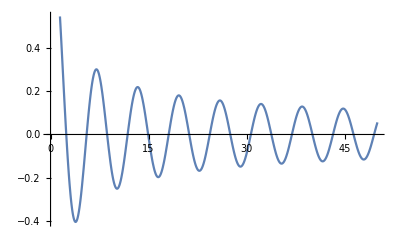

```mathematica
Plot[BesselJ[0,x],{x,0,50}]
```

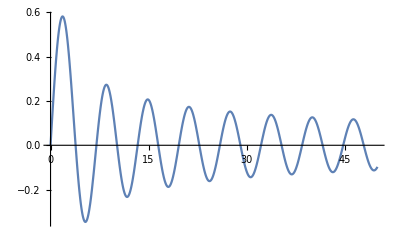

```mathematica
Plot[BesselJ[1,x],{x,0,50}]
```

```mathematica
Asymptotic[ BesselJ[1,x] , x-> ∞ ]
```

(3 Cos[x])/(8 √π x^(3/2))-Cos[x]/(√π √x)+(3 Sin[x])/(8 √π x^(3/2))+Sin[x]/(√π √x)

```mathematica
?BesselK
```

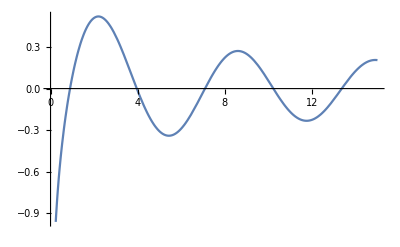

```mathematica
Plot[BesselY[0,r],{r,0,15}]
```

```mathematica
Asymptotic[ BesselY[0,x] , x-> ∞ ]
```

((-1)^(3/4) ⅇ^(-ⅈ x))/(√(2 π) √x)-((-1)^(1/4) ⅇ^(ⅈ x))/(√(2 π) √x)

```mathematica
Asymptotic[ BesselY[1,x] , x-> ∞ ]
```

-((-1)^(1/4) ⅇ^(-ⅈ x))/(√(2 π) √x)+((-1)^(3/4) ⅇ^(ⅈ x))/(√(2 π) √x)

## Construction of Null Tetrad... For Which Metric? Tensors Need To Be Calculated First

```mathematica
(* NULL TETRAD APPENDIX B&7 *)
```

```mathematica
(* PLEASE NOTE:  WE USE THE NEWMAN PENROSE CONVENTION  (l,n,m,mbar) which corresponds to their (k,m,t,tbar) .  My apologies *)
```

```mathematica
Clear[ℓ]
ℓ=
(1/(√2)){1,0,0,1}
```

{1/(√2),0,0,1/(√2)}

```mathematica
Clear[𝓃]
𝓃 = 
(1/(√2)){1,0,0,-1}
```

{1/(√2),0,0,-1/(√2)}

```mathematica
Clear[𝓂]
𝓂 = 
(1/(√2)){0,1,ⅈ,0}
```

{0,1/(√2),ⅈ/(√2),0}

```mathematica
Clear[𝓂bar]
𝓂bar =
(1/(√2)){0,1,0ⅈ,0}
```

{0,1/(√2),0,0}

```mathematica
(* Always check if indices needed are up or down and these are DOWN *) 
l = ToTensor[ {"NewTensor" , "l"} , tensorList[[1]] , ℓ , {0μ}]
n = ToTensor[{"NewTensor" , "n" } , tensorList[[1]] , 𝓃 , {0μ} ] 
m = ToTensor[{"NewTensor" , "m" } , tensorList[[1]] , 𝓂 , {0μ} ] 
mbar = ToTensor[{"NewTensor" , "mbar" } , tensorList[[1]] , 𝓂bar , {0μ} ]
```

Part::partd: Part specification tensorList⟦1⟧ is longer than depth of object.

Invalid call to ToTensor[]. Unexpected parameters: {{NewTensor,l},tensorList⟦1⟧,{1/(√2),0,0,1/(√2)},{0}}

$Aborted

Part::partd: Part specification tensorList⟦1⟧ is longer than depth of object.

Invalid call to ToTensor[]. Unexpected parameters: {{NewTensor,n},tensorList⟦1⟧,{1/(√2),0,0,-1/(√2)},{0}}

$Aborted

Part::partd: Part specification tensorList⟦1⟧ is longer than depth of object.

Invalid call to ToTensor[]. Unexpected parameters: {{NewTensor,m},tensorList⟦1⟧,{0,1/(√2),ⅈ/(√2),0},{0}}

$Aborted

Part::partd: Part specification tensorList⟦1⟧ is longer than depth of object.

Invalid call to ToTensor[]. Unexpected parameters: {{NewTensor,mbar},tensorList⟦1⟧,{0,1/(√2),0,0},{0}}

$Aborted

```mathematica
TensorValues[ContractIndices[l[-μ]l[μ]]] == 0  // Expand // Simplify 
TensorValues[ContractIndices[n[-μ]n[μ]] ]== 0   // Expand // Simplify 
TensorValues[ContractIndices[m[-μ]m[μ]]] == 0   // Expand // FullSimplify 
TensorValues[ContractIndices[mbar[-μ]mbar[μ]]] == 0  // Expand // FullSimplify 
TensorValues[ContractIndices[l[-μ]n[μ]]] == 1// Expand // FullSimplify 
TensorValues[ContractIndices[l[μ]n[-μ]]] == 1  // Expand // FullSimplify 
TensorValues[ContractIndices[m[-μ]mbar[μ]]] == - 1 // Expand // FullSimplify 
TensorValues[ContractIndices[m[μ]mbar[-μ]]] == - 1 // Expand // FullSimplify 
Clear[completenessDownIndices]
completenessDownIndices = 
MergeTensors[l[-μ]n[-ν]+n[-μ]l[-ν] - m[-μ]mbar[-ν]- m[-ν]mbar[-μ]]  ;
TensorValues[ completenessDownIndices ]   // Expand // FullSimplify // MatrixForm

Thread[Flatten[metric2pt22] == 
Flatten[ TensorValues[ completenessDownIndices ]] ] // Expand // FullSimplify  // TableForm

Clear[completenessUpIndices]
completenessUpIndices = 
MergeTensors[l[μ]n[ν]+n[μ]l[ν] - m[μ]mbar[ν]- m[ν]mbar[μ]]  ;
TensorValues[ completenessUpIndices ]   // Expand // FullSimplify // MatrixForm

Thread[Flatten[inverse2pt22] == 
Flatten[ TensorValues[ completenessUpIndices ]] ]  // Expand // FullSimplify  // TableForm
```

Invalid call to TensorValues[]. Unexpected parameters: {l[-μ] l[μ]}

$Aborted

Invalid call to TensorValues[]. Unexpected parameters: {n[-μ] n[μ]}

$Aborted

Invalid call to TensorValues[]. Unexpected parameters: {m[-μ] m[μ]}

$Aborted

Invalid call to TensorValues[]. Unexpected parameters: {mbar[-μ] mbar[μ]}

$Aborted

Invalid call to TensorValues[]. Unexpected parameters: {l[-μ] n[μ]}

$Aborted

Invalid call to TensorValues[]. Unexpected parameters: {l[μ] n[-μ]}

$Aborted

Invalid call to TensorValues[]. Unexpected parameters: {m[-μ] mbar[μ]}

$Aborted

Invalid call to TensorValues[]. Unexpected parameters: {m[μ] mbar[-μ]}

$Aborted

Passed Option 'NestQuantity→0' did not satisfy test.
OptionValue of NestQuantity must be a positive Integer.

Aborting in MergeTensors[].

$Aborted

Invalid call to TensorValues[]. Unexpected parameters: {completenessDownIndices}

$Aborted

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[metric2pt22].

Invalid call to TensorValues[]. Unexpected parameters: {completenessDownIndices}

$Aborted

Passed Option 'NestQuantity→0' did not satisfy test.
OptionValue of NestQuantity must be a positive Integer.

Aborting in MergeTensors[].

$Aborted

Invalid call to TensorValues[]. Unexpected parameters: {completenessUpIndices}

$Aborted

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[inverse2pt22].

Invalid call to TensorValues[]. Unexpected parameters: {completenessUpIndices}

$Aborted

## Attempt at Numerical Solution To Vacuum Field Equations For Metric 1 (PLEASE NOTE: INITIAL AND BOUNDARY CONDITIONS ARE NOT PHYSICAL - JUST TRYING TO SOLVE A SYSTEM FIRST)

```mathematica
Clear[pdes]
pdes = 
vacuumFieldEquationsMetric1[[2;;4]]  ;
pdes // TableForm // pdConv
```

(∂^2 a(t,z))/(∂t^2)==(∂^2 a(t,z))/(∂z^2)+((∂b(t,z))/(∂t))^2-((∂b(t,z))/(∂z))^2-((∂ψ(t,z))/(∂t))^2+((∂ψ(t,z))/(∂z))^2
(∂^2 b(t,z))/(∂t^2)==(∂a(t,z))/(∂t) (∂b(t,z))/(∂t)+(∂a(t,z))/(∂z) (∂b(t,z))/(∂z)-3/2 ((∂b(t,z))/(∂t))^2+1/2 ((∂b(t,z))/(∂z))^2-1/2 ((∂ψ(t,z))/(∂t))^2-1/2 ((∂ψ(t,z))/(∂z))^2
(∂^2 ψ(t,z))/(∂t^2)==-2 (∂b(t,z))/(∂t) (∂ψ(t,z))/(∂t)+2 (∂b(t,z))/(∂z) (∂ψ(t,z))/(∂z)+(∂^2 ψ(t,z))/(∂z^2)

```mathematica
Clear[bcs]
bcs = { 
( a[t,z] /. {t-> 0} ) == Exp[-(z-0.5)^2] , 
( b[t,z] /. {t-> 0} ) == Cosh[z],
( ψ[t,z] /. {t-> 0} ) == Cos[z]+1 , 
( D[a[t,z],t] /. {t-> 0} ) == z , 
( D[b[t,z],t] /. {t-> 0} ) ==  z^2 , 
( D[ψ[t,z],t] /. {t-> 0} ) == z^3, 
( a[t,z] /. {z-> 0} ) == 0.1 , 
( b[t,z] /. {z-> 0} ) == 0.2 , 
( ψ[t,z] /. {z-> 0} ) == 0.3 , 
( a[t,z] /. {z-> 1} ) == 0.1 , 
( b[t,z] /. {z-> 1} ) == 0.2 , 
( ψ[t,z] /. {z-> 1} ) == 0.3  
} ;
bcs // TableForm // pdConv
```

a(0,z)==ⅇ^(-(z-0.5)^2)
b(0,z)==cosh(z)
ψ(0,z)==cos(z)+1
(∂a(0,z))/(∂0)==z
(∂b(0,z))/(∂0)==z^2
(∂ψ(0,z))/(∂0)==z^3
a(t,0)==0.1
b(t,0)==0.2
ψ(t,0)==0.3
a(t,1)==0.1
b(t,1)==0.2
ψ(t,1)==0.3

```mathematica
Clear[pdeSystem]
pdeSystem = 
Flatten[{pdes,bcs}] ;
pdeSystem  // TableForm // pdConv
```

(∂^2 a(t,z))/(∂t^2)==(∂^2 a(t,z))/(∂z^2)+((∂b(t,z))/(∂t))^2-((∂b(t,z))/(∂z))^2-((∂ψ(t,z))/(∂t))^2+((∂ψ(t,z))/(∂z))^2
(∂^2 b(t,z))/(∂t^2)==(∂a(t,z))/(∂t) (∂b(t,z))/(∂t)+(∂a(t,z))/(∂z) (∂b(t,z))/(∂z)-3/2 ((∂b(t,z))/(∂t))^2+1/2 ((∂b(t,z))/(∂z))^2-1/2 ((∂ψ(t,z))/(∂t))^2-1/2 ((∂ψ(t,z))/(∂z))^2
(∂^2 ψ(t,z))/(∂t^2)==-2 (∂b(t,z))/(∂t) (∂ψ(t,z))/(∂t)+2 (∂b(t,z))/(∂z) (∂ψ(t,z))/(∂z)+(∂^2 ψ(t,z))/(∂z^2)
a(0,z)==ⅇ^(-(z-0.5)^2)
b(0,z)==cosh(z)
ψ(0,z)==cos(z)+1
(∂a(0,z))/(∂0)==z
(∂b(0,z))/(∂0)==z^2
(∂ψ(0,z))/(∂0)==z^3
a(t,0)==0.1
b(t,0)==0.2
ψ(t,0)==0.3
a(t,1)==0.1
b(t,1)==0.2
ψ(t,1)==0.3

```mathematica
Clear[pdeSolution ]
pdeSolution = 
Flatten[NDSolve[pdeSystem,{a,b,ψ},{z,0,1},{t,0,1},Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->77,"MaxPoints"->77,"DifferenceOrder"->2}}]] ;
pdeSolution // TableForm
```

NDSolve::ibcinc: Warning: boundary and initial conditions are inconsistent.

NDSolve::ndsz: At t == 0.519375, step size is effectively zero; singularity or stiff system suspected.

NDSolve::eerr: Warning: scaled local spatial error estimate of 3868.61 at t = 0.519375 in the direction of independent variable z is much greater than the prescribed error tolerance. Grid spacing with 77 points may be too large to achieve the desired accuracy or precision. A singularity may have formed or a smaller grid spacing can be specified using the MaxStepSize or MinPoints method options.

a→InterpolatingFunction[…]
b→InterpolatingFunction[…]
ψ→InterpolatingFunction[…]

```mathematica
Clear[aSolution]
aSolution = 
a /. pdeSolution[[1]]
```

InterpolatingFunction[…]

```mathematica
Clear[bSolution]
bSolution = 
b /. pdeSolution[[2]]
```

InterpolatingFunction[…]

```mathematica
Clear[psiSolution]
psiSolution = 
ψ /. pdeSolution[[3]]
```

InterpolatingFunction[…]

```mathematica
Plot3D[ aSolution[t,z] ,{z,0,1},{t,0,1},PlotLabel-> " a[t,z]", AxesLabel->{t,z}, PlotRange-> {-100,100}]
```

-Graphics3D-

```mathematica
Plot3D[ bSolution[t,z] ,{z,0,1},{t,0,1},PlotLabel-> " b[t,z]", AxesLabel->{t,z}]
```

-Graphics3D-

```mathematica
Plot3D[ psiSolution[t,z] ,{z,0,1},{t,0,1},PlotLabel-> " ψ[t,z]", AxesLabel->{t,z}]
```

-Graphics3D-